# Lungs

```mathematica
Needs["IGraphM`"]
```

## Theory plots

```mathematica
m[x_]:=1/(1+(x)^-5);
intm[x_]:=Integrate[m[y],y]/.{y->x};
```

```mathematica
FindRoot[2/1.7 NIntegrate[m[x]Exp[- (λ x)/1.7-(intm[x]-intm[0])],{x,0,∞}]==1,{λ,0.0}]
```

NIntegrate::inumr: The integrand ⅇ^(-0.588235 x λ+«1»+1/20 (-20 x-2 √Plus[«2»] ArcTan[Times[«2»]]+2 √Times[«2»] ArcTan[Times[«2»]]+4«1»«1»+(-1+Power[«2»]) Log[Plus[«3»]]-(1+Power[«2»]) Log[Plus[«3»]]))/(1+1/x^5) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand (ⅇ^(-0.588235 x λ+«1»+1/20 (-20 x-2 √Plus[«2»] ArcTan[Times[«2»]]+2 √Times[«1»] ArcTan[Times[«2»]]+«1»+(-1+Power[«2»]) Log[Plus[«3»]]-(1+Power[«2»]) Log[Plus[«3»]])) (0.-0.588235 x))/(1+1/x^5) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-0.588235 x λ+«1»+1/20 (-20 x-2 √Plus[«2»] ArcTan[Times[«2»]]+2 √Times[«2»] ArcTan[Times[«2»]]+4«1»«1»+(-1+Power[«2»]) Log[Plus[«3»]]-(1+Power[«2»]) Log[Plus[«3»]]))/(1+1/x^5) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{λ→0.141041}

```mathematica
Ap=NIntegrate[Exp[-λ x-(intm[x]-intm[0])]/.{λ->0.14104134320936326},{x,0,∞}]
```

1.69002

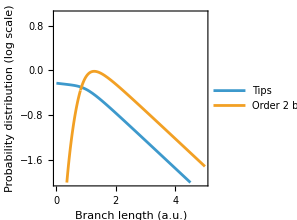

```mathematica
Plot[{Exp[-0.14104134320936326 x-(intm[x]-intm[0])]/Ap,2m[x]Exp[-0.14104134320936326 x-(intm[x]-intm[0])]},{x,0,5},ScalingFunctions->"Log10",PlotRange->{{0,5},{10^-2,10}},Frame->True,(*FrameTicks->None,*)FrameLabel->{"Branch length (a.u.)","Probability distribution (log scale)"},AspectRatio->1,FrameStyle->Black,LabelStyle->{Black,FontSize->14},PlotLegends->Placed[{"Tips","Order 2 branches"}, {Right,Top}]]
```

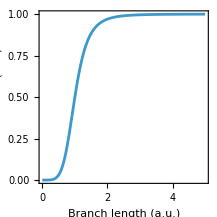

```mathematica
Plot[m[x],{x,0,5},Frame->True,(*FrameTicks->None,*)FrameLabel->{"Branch length (a.u.)","Branch rate (a.u.)"},AspectRatio->1,FrameStyle->Black,LabelStyle->{Black,FontSize->14}]
```

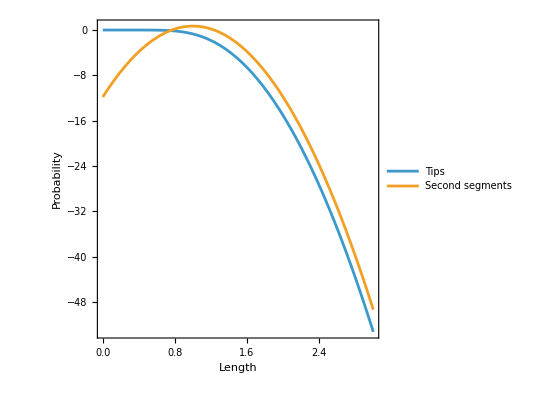

```mathematica
μ=1;σ=0.2;
a=NIntegrate[Erfc[(y-μ)/(√2 σ)],{y,0,3}];
Plot[{a^-1 Erfc[(x-μ)/(√2 σ)],PDF[NormalDistribution[μ,σ],x]},{x,0,3},FrameTicks->None,Frame->True,FrameLabel->{"Length","Probability"},AspectRatio->1,ScalingFunctions->"Log",PlotLegends->Placed[{"Tips","Second segments"},{Right,Top}],LabelStyle->Medium]
```

```mathematica
λ=1;
Plot[{PDF[ExponentialDistribution[λ],x],PDF[ExponentialDistribution[λ],x]},{x,0,5},
FrameTicks->None,Frame->True,FrameLabel->{"Length (arb. units)","Probability"},PlotLegends->Placed[{"Tips","Second segments"},{Right,Top}],
LabelStyle->Medium,PlotStyle->{Automatic,Dashing->0.05}]
```

```mathematica
Plot[PDF[NormalDistribution[5,1],x],{x,0,10},Frame->True,FrameTicks->None,FrameLabel->{"Branch time","Probability"},LabelStyle->Medium]
```

```mathematica
DiscretePlot[Evaluate[Table[(1-x^n)^(1/n),{n,{1,2,3,5,10,50}}]],{x,0,1,0.001},PlotRange->{{0,1.6},{0,1.6}},AspectRatio->1 ,Frame->True,Filling->None,Joined->True,ImageSize->130,FrameStyle->Black,LabelStyle->{Black,FontSize[6.4]},PlotStyle->Thickness[0.01],GridLines->Automatic,FrameLabel->{"d_1/d_0","d_2/d_0"},PlotLegends->{"x = 1","x = 2","x = 3","x = 5","x = 10","x = 50"}]
```

-Graphics-

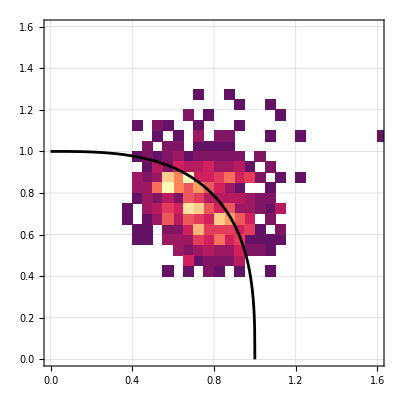

```mathematica
σ=0.10;
Show[DensityHistogram[DeleteCases[Table[Module[{u=VertexOutComponent[tg,v,{1}]},
If[Length[u]==2,{
(Length[VertexOutComponent[tg,u[[1]]]]/Length[VertexOutComponent[tg,v]])^(1/3)RandomVariate[NormalDistribution[1,σ]],
(Length[VertexOutComponent[tg,u[[2]]]]/Length[VertexOutComponent[tg,v]])^(1/3)RandomVariate[NormalDistribution[1,σ]]}/RandomVariate[NormalDistribution[1,σ]]]],
{v,VertexList[gr,v_/;boh[v]>2]}],Null],PlotRange->{{0,1.6},{0,1.6}},GridLines->Automatic,PlotRangePadding->None,LabelStyle->Black],DiscretePlot[(1-x^3)^(1/3),{x,0,1,0.001},Filling->None,Joined->True,PlotStyle->Black]]
```

## Preamble

```mathematica
getl[g_,e_]:=AnnotationValue[{g,e},Annotation][[1]];
getw[g_,e_]:=AnnotationValue[{g,e},Annotation][[2]];
se=If[Length[#]>1,StandardDeviation[#]/(√Length[#])]&;
align[v1_,v2_]:=Dot[v1,v2]/(Norm[v1]Norm[v2]);
bootstrap[f_,y_,n_]:=StandardDeviation[Array[f[RandomChoice[y,Length[y]]]&,n]];
Gini[x_List]:=1-(2Total[FoldList[Plus,0,Sort[x]]])/(Total[x](Length[x]+1));
kld[p_,q_]:=Total[MapThread[If[#1==0,0,#1 Log[#1/#2]]&,{p,q}]];
jsd[p_,q_]:=Module[{m=(p+q)/2},(kld[p,m]+kld[q,m])/2];
cov[x_]:=StandardDeviation[x]/Mean[x];
voxel=7;
skelgraphics[g_]:=Graphics3D[Table[{Thickness[0.005],Line[{xyz[[e[[1]]]],xyz[[e[[2]]]]}]},{e,EdgeList[g]}],SphericalRegion->True,Boxed->False,ImageSize->(voxel/10 BoundingRegion[xyz[[#]]&/@VertexList[g],"MinBall"][[2]])];
pe=#["ParameterEstimates"]&;
pcit=#["ParameterConfidenceIntervalTable"]&;
r2=#["RSquared"]&;
bfa=#["BestFitAround"]&;
tci[ν_]:=InverseCDF[StudentTDistribution[ν],1-0.05/2];
graphsettings={Frame->True,FrameStyle->Directive[Black],AspectRatio->1,GridLines->Automatic,LabelStyle->{Black,FontSize->6.4}};
```

### Smoothen new version

```mathematica
Clear[smoothen];
smoothen[g_]:=
If[TreeGraphQ[g],
Module[{daddies={1},daddy,newdad,gp={0},tips,string,newedges={},newwids={},newlens={},newgraph},
While[Length[daddies]>0,
daddy=First[daddies];
tips=DeleteCases[AdjacencyList[g,daddy],v_/;MemberQ[gp,v]];
Do[
string=NestWhile[Union[#,Cases[AdjacencyList[g,#],Except[daddy]]]&,{t},AllTrue[#,VertexDegree[g,#]==2&]&];
newdad=First@Cases[string,v_/;VertexDegree[g,v]=!=2];
AppendTo[newedges,daddy<->newdad];
AppendTo[newlens,Total[getl[g,#]&/@EdgeList[Subgraph[g,Join[{daddy},string]]]]];
AppendTo[newwids,Mean[getw[g,#]&/@EdgeList[Subgraph[g,Join[{daddy},string]]]]];
If[VertexDegree[g,newdad]>2,
AppendTo[daddies,newdad];
If[Length[string]==1,AppendTo[gp,daddy],AppendTo[gp,First@Cases[AdjacencyList[g,newdad],v_/;MemberQ[string,v]]]];
],{t,tips}];
daddies=Delete[daddies,1];
];
newgraph=Graph[Annotation[newedges[[#]],{newlens[[#]],newwids[[#]]}]&/@Range[Length[newedges]]]
]];
```

```mathematica
gr=Module[{g1=gr,g2},
g2=EdgeDelete[g1,e_/;getl[g1,e]==0];
VertexDelete[g2,v_/;VertexDegree[g2,v]==0]];
```

```mathematica
Timing[gr=Module[{gx=gr},smoothen[gx]];]
```

```mathematica
tipdata=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\tips.csv"];
```

## Importing

```mathematica
net=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\mouse\\Left_clean_edge_list.dat","HeaderLines"->4];
```

```mathematica
xyz=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\mouse\\Left_clean_node_positions.dat","HeaderLines"->4][[;;,2;;4]];
```

```mathematica
net=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\Python\\simulation.csv","HeaderLines"->1];
```

```mathematica
net=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\FULL_clean_edge_list.dat","HeaderLines"->4];
```

```mathematica
xyz=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\FULL_clean_node_positions.dat","HeaderLines"->4][[;;,2;;4]];
```

```mathematica
vers=DeleteDuplicates@Flatten@{net[[;;,1]],net[[;;,2]]};
edges=#[[1]]<->#[[2]]&/@net;
l=net[[;;,3]];
w=net[[;;,4]];
gr=Graph[MapThread[Annotation[#1,{#2,#3}]&,{edges,l,w}]];
While[VertexDegree[gr,1]==1,
newroot=First[AdjacencyList[gr,1]];
gr=VertexDelete[gr,1];
gr=VertexReplace[gr,{newroot->1}];];
```

```mathematica
x0=Mean[xyz];
i=Sum[IdentityMatrix[3](#.#)-KroneckerProduct[#,#]&[x-x0],{x,xyz}];
#/First[#]&@Eigenvalues[i]
```

{1.,0.976464,0.309606}

### 3d visual

```mathematica
Graphics3D[Table[{White,Line[{xyz[[e[[1]]]],xyz[[e[[2]]]]}]},{e,EdgeList[gr]}],SphericalRegion->True,Background->Black,Boxed->False]
```

```mathematica
colordata=ColorData[{"BrightBands",{1,VertexEccentricity[tg,1]}}];
Grid[{{Graphics3D[Table[{ColorData[{"TemperatureMap",{6,15}}][getz[e]],Point[xyz[[e]]]},{e,ends}],
SphericalRegion->True,Background->Black,Boxed->False],
Graphics3D[Table[{ColorData[{"TemperatureMap",{1000,3500}}][ltoroot[e]],Point[xyz[[e]]]},{e,ends}],
SphericalRegion->True,Background->Black,Boxed->False]
}}]
```

```mathematica
{Min[#],Max[#]}&[getz/@ends]
```

```mathematica
Legended[Graphics3D[Table[{ColorData[{"TemperatureMap",{8,14}}][getz[e]],PointSize[0.02],Point[xyz[[e]]]},{e,ends}],
Background->None,SphericalRegion->True,Boxed->False,ImageSize->270],BarLegend[{ColorData[{"TemperatureMap",{8,14}}],{8,14}},LabelStyle->Directive[Black,FontSize->6.4],LegendLabel->"Generation, z",LegendMarkerSize->90]]
```

-Graphics3D-

```mathematica
tips2848=VertexList[gr,(v_/;VertexDegree[gr,v]==1):>7(xyz[[v]])];
```

```mathematica
tips10gw=VertexList[gr,(v_/;VertexDegree[gr,v]==1):>7(xyz[[v]])];
```

```mathematica
tips3685=VertexList[gr,(v_/;VertexDegree[gr,v]==1):>7(xyz[[v]])];
```

```mathematica
tips3138=VertexList[gr,(v_/;VertexDegree[gr,v]==1):>7(xyz[[v]])];
```

```mathematica
tips3822=VertexList[gr,(v_/;VertexDegree[gr,v]==1):>4(xyz[[v]])];
```

```mathematica
Grid[{Graphics3D[Table[{Black,PointSize[Small],Point[e]},{e,#}],SphericalRegion->True,Background->White,Boxed->False,ImageSize->BoundingRegion[#,"MinBall"][[2]]/20]&/@{tips2848,tips10gw,tips3685,tips3138,tips3822}}]
```

```mathematica
mybox=Cuboid[{11,6,9+120},{597,417,277-120}];
Graphics3D[Table[{Black,Point[xyz[[x]]]},{x,Cases[ends,e_/;RegionMember[mybox,xyz[[e]]]]}],Boxed->False,SphericalRegion->True]
```

```mathematica
ends=VertexList[gr,v_/;VertexDegree[gr,v]==1];
pts=Table[xyz[[e]],{e,ends}];
x0=Mean[pts];
r0=voxel BoundingRegion[pts,"MinBall"][[2]];
```

```mathematica
mytip=Last[SortBy[ends,ltoroot]];
mypath=VertexInComponent[tg,mytip][[;;-2]];
```

```mathematica
r0
```

2250.26

```mathematica
ltoroot@mytip
```

1319

```mathematica
myv={200,-300,-200};
Graphics3D[{
Table[{Thickness[0.004],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,Complement[VertexList[gr],mypath,{1}]}],Table[{Thickness[0.015],Red,Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,mypath}],
Table[{Thickness[0.005],Red,Line[{xyz[[i]]-x0+myv,xyz[[getp[i]]]-x0+myv}]},{i,mypath}],Table[{PointSize[0.02],Red,Point[xyz[[i]]-x0+myv]},{i,mypath}],
{Red,Cuboid[1.03xyz[[1]]-x0+myv,0.97xyz[[1]]-x0+myv]}},Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],Scaled[{0.1,0.1}],{Left,Bottom},0.111]},SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
Graphics3D[{Table[{Thickness[0.005],Red,Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,mypath}],Table[{PointSize[0.02],Red,Point[xyz[[i]]-x0]},{i,mypath}],
{Red,Cuboid[1.02xyz[[1]]-x0,0.98xyz[[1]]-x0]}},SphericalRegion->True,Boxed->False,ImageSize->r0/10,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{
Table[{Thickness[0.004],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,Complement[VertexList[gr],{1}]}]},Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],Scaled[{0.1,0.1}],{Left,Bottom},0.111]},SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic"],Translate[ccvhl,-x0]]
```

### Lineage tracing

```mathematica
stems=VertexList[gr,v_/;getz[v]==3];
domains=Table[VertexOutComponent[tg,s],{s,stems}];
```

```mathematica
colorfun[w_]:=(Which@@Flatten[Join[Table[{MemberQ[domains[[i]],w],ColorData["DarkBands"][i/Length[stems]]},{i,Range[Length[stems]]}],{True,Black}]]);
```

```mathematica
Graphics3D[Table[{colorfun[v],(*Thickness[0.005],*)Tube[{-xyz[[v]],-xyz[[getp[v]]]},3]},{v,VertexList[gr,v_/;Not[v==1]]}],SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic",
Epilog->{(*Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.111],*)
Inset[Graphics[{Black,Text["PCW10.2"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]}]
```

```mathematica
stems={83,133,206,103};
domains=Table[VertexOutComponent[tg,s],{s,stems}];
```

```mathematica
colors={Red,Lighter[Blue],Yellow,Orange};
opacities={0.1,1,0.1,0.1};
```

```mathematica
Graphics3D[Table[Table[{colors[[i]],Tube[{-xyz[[v]],-xyz[[getp[v]]]},3]},{v,Cases[domains[[i]],v_/;Not[v==1]]}],{i,{2}}],SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic"]
```

-Graphics3D-

### Aniamtions

```mathematica
r0=BoundingRegion[xyz,"MinBall"][[2]];
```

```mathematica
smin=0.01;smax=0.2;
mypts=Cases[Union[ends,hwends],i_/;RegionMember[Scale[cvxhl,smax,x0],xyz[[i]]]&&Not[RegionMember[Scale[cvxhl,smin,x0],xyz[[i]]]]];
Graphics3D[
Rotate[#,-π/2,{0,1,0}]&[Table[If[MemberQ[hwends,x],{Red,PointSize[0.01],Point[xyz[[x]]-x0]},{Black,PointSize[0.005],Point[xyz[[x]]-x0]}],{x,mypts}]],
SphericalRegion->False,Boxed->False,PlotRange->r0]
```

HW and normal ends

```mathematica
smin=0.01;smax=0.2;
mypts=Cases[Union[ends,hwends],i_/;RegionMember[Scale[cvxhl,smax,x0],xyz[[i]]]&&Not[RegionMember[Scale[cvxhl,smin,x0],xyz[[i]]]]];
frames=Table[
Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[If[MemberQ[hwends,x],{Red,PointSize[0.01],Point[xyz[[x]]-x0]},{Black,PointSize[0.005],Point[xyz[[x]]-x0]}],{x,mypts}]]],
SphericalRegion->False,Boxed->False,PlotRange->r0],
{θ,Subdivide[2π,48]}];
```

```mathematica
mypts=srftips;
frames=Table[
Show[Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{Red,PointSize[0.01],Point[xyz[[x]]-x0]},{x,mypts}]]],
Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.111],
Inset[Graphics[{Black,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
SphericalRegion->False,Boxed->False,PlotRange->r0],
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[Translate[MeshRegion[ccvhl,MeshCellStyle->Opacity[0.2]],-x0]]]],
{θ,Subdivide[2π,60]}];
```

```mathematica
ListAnimate[frames,30]
```

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3685_bulk_tips.gif",frames]
```

HW tree

```mathematica
frames=Table[
Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{If[MemberQ[EdgeList[Highways],e],Red,Darker[LightBlue]],Thickness[Small],Line[xyz[[e[[#]]]]-x0&/@{1,2}]},{e,EdgeList[gr]}]
]],
SphericalRegion->False,Boxed->False,PlotRange->r0],
{θ,Subdivide[2π,48]}];
```

Tips z coloring

```mathematica
x0=RegionCentroid[ccvhl];r0=BoundingRegion[xyz,"MinBall"][[2]];
```

```mathematica
frames=Table[Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{Black,PointSize[0.01],Point[xyz[[e]]-x0]},{e,ends}]]
],
Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.119],
Inset[Graphics[{Black,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
SphericalRegion->False,Boxed->False,PlotRange->300,Background->White],{θ,Subdivide[2π,120]}];
```

```mathematica
frames=Table[Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{Black,PointSize[0.01],Point[xyz[[e]]-x0]},{e,srftips}]]
],
Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.119],
Inset[Graphics[{Black,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
SphericalRegion->False,Boxed->False,PlotRange->300,Background->White],{θ,Subdivide[2π,120]}];
```

```mathematica
colordata=ColorData[{"TemperatureMap",{8,14}}];
Graphics3D[
Rotate[#,0,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{colordata[getz[e]],PointSize[0.01],Point[xyz[[e]]-x0]},{e,ends}]]
],
Epilog->{Inset[Graphics[{White,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.119],
Inset[Graphics[{White,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
SphericalRegion->False,Boxed->False,PlotRange->300,Background->Black]
```

-Graphics3D-

```mathematica
colordata=ColorData[{"TemperatureMap",{8,14}}];
frames=Table[
Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{colordata[getz[e]],PointSize[0.01],Point[xyz[[e]]-x0]},{e,ends}]]
],
Epilog->{Inset[Graphics[{White,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.119],
Inset[Graphics[{White,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
SphericalRegion->False,Boxed->False,PlotRange->300,Background->Black],
{θ,Subdivide[2π,120]}];
```

```mathematica
frames=Table[
Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[Line[{xyz[[v]],xyz[[getp[v]]]}],{v,VertexList[gr,Except[1]]}]]],
SphericalRegion->False,Boxed->False,PlotRange->r0],
{θ,Subdivide[2π,96]}];
```

```mathematica
frames=Table[
Graphics3D[
Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[
Table[{colorfun[v],Thickness[0.003],Line[{xyz[[v]]-x0,xyz[[getp[v]]]-x0}]},{v,VertexList[gr,v_/;Not[v==1]]}]]],
SphericalRegion->False,Boxed->False,PlotRange->r0],
{θ,Subdivide[2π,48]}];
```

```mathematica
ListAnimate[frames,30]
```

```mathematica
frames=Table[
Graphics3D[Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[{
Table[{Red,Thickness[0.003],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[skeleton,v_/;Not[v==1]&&branchorder[v]>=4]}],
Table[{Black,Thickness[0.003],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[gr,Except[1]]}]
}]],
SphericalRegion->True,Boxed->False,PlotRange->r0],
{θ,Subdivide[2π,48]}];
```

```mathematica
frames=Table[Graphics3D[Rotate[#,θ,{0,0,1}]&[Rotate[#,-π/2,{0,1,0}]&[{
Table[{Red,Tube[{xyz[[i]]-x0,xyz[[getp[i]]]-x0},5]},{i,VertexList[skeleton,v_/;branchorder[v]>wco&&Not[v==1]]}],
Table[{Red,Thickness[0.002],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[skeleton,v_/;branchorder[v]<=wco]}],
Table[{Blue,Thickness[0.002],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[skeletont,v_/;branchorder[v]<=100]}]
}]],Epilog->{Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.1,0.1}],{Left,Bottom},0.119],Inset[Graphics[{Black,Text["PCW8.7"]}],Scaled[{0.77,0.07}],{Left,Bottom},0.1]},
Background->White,Boxed->False,SphericalRegion->True,PlotRange->300,ViewProjection->"Orthographic"],{θ,Subdivide[2π,120]}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3685_ends_colored.mp4",frames,FrameRate->30]
```

C:\Users\ivanl\OneDrive - University of Cambridge\lung project writing\movies\eh3685_ends_colored.mp4

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3685_ends_black.mp4",frames,FrameRate->30]
```

C:\Users\ivanl\OneDrive - University of Cambridge\lung project writing\movies\eh3685_ends_black.mp4

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3685_srftips.mp4",frames,FrameRate->30]
```

C:\Users\ivanl\OneDrive - University of Cambridge\lung project writing\movies\eh3685_srftips.mp4

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3685_core_network.mp4",
Table[Rasterize[frame,"Image",ImageResolution->144,ImageSize->{480,480}],{frame,frames}],FrameRate->30]
```

C:\Users\ivanl\OneDrive - University of Cambridge\lung project writing\movies\eh3685_core_network.mp4

```mathematica
x0=Mean[xyz];
r0=BoundingRegion[xyz,"MinBall"][[2]];
```

```mathematica
frames=Table[Graphics3D[
Rotate[#,90°-(120°)i,{0,0,1}]&@Rotate[#,-90°,{0,1,0}]&@VertexList[gr,(v_/;getz[v]>=1&&zintage[getp[v]]<i):>
If[zintage[v]>i,
Tube[{xyz[[getp[v]]]-x0+(i-zintage[getp[v]])/(zintage[v]-zintage[getp[v]])(xyz[[v]]-xyz[[getp[v]]]),xyz[[getp[v]]]-x0},getpw[v]/14],
Tube[{xyz[[v]]-x0,xyz[[getp[v]]]-x0},getpw[v]/14]]
],SphericalRegion->True,Boxed->False,PlotRange->r0],{i,0,1+1/10,1/60}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\movies\\eh3138_growing.gif",frames]
```

## Plots (N tips, vol ect )

```mathematica
ages={5.7,6.1,6.1,6.1,6.3,6.6,6.6,6.6,7,7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
ntips={3,7,9,13,18,14,22,22,21,46,55,145,349,360,243,361,500,545,760,1019,1143,1508,1254,1403,1594,1652,2010,4127,6780,8722,12393,21027,23081};
vol={97755,13770000,75200000,6085700,18560000,26900000,46520000,99450000,64110000,504700000,961500000,2078000000,3504000000,2826000000,2054000000,2879000000,3982000000,3243000000,6965000000,6496000000,8029000000,6954000000,7344000000,9375000000,9412000000,7502000000,9848000000,17200000000,24130000000,21320000000,31290000000,42290000000,55830000000};
srftipsn={3,6,7,13,18,12,22,21,21,46,52,108,209,229,160,228,277,297,342,465,518,608,512,537,682,654,748,1342,1719,1789,2376,3308,3501};
tipl={156.7,104.8,108.5,138.5,184.6,141,117.8,157.6,159.4,172.5,228,174.6,143.8,129.9,148,125.7,113,117.9,125.2,110.9,110.9,90.7,103.8,100.7,95.7,85.5,92.1,77.6,69,60,58.2,58,58.3};
tipw={106.4,84.2,108.7,77.8,107.2,73.2,72.3,97.6,93.7,91.3,93.9,94.2,79.3,80.8,72,72.7,91.2,70.5,82.3,71,77.3,73,69.8,83.8,76.4,68.9,75.2,71.7,69.1,69,71.1,68.7};
tip2l={16,130.7,165.4,143.4,222.6,145,137.2,199,163.1,198.8,194.4,173.3,151.4,126.5,142.5,147.2,132,117.3,116.5,104.3,109.7,95.8,101.7,110.4,108.3,92.3,101.1,84.9,75.9,65.6,65.9,61,62.1};
nbranches={4,12,16,25,33,25,42,42,39,90,108,288,691,716,481,716,991,1082,1513,2027,2273,3001,2493,2792,3171,3287,3992,8161,13434,17172,24477,41172,45211};
tip2lcov={1.4375,0.181818,0.479821,0.275862,0.20603,0.267176,0.467153,0.477528,0.319018,0.421053,0.551546,0.471264,0.449664,0.376,0.41844,0.575342,0.540741,0.37931,0.37069,0.326923,0.385321,0.347368,0.356436,0.309091,0.37037,0.315217,0.376238,0.297619,0.302632,0.338462,0.287879,0.333333,0.322581};
```

```mathematica
ListPlot[{{ages,(vol/ntips)^(1/3)}ᵀ,{ages,tipl}ᵀ},graphsettings,ImageSize->120,FrameLabel->{"Age (PCW)","Length (μm)"},PlotRange->{{4,16},{0,300}},PlotMarkers->{"OpenMarkers",3},PlotLegends->Placed[{"(Tip density)^(-1/3)","Tip length"},Right]]
```

-Graphics-

```mathematica
fitv=LinearModelFit[{ages,vol^(1/3)}ᵀ,a,a];
```

```mathematica
#[fitv]&/@{r2,pcit}
```

{0.966361, | Estimate | Standard Error | Confidence Interval
1 | -3324.98 | 166.58 | {-3664.72,-2985.23}
a | 580.526 | 19.4532 | {540.851,620.201}}

```mathematica
fitn=LinearModelFit[{ages,Log@nbranches}ᵀ,a,a];
```

```mathematica
fitntips=LinearModelFit[{ages,Log@ntips}ᵀ,a,a];
```

```mathematica
fit1=LinearModelFit[{ages[[;;11]],Log[vol[[;;11]]]}ᵀ,x,x];
fit2=LinearModelFit[{ages[[12;;]],Log[vol[[12;;]]]}ᵀ,x,x];
```

```mathematica
Show[ListPlot[{ages,nbranches}ᵀ,
graphsettings,ScalingFunctions->"Log10",PlotMarkers->{"OpenMarkers",3},FrameLabel->{"Age (PCW)","Number of branhces, N"},PlotRange->{{4,14},{10^0,10^5}}],ListLinePlot[Table[{a,Exp@fitn["BestFitAround"]},{a,5.7,12,0.1}],PlotStyle->Thickness[0.008],ScalingFunctions->"Log10",IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
pcit[fitn]
```

| Estimate | Standard Error | Confidence Interval
1 | -5.77326 | 0.475718 | {-6.74349,-4.80303}
a | 1.45639 | 0.0555542 | {1.34308,1.56969}

```mathematica
r2[fitn]
```

0.95684

```mathematica
regularizer=If[#[[1]]<#[[2]],Around[#[[1]],{#[[1]]-10^-10,#[[2]]}],#]&;
```

```mathematica
Show[ListPlot[Transpose[{ages,ntips/vol}],ScalingFunctions->"Log10",graphsettings,
PlotMarkers->{"OpenMarkers",3},FrameLabel->{"Age (PCW)","Tip density (number of tips / μm^3)"},PlotRange->{{4,14},{10^-8,10^-4}},ImageSize->125],ListLinePlot[Table[{a,regularizer@(Exp[fitntips["BestFitAround"]]/fitv["BestFitAround"]^3)},{a,5.8,12,0.1}],IntervalMarkers->"Bands",PlotRange->{{4,14},{10^-8,10^-4}},ScalingFunctions->"Log10"]]
```

```mathematica
fitn["ParameterConfidenceIntervalTable"]
```

```mathematica
Log[Around[1.43216,1.96 0.0516287]]/Log[2]
```

```mathematica
Show[ListPlot[{ages,vol}ᵀ,PlotMarkers->{"OpenMarkers",3},ScalingFunctions->"Log10",PlotRange->{{4,14},{10^4,10^12}},ImageSize->125,graphsettings,FrameLabel->{"Age (PCW)","Concave hull volume (μm^3)"}]
,ListLinePlot[{Table[{a,fitv["BestFitAround"]^3},{a,5.8,12,0.1}],Table[{a,Exp[fitn["BestFitAround"]+16.4]},{a,5.8,12,0.1}]},IntervalMarkers->"Bands",PlotRange->All,ScalingFunctions->"Log10",PlotLegends->Placed[{None,"Number of branches, N"},{Right,Bottom}],LabelStyle->{Black,FontSize->4.8}]]
```

-Graphics-

```mathematica
fitv["RSquared"]
```

0.966361

```mathematica
Show[ListLogPlot[{ages,vol}ᵀ,PlotMarkers->"OpenMarkers",graphsettings,FrameLabel->{"Age (PCW)","Concave hull volume (μm^3)"}],
Plot[fit1[x],{x,5.7,7.5},PlotStyle->Dashed],Plot[fit2[x],{x,7.5,12},PlotStyle->Dashed]]
```

```mathematica
fit1=LinearModelFit[{ages[[11;;]],Log@tipl[[11;;]]}ᵀ,x,x];
fit2=LinearModelFit[{ages[[11;;-2]],Log@tipw[[11;;]]}ᵀ,x,x];
```

```mathematica
r2/@{fit1,fit2}
```

{0.923155,0.449785}

```mathematica
Grid[{pcit/@{fit1,fit2}}]
```

| Estimate | Standard Error | Confidence Interval
1 | 7.0722 | 0.156125 | {6.74752,7.39688}
x | -0.265726 | 0.01673 | {-0.300518,-0.230934} |  | Estimate | Standard Error | Confidence Interval
1 | 4.85122 | 0.129562 | {4.58096,5.12148}
x | -0.0569901 | 0.0140944 | {-0.0863906,-0.0275896}

```mathematica
0.266+0.017
```

0.283

```mathematica
0.266-0.017
```

0.249

```mathematica
Show[ListPlot[{{ages,tipl}ᵀ,{ages[[;;-2]],tipw}ᵀ},PlotMarkers->{"OpenMarkers",3},PlotLegends->Placed[{"Tip length","Tip diameter"},{Right,Top}],FrameLabel->{"Age (PCW)","Tip length, diameter (μm)"},graphsettings,ImageSize->120,PlotRange->{{4,14},{0,250}}],
ListLinePlot[{Table[{x,Exp@fit1["BestFitAround"]},{x,7,12,0.1}],Table[{x,Exp@fit2["BestFitAround"]},{x,7,12,0.1}]},IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
ages={7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
srftipl={166,234,192,169,154,173,136,140,139,156,134,134,110,130,131,113,105,110,96,83,72,69,69,66};
blktipl={66,143,122,106,88,101,108,100,93,100,92,92,78,86,82,82,72,82,67,64,57,56,56,57};
```

```mathematica
fit1=LinearModelFit[{ages,Log@srftipl}ᵀ,x,x];
fit2=LinearModelFit[{ages,Log@blktipl}ᵀ,x,x];
```

```mathematica
r2/@{fit1,fit2}
```

{0.927327,0.701488}

```mathematica
pcit/@{fit1,fit2}
```

{ | Estimate | Standard Error | Confidence Interval
1 | 7.05318 | 0.135801 | {6.77155,7.33482}
x | -0.245814 | 0.0146712 | {-0.27624,-0.215387}, | Estimate | Standard Error | Confidence Interval
1 | 5.8769 | 0.205229 | {5.45128,6.30252}
x | -0.159419 | 0.0221717 | {-0.2054,-0.113438}}

```mathematica
Show[ListPlot[{{ages,srftipl}ᵀ,{ages,blktipl}ᵀ},FrameLabel->{"Age (PCW)","Tip length (μm)"},graphsettings,PlotMarkers->{"OpenMarkers",3},PlotStyle->{Red,Blue},PlotLegends->Placed[{"Surface tips","Bulk tips"},{Right,Top}],ImageSize->120,PlotRange->{{6,14},{0,250}}],
ListLinePlot[{Table[{x,Exp[fit1["BestFitAround"]]},{x,7,12,0.1}],Table[{x,Exp[fit2["BestFitAround"]]},{x,7,12,0.1}]},IntervalMarkers->"Bands",PlotStyle->{Red,Blue}]]
```

-Graphics-

```mathematica
Show[ListPlot[{ages[[2;;]],tip2lcov[[2;;]]}ᵀ,graphsettings,ImageSize->120,FrameLabel->{"Age PCW","Order 2 tip length CV"},PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,0.8}}],
ListPlot[{{6,9,12},ConstantArray[Around[Mean[#],1.96se[#]]&[tip2lcov[[2;;]]],3]}ᵀ,Joined->True,IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
{Mean[#],se[#]}&[tip2lcov[[2;;]]]
```

{0.37181,0.0166162}

```mathematica
Show[ListPlot[{ages[[11;;]],bopow}ᵀ,PlotMarkers->"OpenMarkers",FrameLabel->{"Age (PCW)","Branching ratio"},graphsettings,PlotRange->{Automatic,{1.9,3.1}}],Plot[Mean[bopow],{x,6,11},PlotStyle->Dashed]]
```

```mathematica
ntips=ToExpression/@Flatten@List[];
nsrftips=ToExpression/@Flatten@List[];
```

```mathematica
fit=LinearModelFit[{ages,ntips/srftipsn}ᵀ[[10;;]],x,x];
```

```mathematica
Show[ListPlot[{ages,srftipsn/ntips}ᵀ,PlotMarkers->{"OpenMarkers",3},FrameLabel->{"Age (PCW)","Fraction of tips on surface"},graphsettings,PlotRange->{{4,14},{0,1.2}}],
ListLinePlot[Table[{x,1/fit["BestFitAround"]},{x,7.5,12,0.1}],IntervalMarkers->"Bands",PlotRange->{0,1}]]
```

-Graphics-

```mathematica
#@fit&/@{r2,pcit}
```

{0.906088, | Estimate | Standard Error | Confidence Interval
1 | -7.44054 | 0.704185 | {-8.90093,-5.98015}
x | 1.10837 | 0.076076 | {0.950594,1.26614}}

```mathematica
pcit@LinearModelFit[Transpose[{ages,Log@srftipsn}][[10;;]],x,x]
```

| Estimate | Standard Error | Confidence Interval
1 | -1.52829 | 0.453693 | {-2.4692,-0.587393}
x | 0.839951 | 0.0490144 | {0.738301,0.9416}

```mathematica
pcit@LinearModelFit[Transpose[{ages,Log@srftipsn}][[;;10]],x,x]
```

| Estimate | Standard Error | Confidence Interval
1 | -6.92496 | 1.69269 | {-10.8283,-3.02162}
x | 1.4757 | 0.262194 | {0.871075,2.08032}

```mathematica
Manipulate[Show[Plot[1/(1+(1-r)/(r-τ^-1)(1-ⅇ^(μ(τ^-1-r)(t-7)))),{t,7,12},PlotRange->{0,1.2}],ListPlot[Transpose[{ages,srftipsn/ntips}][[10;;]]]],{μ,0.1,3},{r,0.01,0.99},{τ,1,3}]
```

```mathematica
myfun[μ_,r_,τ_,t_]:=If[Abs[r-τ^-1]<10^-12,1/(1+(1-r)μ t), 1/(1+(1-r)/(r-τ^-1)(1-ⅇ^(μ(τ^-1-r)t)))];
```

```mathematica
pcit@NonlinearModelFit[Transpose[{ages-7,srftipsn/ntips}][[10;;]],{myfun[0.84/r,r,2,t],r>0},{μ,r(*,τ*)},t]
```

```mathematica
fit=LinearModelFit[Log[Transpose[{vol,srftipsn}][[10;;]]],v,v];
```

```mathematica
Exp[bfa[fit]/.{v->Log[10^11]}]
```

7.21.410^3

```mathematica
r2@fit
```

0.97731

```mathematica
Show[ListPlot[Transpose[{vol,srftipsn}],graphsettings,ScalingFunctions->{"Log10","Log10"},ImageSize->125,PlotMarkers->{"OpenMarkers",3},
PlotRange->{{10^3,10^11},{10^0,10^4}},FrameLabel->{"Concave hull volume (μm^3)","Number of surface tips, N_S"}],
ListLinePlot[Table[{u,Exp[bfa[fit]]/.{v->Log[u]}},{u,5 10^8,5 10^10,10^9}],ScalingFunctions->{"Log10","Log10"},IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
pcit@fit
```

| Estimate | Standard Error | Confidence Interval
1 | -16.5535 | 0.739028 | {-18.0861,-15.0208}
v | 1.00443 | 0.0326295 | {0.936761,1.0721}

```mathematica
zmean={1.67,2.86,3.33,3.85,3.83,3.36,4.82,4.864,4.29,5.87,6.2,7.54,9.03,8.91,8.55,8.89,9.69,9.81,10.2,10.05,10.3,11.8,10.8,11.08,10.7,11.72,11.6,13.6,13.41,14.3,14.81,16.18,15.8};
zstd={0.577,0.38,0.707,0.69,0.86,0.63,1.1,1.082,0.85,0.96,1.1,1.11,1.43,1.59,1.55,1.354,1.57,1.62,1.47,1.48,1.628,2.07,1.77,1.49,1.45,2.09,1.58,2.73,1.67,2.3,2.28,2.67,2.29};
ltrmean={177.9,359.3,650,551,953,506,718.6,936.6,830,1217,1450,1880,1928,1891,1703,2064,2178,1917,2250,2241,2337,2279,2342,2430,2473,2443,2745,3357,3407,3714,3981,4318,4843};
ltrstd={45.9,42.5,65.6,88,279,173,92.6,118.2,132,213,229,306,343,354,346,367,495,401,428,480,490,356,417,445,455,446,482,732,616,595,776,1100,794};
```

```mathematica
data=MapThread[{#1,#2}&,{ages,zmean,zstd,ntips}];
fit=LinearModelFit[data,x,x];
Show[ListPlot[data,graphsettings,FrameLabel->{"Age (PCW)","Mean tip generation"},
PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,20}},ImageSize->120],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,5.7,12,0.1}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
{r2[fit],pcit[fit]}
```

-Graphics-

{0.960687, | Estimate | Standard Error | Confidence Interval
1 | -10.4387 | 0.716801 | {-11.9006,-8.97675}
x | 2.30394 | 0.0837078 | {2.13321,2.47466}}

```mathematica
Around[5.8,0.5]/Around[1.46,0.06]
```

4.00.4

```mathematica
Around[10.4,0.7]/Around[2.30,0.08]
```

4.520.34

```mathematica
data=MapThread[{#1,#2/#3}&,{ages,zstd,zmean,ntips}];
fit=LinearModelFit[data[[9;;]],1,x];
Show[ListPlot[data,graphsettings,FrameLabel->{"Age (PCW)","Tip generation CV"},PlotMarkers->{"OpenMarkers",3},ImageSize->120,PlotRange->{{4,14},{0,0.4}}],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,4,14}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.005]]]
{pcit[fit]}
```

-Graphics-

{ | Estimate | Standard Error | Confidence Interval
1 | 0.160287 | 0.00384025 | {0.152361,0.168213}}

```mathematica
Mean[zstd[[9;;]]/zmean[[9;;]]]
```

0.160287

```mathematica
tci[Length[zstd[[9;;]]]-2]se[zstd[[9;;]]/zmean[[9;;]]]
```

0.00794416

```mathematica
zlna={0.462,1.041,1.181,1.569,1.317,1.193,1.547,1.555,1.437,1.779,1.808,2.01,2.188,2.171,2.129,2.173,2.259,2.269,2.312,2.297,2.328,2.451,2.367,2.396,2.36,2.447,2.444,2.59,2.588,2.649,2.684,2.77,2.747};
zlnb={0.327,0.142,0.2195,0.137,0.237,0.196,0.225,0.237,0.192,0.186,0.185,0.144,0.157,0.178,0.185,0.152,0.161,0.167,0.142,0.147,0.156,0.176,0.16,0.132,0.135,0.171,0.132,0.195,0.122,0.154,0.149,0.164,0.143};
```

```mathematica
data=Transpose[{ages,zlna}];
fit=LinearModelFit[Transpose[{ages,Exp@zlna}],x,x];
Show[ListPlot[Transpose[{ages,zlna}],graphsettings,PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,3}},
FrameLabel->{"Age (PCW)","Mean-log of tip generation, μ_z"},ImageSize->120],ListLinePlot[Table[{x,Log[fit["BestFitAround"]]},{x,5,13,0.1}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
#[fit]&/@{r2,pcit}
```

-Graphics-

{0.957791, | Estimate | Standard Error | Confidence Interval
1 | -10.1351 | 0.728934 | {-11.6218,-8.64847}
x | 2.25772 | 0.0851247 | {2.0841,2.43133}}

```mathematica
data=Transpose[{ages,zlnb}];
fit=LinearModelFit[Transpose[{ages,zlnb}][[9;;]],1,x];
Show[ListPlot[Transpose[{ages,zlnb}],graphsettings,PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,0.4}},
FrameLabel->{"Age (PCW)","SD-log of tip generation, σ_z"},ImageSize->120],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,4,14}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
```

-Graphics-

```mathematica
pcit[fit]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.1594 | 0.00405257 | {0.151036,0.167764}

```mathematica
data={ages,ltrmean}ᵀ;
fit=LinearModelFit[data,x,x];Show[ListPlot[data,graphsettings,FrameLabel->{"Age (PCW)","Mean tip-to-root length (μm)"},PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,5000}},ImageSize->120],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,5.7,12.0,0.1}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
#[fit]&/@{r2,pcit}
```

-Graphics-

{0.957923, | Estimate | Standard Error | Confidence Interval
1 | -3579.25 | 215.494 | {-4018.76,-3139.75}
x | 668.541 | 25.1653 | {617.215,719.866}}

```mathematica
Around[3579,215]/Around[669,25]
```

5.30.4

```mathematica
data=MapThread[{#1,#2/#3}&,{ages,ltrstd,ltrmean,ntips}];
fit=LinearModelFit[data[[9;;]],1,x];Show[ListPlot[data,graphsettings,FrameLabel->{"Age (PCW)","Tip-to-root length CV"},PlotRange->{{4,14},{0,0.4}},PlotMarkers->{"OpenMarkers",3},ImageSize->120],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,4,14}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
pcit[fit]
```

-Graphics-

| Estimate | Standard Error | Confidence Interval
1 | 0.187344 | 0.00487642 | {0.177279,0.197408}

```mathematica
fit["BestFitAround"]
```

0.1870.010

```mathematica
trllna={5.16,5.88,6.472,6.3,6.815,6.164,6.568,6.834,6.709,7.082,7.267,7.526,7.549,7.527,7.419,7.616,7.662,7.536,7.701,7.691,7.735,7.719,7.744,7.779,7.767,7.785,7.902,8.096,8.118,8.208,8.272,8.34,8.471};
trllnb={0.23,0.113,0.096,0.161,0.305,0.362,0.14,0.128,0.164,0.186,0.156,0.161,0.176,0.189,0.207,0.186,0.215,0.211,0.188,0.22,0.209,0.159,0.171,0.179,0.182,0.176,0.169,0.209,0.174,0.155,0.18,0.249,0.168};
```

```mathematica
data=Transpose[{ages,trllna}];
fit=LinearModelFit[Transpose[{ages,Exp@trllna}],x,x];
Show[ListPlot[Transpose[{ages,trllna}],graphsettings,PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{4,9}},
FrameLabel->{"Age (PCW)","Mean-log of tip-to-root length, μ_TRL"},ImageSize->120],ListLinePlot[Table[{x,Log[fit["BestFitAround"]]},{x,5.7,13,0.1}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
#[fit]&/@{r2,pcit}
```

-Graphics-

{0.956696, | Estimate | Standard Error | Confidence Interval
1 | -3509.01 | 214.499 | {-3946.49,-3071.54}
x | 655.54 | 25.0491 | {604.452,706.628}}

```mathematica
data=Transpose[{ages,trllnb}];
fit=LinearModelFit[Transpose[{ages[[9;;]],trllnb[[9;;]]}],1,x];
Show[ListPlot[Transpose[{ages,trllnb}],graphsettings,PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,0.4}},
FrameLabel->{"Age (PCW)","SD-log of tip-to-root length, σ_TRL"},ImageSize->120],ListLinePlot[Table[{x,fit["BestFitAround"]},{x,4,14}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
```

-Graphics-

```mathematica
pcit[fit]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.18556 | 0.00466908 | {0.175924,0.195196}

```mathematica
ages={4.7,4.7,6.3,6.3,6.3,6.9,7.9,8,8.3,8.3,8.7,8.7,8.7,9.7,9.7,10.2,11.1,11.1,11.6,11.9};
ntips={12,22,19,21,46,55,145,345,473,361,1143,1019,760,2010,1403,7413,11426,14648,25171,28451};
totlens={2276,4576,5232,5517,15400,21766,52708,108963,132895,105227,274482,243190,201669,434734,321982,1161460,1513772,1970298,3110247,4486468};
nbranches={24, 38, 33 ,38, 88, 106, 286, 689, 936 ,714 ,2272 ,2026 ,1511 ,3990 ,2790 ,14699 ,22537 ,29001 ,49568 ,55953};
```

```mathematica
Show[ListLogPlot[{ages,nbranches}ᵀ,PlotMarkers->"OpenMarkers"],Plot[fit[x],{x,6,12},PlotStyle->Dashed],
Frame->True,GridLines->Automatic,LabelStyle->Medium,FrameLabel->{"Age (PCW)","Total branch count"}]
```

```mathematica
fit2
```

```mathematica
fit=LinearModelFit[Transpose[{ages,Log[totlens]}],x,x];
Show[ListLogPlot[{ages,totlens/10^3}ᵀ,PlotMarkers->"OpenMarkers"],Plot[fit[x]-Log[10^3],{x,0,15},PlotStyle->Dashed],
Frame->True,GridLines->Automatic,LabelStyle->Medium,FrameLabel->{"Age (PCW)","Total duct length (mm)"}]
```

```mathematica
fit["RSquared"]
```

```mathematica
Show[ListLogLogPlot[{nbranches,totlens}//Transpose,PlotMarkers->"OpenMarkers"],Plot[fit[x],{x,Log[nbranches[[5]]],Log[nbranches[[-1]]]},PlotStyle->Dashed],
Frame->True,GridLines->Automatic,LabelStyle->Medium,FrameLabel->{"No. of tips","Total ductal length (μm)"}]
```

```mathematica
Show[ListPlot[{ages,totlens/(2ntips)fit2'[0]/fit'[0] fit'[0]/(7 Log[2])}ᵀ,PlotMarkers->"OpenMarkers"],Plot[fit2'[0]/(2fit'[0])fit'[0]/(7 Log[2])Exp[fit2[x]-fit[x]],{x,6.5,12},PlotStyle->Dashed],
Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"Age (PCW)","Elongation rate (μm / day)"}]
```

```mathematica
Plot[fit2'[0]/Log[2] Exp[fit2[x]-fit[x]],{x,6,12}]
```

```mathematica
fit=LinearModelFit[Transpose[{ages,Log@nbranches}][[3;;]],x,x]
```

```mathematica
fit["RSquared"]
```

```mathematica
fit["ParameterConfidenceIntervalTable"]
```

```mathematica
fit2=LinearModelFit[Transpose[{ages,Log@totlens}],x,x]
```

```mathematica
fit=LinearModelFit[Transpose[{Log@nbranches,Log@totlens}][[5;;]],x,x]
```

```mathematica
ags={6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
angles={51.7,50.4,42,45,51.7,39.7,41.3,45.8,38.1,44.3,42.6,42.2,37.5,33.6,41.9,41.2,37.7,38.4,36.7,34.2,32.8,36.4,35.5};
fit=LinearModelFit[Transpose[{ags,angles}],x,x];
```

```mathematica
Show[ListPlot[Transpose[{ags,angles}],graphsettings,ImageSize->117,FrameLabel->{"Age (PCW)","Mean alignment angle z=5 °"},PlotMarkers->{"OpenMarkers",3},PlotRange->{{6,14},{30,55}}],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,6.9,12,0.1}],IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
{pcit[#],r2[#]}&[fit]
```

{ | Estimate | Standard Error | Confidence Interval
1 | 71.2212 | 5.16765 | {60.4745,81.9679}
x | -3.28028 | 0.553751 | {-4.43187,-2.12869},0.625607}

### Vertex generation plot

```mathematica
data79=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
data83=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
data87=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
data97=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
data102=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
data111=Table[VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z],{z,20}];
```

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\Spreadsheets\\tip_generations.csv",{data79,data83,data87,data97,data102,data111}];
```

```mathematica
GraphicsColumn[Join[BarChart[#,AspectRatio->1/4,Frame->True]&/@{data79,data83,data87,data97,data102},
{BarChart[data111,AspectRatio->1/4,ChartLabels->Range[20],Frame->True,FrameLabel->{"Generation",None}]}],ImageSize->Medium]
```

## Radial visualisation

```mathematica
NeighborhoodGraph[gr,1,2,VertexLabels->Automatic]
```

```mathematica
b12=EdgeList[Subgraph[gr,VertexOutComponent[tg,83]]];
```

```mathematica
b3=EdgeList@Subgraph[gr,VertexOutComponent[tg,133]];
```

```mathematica
b4=EdgeList@Subgraph[gr,VertexOutComponent[tg,206]];
```

```mathematica
b5=EdgeList@Subgraph[gr,VertexOutComponent[tg,103]];
```

```mathematica
styles=Table[Which[MemberQ[b12,e],e->Red,MemberQ[b3,e],e->Blue,MemberQ[b4,e],e->Darker[Yellow,0.1],MemberQ[b5,e],e->Orange,True,e->Black],{e,EdgeList[gr]}];
```

```mathematica
Graph[gr,GraphLayout->{"RadialEmbedding","RootVertex"->1},VertexSize->0.001,VertexStyle->White,EdgeStyle->styles]
```

```mathematica
Graph[gr,VertexCoordinates->VertexList[gr,v_:>xyz[[v]]],VertexSize->0.001,VertexStyle->White,EdgeStyle->styles]
```

## First generation branch size

```mathematica
ages={5.7,6.1,6.1,6.1,6.3,6.6,6.6,6.6,7,7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
l1={114,108,214,175,341,170,248,326,262,204,311,419,109,353,264,264,302,258,169,439,569,322,366,238,448,472,464,627,532,698,648,217,747};
l2={137,152,212,158,243,149,152,210,226,272,349,287,381,338,192,343,399,217,405,346,308,290,412,423,303,390,381,481,576,544,532,692,599};
l3={None,130,229,134,217,132,127,192,205,235,228,309,345,258,278,347,415,310,319,254,270,350,289,392,334,312,386,372,434,456,570,891,664};
l4={None,None,112,156,105,66,123,172,164,191,254,228,230,205,213,275,277,227,292,195,230,249,256,274,298,215,280,316,346,411,375,356,518};
l5={None,None,None,95,158,None,125,132,73,173,196,205,202,173,169,231,194,155,244,214,182,181,225,225,205,214,278,210,313,275,366,332,414};
w1={108,87,90,138,132,117,127,96,138,104,197,186,151,182,143,110,163,109,169,164,178,181,159,208,149,118,123,178,139,260,229,262,None};
w2={103,82,95,123,113,80,117,89,109,107,150,162,143,159,119,140,155,99,153,149,155,151,139,157,148,122,138,146,159,218,223,206,None};
w3={None,84,103,94,107,70,89,94,89,104,117,150,132,135,115,116,146,102,149,136,133,131,122,146,134,117,134,136,151,159,172,167,None};
w4={None,None,118,79,108,75,76,93,89,91,101,138,119,117,102,106,132,92,132,118,122,114,112,124,120,105,123,122,141,143,146,144,None};
w5={None,None,None,72,106,None,74,97,104,87,87,117,104,101,92,96,119,85,122,107,110,103,102,114,109,98,112,103,127,129,127,126,None};
```

```mathematica
data1=Join[#[[3;;-3]],{#[[-1]]}]&[Transpose[{ages,l3}]];
data2=Transpose[{ages,w3}][[3;;-2]];
fit1=LinearModelFit[{#[[1]],Log[#[[2]]]}&/@data1,x,x];
fit2=LinearModelFit[{#[[1]],Log[#[[2]]]}&/@data2,x,x];
Show[ListPlot[{data1,data2},PlotMarkers->{"OpenMarkers",3},PlotRange->{{4,14},{0,800}},LabelStyle->{Black,FontSize->6.4},PlotLegends->Placed[{"Length","Diameter"},{Left,Top}]],
ListLinePlot[{Table[{x,Exp@fit1["BestFitAround"]},{x,6.1,12,0.1}],Table[{x,Exp@fit2["BestFitAround"]},{x,6.1,12,0.1}]},IntervalMarkers->"Bands"],
FrameLabel->{"Age (PCW)","Mean branch (z=3) length, diameter (μm)"},graphsettings,ImageSize->120]
{{fit1["RSquared"],fit1'[0]},{fit2["RSquared"],fit2'[0]}}//MatrixForm
```

-Graphics-

(0.763873 | 0.218395
0.61944 | 0.108192)

```mathematica
Grid[{pcit/@{fit1,fit2}}]
```

| Estimate | Standard Error | Confidence Interval
1 | 3.82531 | 0.1972 | {3.42137,4.22926}
x | 0.218395 | 0.022947 | {0.17139,0.2654} |  | Estimate | Standard Error | Confidence Interval
1 | 3.89433 | 0.13743 | {3.61282,4.17584}
x | 0.108192 | 0.0160261 | {0.0753642,0.14102}

```mathematica
(Exp@(fit1["BestFitAround"]/.{x->12})-Exp@(fit1["BestFitAround"]/.{x->6}))/(12-6)
```

77.19.

```mathematica
(Exp@(fit2["BestFitAround"]/.{x->12})-Exp@(fit2["BestFitAround"]/.{x->6}))/(12-6)
```

14.4.

```mathematica
fit1["ParameterConfidenceIntervalTable"]
```

```mathematica
data={Around[71.2,12.8],Around[74.5,6.7],Around[81.6,8.8],Around[51.7,4.7],Around[43.1,5.0]};
LinearModelFit[data,x,x,Weights->Automatic]
```

## Definitions

Parent of i:				VertexInComponent[tg, i, {1}][[1]]
Ancestors of i:				VertexInComponent[tg, i]
Children of i:				VertexOutComponent[tg, i, {1}]
All vertices at generation k:	VertexOutComponent[tg, 1, {k}]
Generation of vertex i:		GraphDistance[tg, 1, i]

```mathematica
tg=TreeGraph[GraphTree[gr,1]];
tg=VertexReplace[tg,#->First[#]&/@VertexList[tg]];
getp[i_]:=If[i==1,Null,VertexInComponent[tg,i,{1}][[1]]];
ClearAll[getz];
getz[i_]:=getz[i]=GraphDistance[tg,1,i];
getpl[i_]:=getl[gr,i<->getp[i]];
getpw[i_]:=getw[gr,i<->getp[i]]; 
getpw[1]=150;getpl[1]=0;
ltoroot[i_]:=Total[getpl/@VertexInComponent[tg,i][[;;-2]]];
ClearAll[branchorder];
branchorder[i_]:=branchorder[i]=If[VertexDegree[gr,i]==1,1,Module[{bo=branchorder/@VertexOutComponent[tg,i,{1}]},If[Equal@@bo,bo[[1]]+1,Max[bo]]]];
branchorder[1];
ends=DeleteCases[VertexList[tg,i_/;VertexDegree[tg,i]==1],1];
ends2=VertexList[gr,v_/;branchorder[v]==2];
ClearAll[boh];
(*boh[i_]:=boh[i]=If[VertexDegree[tg,i]==1,1,Max[boh/@VertexOutComponent[tg,i,{1}]]+1];
boh[1];*)
boh[i_]:=VertexEccentricity[tg,i]+1;
ClearAll[zintage];
zintage[v_]:=zintage[v]=getz[v]/(getz[v]+VertexEccentricity[tg,v]);
ClearAll[lssage];lssage[v_]:=lssage[v]=Log2[Length[VertexOutComponent[tg,v]]+1];
lca[v1_,v2_]:=Last[SortBy[Intersection[VertexInComponent[tg,v1],VertexInComponent[tg,v2]],getz]];
```

```mathematica
cov[getz/@ends]//N
```

0.333043

### Novel Murray’s law tests

```mathematica
GeometricMean[lssage[getp[#]]-lssage[#]&/@VertexList[skeleton,v_/;v=!=1&&boh[v]>2]]//N
```

0.779984

```mathematica
GeometricMean[lssage[getp[#]]-lssage[#]&/@VertexList[skeletont,v_/;boh[v]>2]]//N
```

1.19649

```mathematica
1.196/0.78
```

1.53333

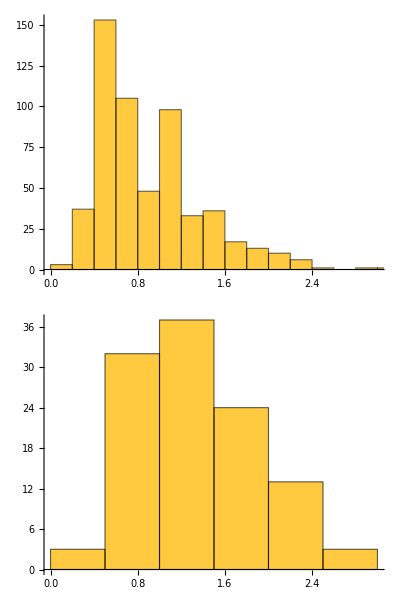

```mathematica
Grid[{{Histogram[lssage[getp[#]]-lssage[#]&/@VertexList[skeleton,v_/;v=!=1&&boh[v]>2],PlotRange->{{0,3},Automatic}]},
{Histogram[lssage[getp[#]]-lssage[#]&/@VertexList[skeletont,v_/;boh[v]>2],PlotRange->{{0,3},Automatic}]}}]
```

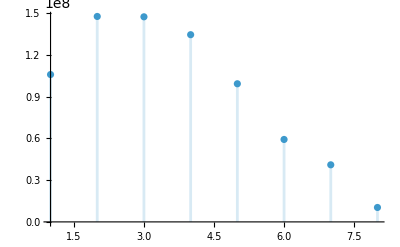

```mathematica
DiscretePlot[Total[VertexList[gr,(v_/;branchorder[v]==z):>getpl[v]getpw[v]^2]],{z,branchorder[1]}]
```

```mathematica
BoxWhiskerChart[Table[VertexList[gr,(v_/;branchorder[v]==z&&getz[v]>0):>getpl[v]/getpw[v]],{z,1,branchorder[1]}],ChartLabels->Range[branchorder[1]],FrameLabel->{"Branch order, w","Length-to-diameter ratio"},AspectRatio->1,FrameStyle->Black,LabelStyle->{Black,FontSize->6.4},ImageSize->120]
```

-Graphics-

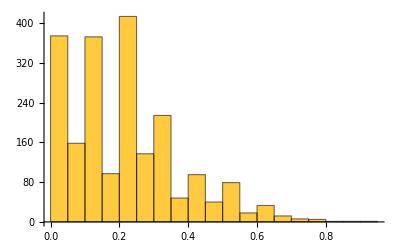

```mathematica
Histogram[Table[DeleteCases[Module[{u=VertexOutComponent[tg,v,{1}]},If[Length[u]==2,Abs[1-2/(1+Count[VertexOutComponent[tg,u[[1]]],i_/;MemberQ[ends,i]]/Count[VertexOutComponent[tg,u[[2]]],i_/;MemberQ[ends,i]])]]],Null],{v,VertexList[gr,v_/;boh[v]>3]}]]
```

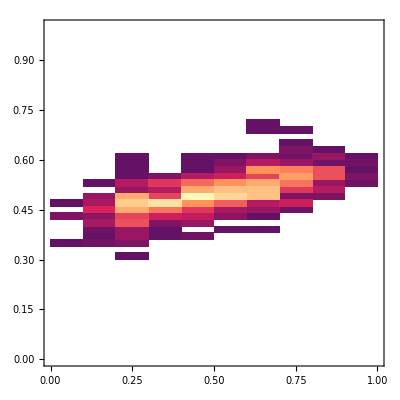

```mathematica
DensityHistogram[DeleteCases[Table[Module[{u=VertexOutComponent[tg,v,{1}]},If[Length[u]==2,{1/(1+Count[VertexOutComponent[tg,u[[1]]],i_/;MemberQ[ends,i]]/Count[VertexOutComponent[tg,u[[2]]],i_/;MemberQ[ends,i]]),
1/(1+(getpw[u[[1]]]/getpw[u[[2]]])^1)}]],{v,VertexList[gr,v_/;boh[v]>3]}],Null],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
fit=LinearModelFit[DeleteCases[Table[Module[{u=VertexOutComponent[tg,v,{1}]},If[Length[u]==2,{1/(1+Count[VertexOutComponent[tg,u[[1]]],i_/;MemberQ[ends,i]]/Count[VertexOutComponent[tg,u[[2]]],i_/;MemberQ[ends,i]]),
1/(1+(getpw[u[[1]]]/getpw[u[[2]]])^1)}]],{v,VertexList[gr,v_/;boh[v]>3]}],Null],x,x]
```

FittedModel[…]

```mathematica
EdgeCount[gr]/13434//N
```

0.281822

```mathematica
Table[Around[Mean[#],se[#]]&[VertexList[gr,(v_/;boh[v]==wh):>(Abs[boh[#[[1]]]-boh[#[[2]]]]&[VertexOutComponent[tg,v,{1}]])]],{wh,2,boh[1]}]
```

{0,0.4930.013,0.6160.021,0.8360.032,1.070.05,1.290.07,1.470.10,1.680.14,1.790.16,2.720.23,2.650.31,3.20.4,2.70.6,3.01.0,2.21.1,3.01.2,6.01.0,2.50.5,4.01.0,3Null,1Null}

```mathematica
eh3549={0,0.640.05,1.060.08,1.360.16,2.000.26,2.410.31,2.20.4,2.10.4,3.51.1,4.80.8,2.01.2,2.670.33,3Null,1Null,2Null};
```

```mathematica
eh3685={0,0.6960.030,0.930.06,1.260.09,1.460.14,1.670.17,1.770.32,2.310.29,2.70.6,2.30.6,3.250.25,2.30.8,3.81.1,0Null,1Null};
```

```mathematica
gw11={0,0.6690.025,0.990.05,1.310.09,1.600.12,2.130.14,1.870.25,2.640.35,3.10.4,3.20.4,4.41.0,4.71.2,5.62.0,3.31.1,4.01.1,1.51.5,1Null,1Null};
```

```mathematica
eh4452={0,0.6680.029,1.080.05,1.270.09,1.800.10,1.640.17,2.840.22,2.60.4,2.20.4,3.80.7,4.00.5,4.30.8,3.20.8,2.52.5,6.02.0,2,0Null};
```

```mathematica
eh3138={0,0.5910.023,0.910.04,1.060.06,1.230.09,1.420.12,1.830.17,1.760.25,1.880.29,2.20.4,2.30.6,2.80.7,2.50.9,1.71.2,3.50.5,0Null,2Null};
```

```mathematica
eh3822={0,0.4930.013,0.6160.021,0.8360.032,1.070.05,1.290.07,1.470.10,1.680.14,1.790.16,2.720.23,2.650.31,3.20.4,2.70.6,3.01.0,2.21.1,3.01.2,6.01.0,2.50.5,4.01.0,3Null,1Null};
```

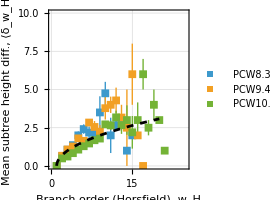

```mathematica
Show[ListPlot[{eh3549,eh4452,eh3822},AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"Branch order (Horsfield), w_H","Mean subtree height diff., ⟨δ_w_H⟩"},LabelStyle->Directive[Black,FontSize[6.4]],PlotMarkers->{"■",8},FrameStyle->Black,ImageSize->200,PlotRange->{{0,25},{0,10}},PlotLegends->Placed[{"PCW8.3","PCW9.4","PCW10.2"},{Left,Top}]],Plot[√((x-1)/2),{x,0,20},PlotStyle->{Black,Dashed}]]
```

```mathematica
{Mean[getpl/@ends2],StandardDeviation[getpl/@ends2]}
```

{61.5998,20.4829}

```mathematica
{EdgeCount[gr],Length[ends],Mean[getz/@ends]//N,StandardDeviation[getz/@ends]//N,VertexEccentricity[gr,1],Mean[getpl/@ends],Mean[getpw/@ends],Mean[getpl/@ends2],Mean[getpw/@ends2],Total[getpl/@VertexList[gr]],voxel^3 Volume[ConvexHullMesh[xyz]],voxel BoundingRegion[xyz,"MinBall"][[2]],Mean[ltoroot/@ends],StandardDeviation[ltoroot/@ends],EstimatedDistribution[ltoroot/@ends,LogNormalDistribution[a,b]],EstimatedDistribution[getz/@ends,LogNormalDistribution[a,b]]}//Column
```

{ | Estimate | Standard Error | Confidence Interval
1 | 611.845 | 22.9028 | {566.954,656.736}
x | 268.44 | 1.43779 | {265.622,271.258},0.601695}

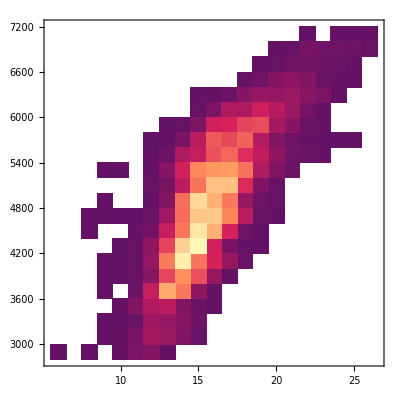

```mathematica
data=Table[{getz[i],ltoroot[i]},{i,ends}];
{pcit[#],r2[#]}&[LinearModelFit[data,x,x]]
DensityHistogram[data]
```

```mathematica
ages={5.7,6.1,6.1,6.1,6.3,6.6,6.6,6.6,7,7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
slopes={-26,18,69,-34,261,226,61,50,54,141,63,152,173,168,182,163,139,213,189,237,206,137,189,205,229,151,163,198,237,189,213,249,268};
errs={75,50,23,37,49,44,13,22,34,23,27,19,9,8,8,11,14,5,8,7,6,3,4,6,5,4,6,3,3,2,2,2,1};
```

```mathematica
ListPlot[MapThread[{#1,Around[#2,2#3]}&,{ages,slopes,errs}],graphsettings,PlotMarkers->{"OpenMarkers",3},ImageSize->120,LabelStyle->{Black,FontSize->11.2},FrameLabel->{"Age PCW","Slope μm per z"},PlotRange->{{4,14},{-200,400}}]
```

-Graphics-

```mathematica
x0=Mean[xyz];
Graphics3D[Table[{Cyan,Tube[{xyz[[i]]-x0,xyz[[getp[i]]]-x0},3]},{i,VertexList[gr,Except[1]]}],PlotRange->200,SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic"]
```

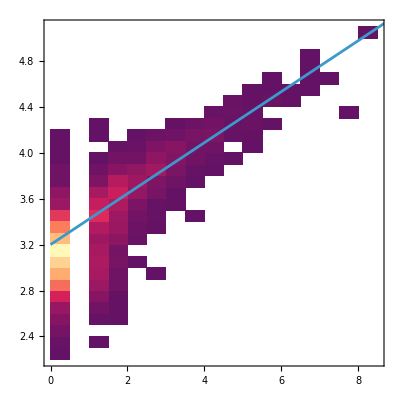

```mathematica
Show[DensityHistogram[VertexList[gr,(v_):>{Log@Length[VertexOutComponent[tg,v]],Log@getpw[v]}]],Plot[3.2+x/4.5,{x,0,9}]]
```

```mathematica
1/Log[2,0.84]-1/Log[2,0.83]
```

-0.255524

```mathematica
1/Log[2,0.84]-1/Log[2,0.85]
```

0.289494

### Radial orientation analysis

```mathematica
x0=Mean[xyz[[#]]&/@ends];
```

```mathematica
Show[Histogram[Table[ArcCos[align[xyz[[e]]-xyz[[getp[e]]],xyz[[getp[e]]]-xyz[[1]]]]/Degree,{e,ends}],{0,180,20},"PDF"],Plot[Degree/2 Sin[x Degree],{x,0,180}]]
```

```mathematica
Show[Histogram[{Table[ArcCos[align[xyz[[e]]-xyz[[getp[e]]],xyz[[e]]-xyz[[1]]]]/Degree,{e,srftips}],Table[ArcCos[align[xyz[[e]]-xyz[[getp[e]]],xyz[[e]]-xyz[[1]]]]/Degree,{e,blktips}]},Automatic,"PDF"],Plot[Degree/2 Sin[x Degree],{x,0,180}]]
```

### Number of branches vs Strahler order

```mathematica
eh2987=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
```

```mathematica
eh4309=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
```

```mathematica
eh4310=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
```

```mathematica
eh4437=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
```

```mathematica
eh3822=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
```

```mathematica
fit1=LinearModelFit[Log10[eh2987],x,x];
fit2=LinearModelFit[Log10[eh4309],x,x];
fit3=LinearModelFit[Log10[eh4310],x,x];
fit4=LinearModelFit[Log10[eh4437],x,x];
fit5=LinearModelFit[Log10[eh3822],x,x];
```

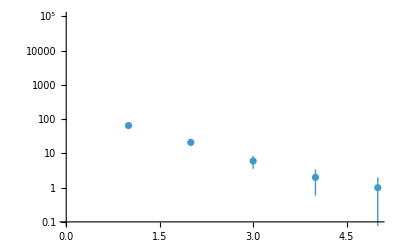

```mathematica
data=(Sort@Tally@VertexList[gr,(v_/;branchorder[v]<branchorder[getp[v]]||getp[v]==Null):>branchorder[v]])[[All,2]];
ListLogPlot[Around[#,Sqrt[#]]&/@data,PlotRange->{10^-1,10^5}]
```

```mathematica
mousel=data;
```

```mathematica
mousers=data;
```

```mathematica
mouseri=data;
```

```mathematica
mouserm=data;
```

```mathematica
mousera=data;
```

```mathematica
Show[ListPlot[{mousel,mousers,mouseri,mouserm,mousera},PlotMarkers->{"■",6},ScalingFunctions->"Log10",graphsettings,ImageSize->120,PlotRange->{{0,8},{10^-1,10^3}},PlotLegends->Placed[{"Left","Right superior","Right inferior","Right middle","Right accessory"},Right],Joined->True],Plot[10^3 3^-z,{z,1,6},ScalingFunctions->"Log10",PlotStyle->{Black,Dashed}]]
```

-Graphics-

```mathematica
Show[ListPlot[{mousel,eh4310},PlotMarkers->{"■",8},ScalingFunctions->"Log10",graphsettings,ImageSize->120,PlotRange->{{0,8},{10^-1,10^3}},FrameLabel->{"Branch order, w","Number of branches, n_w"},PlotLegends->Placed[{"Mouse","Human"},{Right,Top}]],ListLinePlot[{Table[{x,Exp[bfa[fit2]]},{x,1,6,0.1}],Table[{x,Exp[bfa[fit1]]},{x,1,7,0.1}]},ScalingFunctions->"Log10",IntervalMarkers->"Bands",PlotStyle->Thickness[0.01]]]
```

-Graphics-

```mathematica
data=mousel;
fit2 =LinearModelFit[Log@data,x,x];
fit["ParameterEstimates"]
Exp[Around[-fit["ParameterEstimates"][[2]][[2]],fit["ParameterEstimates"][[2]][[3]]]]
```

2.560.08

```mathematica
Exp[Around[0.93922,0.0321333]]
```

2.560.08

```mathematica
r2[fit1]
```

0.994181

```mathematica
pcit[fit1]
```

| Estimate | Standard Error | Confidence Interval
1 | 6.34493 | 0.143704 | {5.97553,6.71434}
x | -0.93922 | 0.0321333 | {-1.02182,-0.856619}

```mathematica
Exp[Around[1.12264,0.0457405]]
```

3.070.14

```mathematica
r2[fit2]
```

0.993404

```mathematica
pcit[fit2]
```

| Estimate | Standard Error | Confidence Interval
1 | 6.48895 | 0.178134 | {5.99437,6.98353}
x | -1.12264 | 0.0457405 | {-1.24963,-0.995643}

```mathematica
Show[ListPlot[{eh2987,eh4309,eh4310,eh4437,eh3822},
Joined->False,PlotMarkers->"■",
ScalingFunctions->"Log10",AspectRatio->1,GridLines->Automatic,
Frame->True,FrameStyle->Black,FrameLabel->{"Branch order, w","Number of branches, n_w"},LabelStyle->{Black,FontSize->20},
PlotLegends->{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"}],
Plot[{fit1[x],fit2[x],fit3[x],fit4[x],fit5[x]},{x,1,11},PlotRange->{0,10},PlotStyle->Dashed]]
```

```mathematica
ages={6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
branchingratios={2.68,2.31,2.643,2.73,2.56,2.63,2.441,2.51,2.552,2.687,2.74,2.57,2.477,2.504,2.482,2.52,2.587,2.587,2.483,2.7,2.651,2.725,2.74};
errs={0.11,0.05,0.025,0.07,0.08,0.04,0.029,0.05,0.021,0.021,0.021,0.06,0.032,0.029,0.024,0.04,0.02,0.032,0.031,0.05,0.035,0.031,0.04};bo1={5,7,7,7,7,7,8,8,8,8,8,9,9,9,9,9,9,10,11,10,11,11,11};
```

```mathematica
terr=InverseCDF[StudentTDistribution[#],1-0.05/2]&;
```

```mathematica
CDF[ChiSquareDistribution[Length[branchingratios]],Total[((branchingratios-Mean[branchingratios])/errs)^2]]
```

1.

```mathematica
Total[((branchingratios-m)/errs)^2]
```

243.682

```mathematica
MapThread[{#4,Around[#1,#2 terr[#3-2]]}&,{branchingratios,errs,bo1,ages}]]
```

```mathematica
Show[ListPlot[MapThread[{#1,#2}&,{ages,branchingratios}],PlotMarkers->{"OpenMarkers",3},graphsettings,FrameLabel->{"Age (PCW)","Branching ratio, R_b"},
PlotRange->{{6,14},{2.0,3.2}},ImageSize->120],
ListLinePlot[Table[{x,Around[2.59,0.05]},{x,6,14}],IntervalMarkers->"Bands",PlotStyle->Thickness[0.008]]]
```

-Graphics-

```mathematica
LinearModelFit[{ages,branchingratios}ᵀ,1,x]["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 2.58735 | 0.0234539 | {2.53871,2.63599}

```mathematica
InverseCDF[StudentTDistribution[Length[branchingratios]-2],1-0.025]se[branchingratios]
```

0.0487751

```mathematica
hmndata=Table[Count[ends,v_/;getz[v]==z],{z,VertexEccentricity[tg,1]}];
```

```mathematica
mousdata=hmndata;
```

```mathematica
ListPlot[{mousdata,hmndata},PlotMarkers->{"■",8},graphsettings,ImageSize->120,PlotRange->{{0,20},{0,100}},FrameLabel->{"Generation, z","Number of tips, m_z"},PlotLegends->Placed[{"Mouse","Human"},{Right,Top}]]
```

-Graphics-

### Separate B1,2,3,4,5

```mathematica
{Length[#],Max[getz/@#],Min[getz/@#],Mean[getz/@#],StandardDeviation[getz/@#],Max[ltoroot/@#],Mean[ltoroot/@#],StandardDeviation[ltoroot/@#]}&/@(Intersection[VertexOutComponent[tg,#],ends]&/@VertexList[gr,v_/;getz[v]==2])//N
```

```mathematica
SmoothHistogram[((getz/@Intersection[VertexOutComponent[tg,#],ends]))&/@VertexList[gr,v_/;getz[v]==2]]
```

```mathematica
skelgraphics[Subgraph[gr,VertexOutComponent[tg,VertexList[gr,v_/;getz[v]==2][[4]]]]]
```

```mathematica
Table[Max[getz/@VertexOutComponent[tg,w]],{w,VertexList[gr,v_/;getz[v]==2]}]
```

```mathematica
Table[Count[VertexOutComponent[tg,w],u_/;MemberQ[srftips,u]]/Count[VertexOutComponent[tg,w],u_/;MemberQ[ends,u]],{w,VertexList[gr,v_/;getz[v]==2]}]//N
```

```mathematica
SmoothHistogram[(ltoroot/@Intersection[VertexOutComponent[tg,#],ends])&/@VertexList[gr,v_/;getz[v]==2]]
```

```mathematica
SmoothHistogram[(getz/@Intersection[VertexOutComponent[tg,#],ends])&/@VertexList[gr,v_/;getz[v]==2]]
```

```mathematica
Max/@((getz/@Intersection[VertexOutComponent[tg,#],ends])&/@VertexList[gr,v_/;getz[v]==2])
```

```mathematica
N@2Log2[Length[#]]&/@((getz/@Intersection[VertexOutComponent[tg,#],ends])&/@VertexList[gr,v_/;getz[v]==2])
```

```mathematica
pars=VertexList[gr,v_/;getz[v]==2];
```

```mathematica
Graphics3D[{
Table[{Orange,Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexOutComponent[tg,pars[[1]]]}],
Table[{Yellow,Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexOutComponent[tg,pars[[2]]]}],
Table[{Red,Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexOutComponent[tg,{pars[[3]],pars[[4]]}]}],
Table[{Blue,Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexOutComponent[tg,{pars[[5]],pars[[6]]}]}]
},SphericalRegion->True,Boxed->False]
```

-Graphics3D-

```mathematica
ListPlot[Sort[Tally[Cases[VertexOutComponent[tg,#],(v_/;VertexDegree[gr,v]==1):>getz[v]]]]&/@{{pars[[3]],pars[[4]]},{pars[[5]],pars[[6]]},pars[[1]],pars[[2]]},Joined->True,PlotMarkers->{"■",8},graphsettings,ImageSize->125,ScalingFunctions->"Log10",PlotStyle->{Red,Blue,Yellow,Orange},PlotRange->{{4,16},{10^-1,10^3}},FrameLabel->{"Generation, z","Number of tips, mz"},PlotLegends->Placed[{"Branch 1&2","Branch 3","Branch 4","Branch 5"},Right]]
```

-Graphics-

### Imbalance measures

Subtree depth

```mathematica
ListPlot[Sort@Tally@VertexList[gr,(v_/;VertexDegree[gr,v]==3):>
Abs[VertexEccentricity[tg,First@VertexOutComponent[tg,v,{1}]]-VertexEccentricity[tg,Last@VertexOutComponent[tg,v,{1}]]]],
ScalingFunctions->"Log10"]
```

```mathematica
DensityHistogram[VertexList[gr,(v_/;VertexDegree[gr,v]==3):>{VertexEccentricity[tg,v],
Abs[VertexEccentricity[tg,First@VertexOutComponent[tg,v,{1}]]-VertexEccentricity[tg,Last@VertexOutComponent[tg,v,{1}]]]}]]
```

Subtree entropy

```mathematica
pairent[n1_,n2_]:=-(n1/(n1+n2)Log2[n1/(n1+n2)]+n2/(n1+n2)Log2[n2/(n1+n2)]);
```

```mathematica
Histogram[VertexList[gr,(v_/;VertexDegree[gr,v]==3):>
pairent@@(Length@VertexOutComponent[tg,#]&/@VertexOutComponent[tg,v,{1}])]]
```

```mathematica
Histogram[VertexList[g,(v_/;VertexDegree[g,v]==3):>
pairent@@(Length@VertexOutComponent[g,#]&/@VertexOutComponent[g,v,{1}])]]
```

```mathematica
DensityHistogram[VertexList[gr,(v_/;VertexDegree[gr,v]==3):>
{boh[v],pairent@@(Length@VertexOutComponent[tg,#]&/@VertexOutComponent[tg,v,{1}])}]]
```

```mathematica
Total[VertexList[tg,(v_/;VertexOutDegree[tg,v]==2):>
pairent@@(Length@VertexOutComponent[tg,#]&/@VertexOutComponent[tg,v,{1}])]]/VertexCount[tg,(v_/;VertexOutDegree[tg,v]==2)]//N
```

```mathematica
Total[VertexList[g,(v_/;VertexOutDegree[g,v]==2):>
pairent@@(Length@VertexOutComponent[g,#]&/@VertexOutComponent[g,v,{1}])]]/VertexCount[g,(v_/;VertexOutDegree[g,v]==2)]//N
```

Leaf entropy

```mathematica
leafprob[v_]:=1/Exp@Total@Log@(Length[VertexOutComponent[tg,#,{1}]]&/@VertexInComponent[tg,v][[2;;]]);
```

```mathematica
leafent[v_]:=-leafprob[v]Log2[leafprob[v]];
```

```mathematica
Log2[Length[ends]]-Sum[leafent[i],{i,ends}]//N
```

```mathematica
leafprobr[v_]:=(1/3)2^(-rgetz[v]+1);
```

```mathematica
leafentr[v_]:=-leafprobr[v]Log2[leafprobr[v]];
```

```mathematica
Log2[Length[rends]]-Sum[leafentr[i],{i,rends}]//N
```

### Tip-to-root length diagram

```mathematica
Graphics3D[{
Table[{Thickness->0.010,Red,Line[{7xyz[[v]],7xyz[[getp[v]]]}]},{v,VertexInComponent[tg,ends[[660]]][[;;-2]]}],
Table[{Thickness->0.003,Black,Line[{7xyz[[v]],7xyz[[getp[v]]]}]},{v,VertexList[gr,w_/;getz[w]>=1]}]
},Boxed->False,SphericalRegion->True]
```

```mathematica
Graphics3D[{
Table[{Thickness->0.010,Red,Line[{7xyz[[v]],7xyz[[getp[v]]]}]},{v,VertexInComponent[tg,ends[[660]]][[;;-2]]}]
},Boxed->False,SphericalRegion->True]
```

### L-to-root histograms

```mathematica
dist=EstimatedDistribution[ltoroot/@ends,LogNormalDistribution[a,b]]
```

```mathematica
eh2987=ltoroot/@ends;
```

```mathematica
eh4309=ltoroot/@ends;
```

```mathematica
eh4310=ltoroot/@ends;
```

```mathematica
eh4437=ltoroot/@ends;
```

```mathematica
eh3822=ltoroot/@ends;
```

```mathematica
dist1=EstimatedDistribution[eh2987,LogNormalDistribution[a,b]];
dist2=EstimatedDistribution[eh4309,LogNormalDistribution[a,b]];
dist3=EstimatedDistribution[eh4310,LogNormalDistribution[a,b]];
dist4=EstimatedDistribution[eh4437,LogNormalDistribution[a,b]];
dist5=EstimatedDistribution[eh3822,LogNormalDistribution[a,b]];
```

```mathematica
Show[SmoothHistogram[{eh2987,eh4309,eh4310,eh4437,eh3822},ScalingFunctions->"Log",PlotRange->{{0,7000},{10^-5,0.005}},
Frame->True,GridLines->Automatic,AspectRatio->1,LabelStyle->{Medium,Black},FrameLabel->{"Tip-to-root length (μm)","Probability"}],
LogPlot[Evaluate[PDF[#,x]&/@{dist1,dist2,dist3,dist4,dist5}],{x,0,7000},PlotStyle->Dashed]]
```

### Convex hull analysis

#### Collective

```mathematica
ages={7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6};
srflens={192,169,154,173,136,140,139,156,134,134,110,130,131,113,105,110,96,83,72,69,69};
srfwids={98,84,85,75,75,95,75,87,75,85,75,74,89,81,72,79,75,72,70,72,72};
blklens={122,106,88,101,108,100,93,100,92,92,78,86,82,82,72,82,67,64,57,56,56};
blkwids={84,73,74,66,68,86,65,78,68,71,72,67,80,73,67,73,70,68,69,71,68};
```

```mathematica
ListPlot[{{ages,srfwids}ᵀ,{ages,blkwids}ᵀ},Frame->True,FrameLabel->{"Age (PCW)","Mean tip diameter (μm)"},LabelStyle->{Black,FontSize->20},GridLines->Automatic,AspectRatio->1,PlotMarkers->"OpenMarkers",PlotLegends->Placed[{"surface tips","bulk tips"},{Right,Top}]]
```

#### Single

```mathematica
(*ccvhl=ConvexHullMesh[xyz];*)
(*ccvhl=ConcaveHullMesh[xyz];*)
ccvhl=ConcaveHullMesh[xyz];
x0=RegionCentroid[ccvhl];
v0=Volume[ccvhl];
voxel^3 v0
ccvhlsrf=RegionBoundary[ccvhl];
voxel^2 Area[ccvhlsrf]
srftips=Cases[ends,i_/;RegionMember[ccvhlsrf,xyz[[i]]]];
blktips=Complement[ends,srftips];
(*inner=Scale[ccvhl,0.5,x0];*)
(*blktips=Cases[ends,i_/;RegionMember[inner,xyz[[i]]]];*)
Length[srftips]
skeleton=Subgraph[gr,VertexInComponent[tg,srftips]];
skeletont=Subgraph[gr,Complement[VertexList[gr],VertexInComponent[tg,srftips]]];
```

6.49561×10^9

2.59491×10^7

465

```mathematica
(π^(1/3) (6v0)^(2/3))/Area[ccvhlsrf]
```

0.703342

```mathematica
cvxhl=ConvexHullMesh[xyz];
```

```mathematica
Show[skelgraphics[gr],Translate[cvxhl,{0,-500,0}],Translate[ccvhl,{0,-1000,0}]]
```

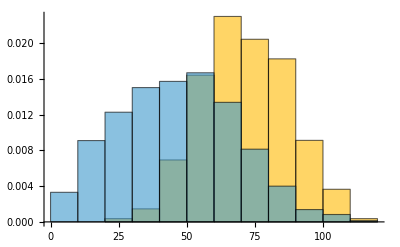

```mathematica
Histogram[
{VertexList[skeletont,(v_/;branchorder[v]>1&&getz[v]>2):>(ArcCos[Dot[#1,#2]/(Norm[#1]Norm[#2])]/Degree&[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp@getp@v]]])],VertexList[skeleton,(v_/;branchorder[v]>1&&getz[v]>2):>(ArcCos[Dot[#1,#2]/(Norm[#1]Norm[#2])]/Degree&[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp@getp@v]]])]},Automatic,"PDF"
]
```

```mathematica
newhl
```

```mathematica
wco=2;
x0=Mean[xyz];
Graphics3D[{
Table[{Red,Tube[{xyz[[i]]-x0,xyz[[getp[i]]]-x0},5]},{i,VertexList[skeleton,v_/;branchorder[v]>wco&&Not[v==1]]}],
Table[{Red,Thickness[0.002],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[skeleton,v_/;branchorder[v]<=wco]}],
(*Table[{Blue,Thickness[0.005],Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexList[skeletont,v_/;branchorder[v]>wco]}],*)
Table[{Blue,Thickness[0.002],Line[{xyz[[i]]-x0,xyz[[getp[i]]]-x0}]},{i,VertexList[skeletont,v_/;branchorder[v]<=100]}]
},Epilog->Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.3,0.2}],{Left,Bottom},0.119],Boxed->False,SphericalRegion->True,PlotRange->300,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
wco=2;
x0=Mean[xyz];
Graphics3D[{
Table[{Red,Tube[{xyz[[i]]-x0,xyz[[getp[i]]]-x0},3]},{i,VertexList[skeleton,Except[1]]}],
(*Table[{Blue,Thickness[0.005],Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexList[skeletont,v_/;branchorder[v]>wco]}],*)
Table[{Blue,Tube[{xyz[[i]]-x0,xyz[[getp[i]]]-x0},3]},{i,VertexList[skeletont]}]
},Epilog->Inset[Graphics[{Black,Rectangle[{0,0},{10,1}]}],
Scaled[{0.3,0.2}],{Left,Bottom},0.119],Boxed->False,SphericalRegion->True,PlotRange->300,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
Graphics3D[{Table[{If[MemberQ[srftips,i],Thickness[0.005],Thickness[0.002]],Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexList[gr,Except[1]]}],
Table[{Red,PointSize[0.01],Point[xyz[[i]]]},{i,srftips}]},
SphericalRegion->True,Boxed->False,ViewProjection->"Orthographic"]
```

-Graphics3D-

```mathematica
Show[Graphics3D[Translate[Table[{Thickness[0.003],Line[{xyz[[v]],xyz[[getp[v]]]}]},{v,VertexList[gr,Except[1]]}],{0,500,0}],SphericalRegion->True,Boxed->False],ccvhl,ViewProjection->"Orthographic"]
```

-Graphics3D-

#### Last surface ancestor

```mathematica
lsa[i_]:=First[Select[VertexInComponent[tg,i],MemberQ[VertexList[skeleton],#]&]];
data=Table[{getz[i]-getz[lsa[i]],getz[lsa[i]]},{i,ends}];
fit=LinearModelFit[data,n,n];
fit["RSquared"]
pcit[fit]
Show[DensityHistogram[data,PlotRange->{{-2,10},{0,25}},FrameStyle->Black,FrameLabel->{"Generations as bulk tip, zbulk","Generations as surface tip, zsrf."},LabelStyle->{Black,FontSize->6.4},GridLines->Automatic,ImageSize->115,PlotRangePadding->None,ColorFunction->ColorData[{"TemperatureMap",{0.5,-0.5}}],ChartLegends->Placed[BarLegend[{Automatic,{0,0.5}},LegendMarkerSize->50,LegendLabel->Placed["Probability",Left,Rotate[#,90°]&]],{Right,Top}]],ListLinePlot[Table[{n,fit["BestFitAround"]},{n,0,5,0.1}],IntervalMarkers->"Bands",PlotStyle->Black]]
```

0.617595

| Estimate | Standard Error | Confidence Interval
1 | 11.34 | 0.0651469 | {11.2122,11.4678}
n | -1.3652 | 0.0303602 | {-1.42476,-1.30564}

-Graphics-

```mathematica
vals=Table[If[Length[#]>0,Around[Mean[#],se[#]]]&@Cases[data,(x_/;x[[1]]==i):>x[[2]]],{i,0,20}];
fit=LinearModelFit[DeleteCases[vals[[;;8]],Null],n,n];
r2[fit]
pcit[fit]
```

```mathematica
data=Table[{ltoroot[i]-ltoroot[lsa[i]],ltoroot[lsa[i]]},{i,ends}];
(*vals=Table[If[Length[#]>0,Around[Mean[#],se[#]]]&@Cases[data,(x_/;x[[1]]==i):>x[[2]]],{i,0,20}];*)
fit=LinearModelFit[data,n,n];
r2[fit]
pcit[fit]
(*Show[DensityHistogram[data],Plot[fit[n],{n,0,1000},PlotStyle->Red]]*)
```

0.347753

| Estimate | Standard Error | Confidence Interval
1 | 5174.41 | 7.87985 | {5158.96,5189.85}
n | -1.94267 | 0.0175145 | {-1.977,-1.90834}

```mathematica
{ages,slopes,errs}={{7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12},{1.24,1.58,1.4,1.43,1.42,1.28,1.46,1.36,1.36,1.46,1.49,1.37,1.39,1.31,1.44,1.24,1.49,1.25,1.41,1.43,1.339,1.348},{0.13,0.08,0.08,0.1,0.07,0.06,0.05,0.04,0.03,0.03,0.03,0.03,0.02,0.02,0.03,0.02,0.02,0.01,0.01,0.01,0.006,0.005}};
```

```mathematica
fit=LinearModelFit[Transpose[{ages,slopes}],1,x];
```

```mathematica
pcit[fit]
```

| Estimate | Standard Error | Confidence Interval
1 | 1.38623 | 0.018746 | {1.34724,1.42521}

```mathematica
Show[ListPlot[MapThread[{#1,Around[#2,#3]}&,{ages,slopes,errs}],graphsettings,PlotMarkers->{"OpenMarkers",3},ImageSize->120,LabelStyle->{Black,FontSize->6.4},FrameLabel->{"Age (PCW)","Bulk z-surface z slope"},PlotRange->{{7,13},{1.0,1.8}}],
ListLinePlot[Table[{x,fit["BestFitAround"]},{x,Min[ages],Max[ages],0.2}],IntervalMarkers->"Bands"]]
```

-Graphics-

#### Distribution Fit Tests

```mathematica
data=getpl/@ends;
dist=EstimatedDistribution[data,GammaDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=getpl/@ends2;
dist=EstimatedDistribution[data,LogLogisticDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=getpl/@ends;
dist=EstimatedDistribution[data,LogNormalDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=getz/@ends;
dist=EstimatedDistribution[data,GammaDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=getz/@ends;
dist=EstimatedDistribution[data,LogNormalDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=ltoroot/@ends;
dist=EstimatedDistribution[data,GammaDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

```mathematica
data=ltoroot/@ends;
dist=EstimatedDistribution[data,LogNormalDistribution[a,b]];
Table[f[data,dist,"TestStatistic"],{f,{KolmogorovSmirnovTest,CramerVonMisesTest,AndersonDarlingTest}}]
```

Export[StringJoin[path, "tips.csv"], {getz /@ #, MemberQ[srftips, #] & /@ #, getpl /@ #, getpw /@ #, ltoroot /@ #} &[ends]];
Export[StringJoin[path, "tips2.csv"], {getz /@ #, MemberQ[VertexList[skeleton], #] & /@ #, getpl /@ #, getpw /@ #, ltoroot /@ #} &[ends2]];

```mathematica
tips2=getpl/@VertexList[skeleton,v_/;branchorder[v]==2];
```

```mathematica
dist=EstimatedDistribution[tips2,LogLogisticDistribution[a,b]];
{KolmogorovSmirnovTest[tips2,#,"TestStatistic"],CramerVonMisesTest[tips2,#,"TestStatistic"],AndersonDarlingTest[tips2,#,"TestStatistic"],2 2-LogLikelihood[#,tips2]}&[dist]
```

```mathematica
dist=EstimatedDistribution[tips2,GammaDistribution[a,b]];
{KolmogorovSmirnovTest[tips2,#,"TestStatistic"],CramerVonMisesTest[tips2,#,"TestStatistic"],AndersonDarlingTest[tips2,#,"TestStatistic"],2 2-LogLikelihood[#,tips2]}&[dist]
```

```mathematica
dist=EstimatedDistribution[tips2,NormalDistribution[a,b]];
{KolmogorovSmirnovTest[tips2,#,"TestStatistic"],CramerVonMisesTest[tips2,#,"TestStatistic"],AndersonDarlingTest[tips2,#,"TestStatistic"],2 2-LogLikelihood[#,tips2]}&[dist]
```

```mathematica
dist=EstimatedDistribution[tips2,WeibullDistribution[a,b,c]];
{KolmogorovSmirnovTest[tips2,#,"TestStatistic"],CramerVonMisesTest[tips2,#,"TestStatistic"],AndersonDarlingTest[tips2,#,"TestStatistic"],2 3-LogLikelihood[#,tips2]}&[dist]
```

```mathematica
Show[Histogram[tips2,Automatic,"PDF",ScalingFunctions->"Log"],LogPlot[{PDF[dist,x],PDF[dist2,x]},{x,10,400}]]
```

#### Random point analysis

```mathematica
datax={3,7,9,13,18,14,22,22,21,46,55,145,349,360,243,361,500,545,760,1019,1143,1508,1254,1403,1594,1652,2010,4127,6780,8722,12393,21027,23081};
datay={3,6,7,13,18,12,22,21,21,46,52,108,209,229,160,228,277,297,342,465,518,608,512,537,682,654,748,1342,1719,1789,2376,3308,3501};
```

```mathematica
data=Table[{Floor[5 10^i],Module[{rpoints=RandomPoint[ccvhl,Floor[5 10^i]],rccvhl,rsrf},
rccvhl=ConcaveHullMesh[rpoints];
rsrf=RegionBoundary[rccvhl];
Count[rpoints,x_/;RegionMember[rsrf,x]]]},{i,0,3+1/3,1/3}];
```

```mathematica
ListLogLogPlot[{data,{datax,datay}ᵀ},Joined->{True,False}]
```

```mathematica
LinearModelFit[Log[data[[2;;]]],x,x]
```

```mathematica
rpoints=RandomPoint[ccvhl,1000];
rccvhl=ConcaveHullMesh[rpoints];
rx0=RegionCentroid[rccvhl];
rv0=Volume[rccvhl];
```

```mathematica
ds=0.1;
srange=Range[ds,1,ds];
data=Table[Module[{scldhl=Scale[rccvhl,s,rx0]},Count[rpoints,x_/;RegionMember[scldhl,x]]],{s,srange}];
```

```mathematica
ListPlot[{srange,1/Length[rpoints](Around[#,√#]&/@(data-Join[{0},data[[;;-2]]]))/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,Frame->True,AspectRatio->1,PlotMarkers->{"■"},Joined->True,
GridLines->Automatic,FrameLabel->{"Scaled radial distance (a.u.)","Density (a.u.)"},LabelStyle->{Black,FontSize->20}]
```

```mathematica
Graphics3D[{Table[{Red,Tube[{xyz[[i]],xyz[[getp[i]]]},2]},{i,srftips}],
Table[{Cyan,Tube[{xyz[[i]],xyz[[getp[i]]]},2]},{i,blktips}],
Table[{Black,Tube[{xyz[[i]],xyz[[getp[i]]]},2]},{i,VertexList[gr,v_/;getz[v]>0&&branchorder[v]>1]}]
},Boxed->False,SphericalRegion->True]
```

```mathematica
Graphics3D[{
Table[{Red,Thickness[0.005],Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexList[skeleton,v_/;Not[v==1]&&branchorder[v]>=4]}],
Table[{Black,Thickness[0.005],Line[{xyz[[i]],xyz[[getp[i]]]}]},{i,VertexList[gr,Except[1]]}]
},
SphericalRegion->True,Boxed->False]
```

#### Estimating r value

Wilson score interval (CI)

```mathematica
Show[ListPlot[
Table[Module[{vers=VertexList[skeleton,v_/;getz[v]==z&&VertexDegree[gr,v]==3],p,n},n=Length[vers];p=Count[vers,w_/;VertexDegree[skeleton,w]==3]/n;
Around[(p+1.96^2/(2n))/(1+1.96^2/n),(1.96 √((p(1-p))/n+1.96^2/(4 n^2)))/(1+1.96^2/n)]],{z,VertexEccentricity[tg,1]-1}],
PlotMarkers->{"■"},Joined->True,FrameLabel->{"Branch generation","r"},
Frame->True,AspectRatio->1,GridLines->Automatic,LabelStyle->{Large,Black}
],Plot[0.6,{x,5,27},PlotStyle->Dashed]]
```

SE

```mathematica
Show[ListPlot[
Table[Module[{vers=VertexList[skeleton,v_/;getz[v]==z&&VertexDegree[skeleton,v]>1],p,n},n=Length[vers];p=Count[vers,w_/;VertexDegree[skeleton,w]==3]/n;
Around[p,√(p(1-p)/n)]],{z,VertexEccentricity[tg,1]-1}],
PlotMarkers->{"■"},Joined->True,FrameLabel->{"Branch generation","r"},
Frame->True,AspectRatio->1,GridLines->Automatic,LabelStyle->{Large,Black}
],Plot[0.6,{x,5,27},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Show[ListPlot[
Table[Module[{vers=VertexList[skeleton,v_/;getz[v]==z&&VertexDegree[skeleton,v]>1],p,n},n=Length[vers];p=Count[vers,w_/;VertexDegree[skeleton,w]==2]/n;
Around[p,√(p(1-p)/n)]],{z,VertexEccentricity[tg,1]-1}],
PlotMarkers->{"■"},Joined->True,FrameLabel->{"Branch generation","r"},
Frame->True,AspectRatio->1,GridLines->Automatic,LabelStyle->{Large,Black}
],Plot[0.6,{x,5,27},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
eh3685={1,1,0.920.08,0.820.08,0.670.07,0.570.06,0.630.05,0.490.04,0.550.04,0.690.05,0.780.06,0.830.08,1,1};
```

```mathematica
eh4452={1,1,1,1,0.600.08,0.600.06,0.500.05,0.570.04,0.460.04,0.610.04,0.550.05,0.680.06,0.710.09,0.640.13,0.860.13,1};
```

```mathematica
eh3822={1,1,1,1,0.900.05,0.680.06,0.510.05,0.530.04,0.5780.032,0.4800.026,0.4960.023,0.4960.022,0.5280.023,0.5640.027,0.580.04,0.620.05,0.780.07,0.840.08,0.880.12,1};
```

eh4452

```mathematica
VertexCount[skeleton,v_/;VertexDegree[skeleton,v]==3&&getz[v]>=5]/VertexCount[skeleton,v_/;VertexDegree[gr,v]==3&&getz[v]>=5]//N
```

0.575646

eh3822

```mathematica
VertexCount[skeleton,v_/;VertexDegree[skeleton,v]==3&&getz[v]>=5&&branchorder[v]>1]/VertexCount[skeleton,v_/;VertexDegree[skeleton,v]>1&&getz[v]>=5&&branchorder[v]>1]//N
```

0.536499

eh3685

```mathematica
VertexCount[skeleton,v_/;VertexDegree[skeleton,v]==3&&getz[v]>=5]/VertexCount[skeleton,v_/;VertexDegree[gr,v]>1&&getz[v]>=5]//N
```

0.610145

```mathematica
Show[ListPlot[{eh3822,eh4452,eh3685},Joined->True,PlotMarkers->{"■",8},graphsettings,ImageSize->120,PlotRange->{{0,20},{0,1.2}},PlotStyle->Thickness[0.01],PlotLegends->Placed[{"PCW10.2","PCW9.4","PCW8.7"},Right],FrameLabel->{"Generation, z","Surface tip bifurcation probability, r"}],
Plot[0.55,{x,5,20},PlotStyle->Directive[{Black,Dashed},Thickness[0.02]]]]
```

-Graphics-

```mathematica
rs={0.754,0.648,0.716,0.736,0.693,0.659,0.639,0.594,0.612,0.618,0.578,0.57,0.55,0.609,0.589,0.576,0.553,0.535,0.49,0.474,0.474,0.486};
```

```mathematica
ListPlot[MapThread[{#1,#2}&,{ages,rs}],graphsettings,PlotRange->{{6,14},{0,1}},PlotMarkers->{"OpenMarkers",3},ImageSize->120,FrameLabel->{"Age (PCW)","r"}]
```

-Graphics-

```mathematica
Module[{vers=VertexList[skeleton,v_/;getz[v]>=6&&VertexDegree[gr,v]==3]},Count[vers,w_/;VertexDegree[skeleton,w]==3]/Length[vers]]//N
```

```mathematica
Graphics3D[Table[Line[{xyz[[v]],xyz[[getp[v]]]}],{v,VertexList[gr,v_/;getz[v]>0]}],SphericalRegion->True,Boxed->False,ImageSize->BoundingRegion[xyz,"MinBall"][[2]]]
```

```mathematica
Graphics3D[{Table[Point[xyz[[e]]],{e,ends}],{Opacity[0.2],ConcaveHullMesh[xyz]}},SphericalRegion->True,Boxed->False,ImageSize->BoundingRegion[xyz,"MinBall"][[2]]]
```

#### Surface tips analysis

```mathematica
data1=getpl/@srftips;
data2=getpl/@blktips;
data3=getpw/@srftips;
data4=getpw/@blktips;
data5=getpw/@ends2;
dist1=EstimatedDistribution[data1,GammaDistribution[a,b]]
dist2=EstimatedDistribution[data2,GammaDistribution[a,b]]
Mean/@{data1,data2,data3,data4}
```

```mathematica
Show[Histogram[{data1,data2},Automatic,"PDF",PlotRange->Automatic,ChartLegends->Placed[{"surface tips","bulk tips"},{Right,Top}],
FrameLabel->{"Tip length (μm)","Probability distribution"},Frame->True,AspectRatio->1,GridLines->Automatic,LabelStyle->{Large,FontSize->20}],
Plot[{PDF[dist2,x],PDF[dist1,x ]},{x,0,350},PlotStyle->Dashed]]
```

#### Tails

```mathematica
dist=EmpiricalDistribution[data1];
xmin=100;xmax=400;
data=Table[{x,SurvivalFunction[dist,x]},{x,xmin,xmax}];
fit=LinearModelFit[{data[[All,1]],Log[data[[All,2]]]}ᵀ,x,x];
Grid[{{
Show[ListPlot[data,ScalingFunctions->"Linear",Joined->True,Filling->Bottom],
Plot[Exp@fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed},PlotRange->All]],
Show[ListLogPlot[data,ScalingFunctions->"Linear",Joined->True,Filling->Bottom],
LogPlot[Exp@fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed}]]}}]
-1/fit'[0]
```

#### Bulk subtrees

```mathematica
Graphics3D[{Table[{Red,Line[{xyz[[x]],xyz[[getp[x]]]}]},{x,SortBy[ConnectedComponents[skeletont],Length][[-1]]}],
Table[{Black,Line[{xyz[[x]],xyz[[getp[x]]]}]},{x,VertexList[gr,v_/;Not[v==1]]}]},SphericalRegion->True,Boxed->False]
```

```mathematica
Graphics3D[Table[{Black,Line[{xyz[[x]],xyz[[getp[x]]]}]},{x,SortBy[ConnectedComponents[skeletont],Length][[-2]]}],SphericalRegion->True,Boxed->False]
```

```mathematica
DensityHistogram[Module[{g1=SortBy[ConnectedComponents[skeletont],Length][[-6]]},Cases[g1,(v_/;VertexDegree[gr,v]==1):>{getz[v],ltoroot[v]}]]]
```

#### SS, SB, BB

```mathematica
srfsrf=Cases[ends2,(v_/;AllTrue[VertexOutComponent[tg,v,{1}],MemberQ[srftips,#]&]):>VertexOutComponent[tg,v,{1}][[;;2]]];
blkblk=Cases[ends2,(v_/;AllTrue[VertexOutComponent[tg,v,{1}],MemberQ[blktips,#]&]):>VertexOutComponent[tg,v,{1}][[;;2]]];
srfblk=Cases[ends2,(v_/;
AnyTrue[VertexOutComponent[tg,v,{1}],MemberQ[blktips,#]&]&&
AnyTrue[VertexOutComponent[tg,v,{1}],MemberQ[srftips,#]&]
):>{First[Cases[VertexOutComponent[tg,v,{1}],w_/;MemberQ[srftips,w]]],First[Cases[VertexOutComponent[tg,v,{1}],w_/;MemberQ[blktips,w]]]}];
Length/@{srfsrf,blkblk,srfblk}
```

{490,1924,507}

```mathematica
MapThread[getpl[#1]-getpl[#2]&,Transpose@srfblk]
```

#### Data

```mathematica
eh3822={-34.822841,0.,-43.023851,23.899495,-13.325366000000002,-17.248711,36.02385,53.27256200000001,-45.597927,-27.822840000000006,41.822841,-17.224913,-13.148206000000002,40.798989,-7.,56.497474999999994,26.798990000000003,6.325365999999995,7.349215999999998,-6.325364999999998,5.449773,-9.224861000000004,11.100504999999998,54.62183,7.6746339999999975,-39.272561,1.0238510000000005,-19.124356,6.3253660000000025,60.59797999999999,136.569026,40.971046999999984,20.148205999999995,28.172056999999995,21.,7.,-25.947196000000005,52.396969000000006,19.124355,7.,-21.349216000000006,-30.224861000000004,23.899494999999998,22.373067,-4.100504999999998,52.248711,-24.248710999999993,50.37306699999999,-9.899495000000016,13.674582000000001,-22.023850999999993,33.44977300000001,17.248711999999998,-2.224861000000004,-2.550278999999996,11.100505000000002,32.79893700000001,-2.5502790000000033,0.5263759999999991,65.396917,18.775139000000003,12.473571999999997,87.746186,-12.124355999999999,36.37306699999999,27.82284,-19.798990000000003,24.775086999999992,96.62183000000002,-2.2248600000000067,19.798990000000003,-37.722335,-4.449721000000004,29.02385,23.550278000000006,24.923345999999995,19.12435599999999,-5.449773,-30.396917000000002,38.248712,69.14820600000002,-9.550279000000003,131.44467,79.047701,8.023850999999993,45.248711,12.976149999999997,-30.04770099999999,188.96599600000002,15.875644000000001,8.023851000000008,111.645681,8.875644999999992,-28.,69.14820599999999,-29.722284000000002,-8.00005200000001,41.29646399999999,44.899495,31.248710999999997,7.674634000000001,12.449773,31.74618600000001,19.124356000000006,-22.698485000000005,22.87564400000001,27.82284,40.449774000000005,19.449773999999998,-7.3492160000000055,50.698485000000005,41.473624,51.722335,23.052802999999983,64.87054100000002,15.20101,-10.248711,39.621778,37.047701,36.34926899999999,-2.2248599999999996,56.84669099999999,5.124355999999992,2.0477010000000035,-2.8994950000000017,-32.597979,-27.82284,29.373066999999992,37.574077,-14.674634999999995,15.698484999999998,-4.100504999999998,50.37306699999999,0.6746339999999975,-42.497474999999994,12.798988999999999,-36.023851,1.8756440000000048,56.674634999999995,15.698484,25.248763999999994,-8.023851000000008,-21.,-2.2248610000000006,34.473624,-2.2248599999999996,11.59798,9.22486099999999,119.66953199999999,33.473572000000004,14.349215999999998,32.947196,-52.923345999999995,9.899495000000002,20.12440799999999,46.947196000000005,30.047701000000004,54.621831,-58.04770099999999,45.923345999999995,76.296465,1.5264280000000099,59.746185999999994,19.798989999999996,-9.727438000000006,4.775138999999999,21.674634999999995,83.82284,83.645681,19.798989,56.84669099999999,46.94719599999999,63.349216,-14.349215999999998,25.100505999999996,63.497474000000004,23.899494999999987,29.023849999999996,8.550227,49.172056999999995,30.899495,39.272561,29.373067,-43.34926799999998,-2.8994940000000042,8.698484999999991,-19.473572,16.899494999999987,77.52127399999999,33.473572000000004,28.698432999999994,62.822841,33.44977300000001,-13.124407999999988,-2.22486099999999,39.947197,53.09540299999999,29.023850000000003,23.899494,53.27256199999999,5.124355999999999,11.100505000000002,24.248711,-22.698485000000005,-23.40202099999999,60.59798,-31.923344999999998,175.34411400000002,64.34926800000001,18.449721000000004,-20.148205999999995,109.24366099999999,76.799042,48.822841,22.023850999999993,-9.899494999999998,9.224860000000003,20.148206000000002,-16.047700999999996,52.39696899999999,36.698485000000005,22.349269,7.6746339999999975,34.47362399999999,-19.12435500000001,42.,-3.2487119999999834,34.82284,33.798989999999996,25.947195999999998,1.0238510000000076,56.497474999999994,-7.000000000000007,93.72233500000002,13.650783999999994,5.301515000000009,28.69843200000001,29.875644,9.722335000000001,-12.449772999999993,-17.59792800000001,30.22486,45.923345000000005,48.148205999999995,8.698484999999991,36.02385,7.349215999999998,14.349215999999998,-16.899495,48.497422,37.89949499999999,9.899493999999997,-12.976149000000007,53.27256199999999,110.44467,32.597979,53.947196000000005,22.875644,-9.899494999999998,26.124356,43.698485,65.54517600000001,8.023850999999997,15.875644000000001,-7.6746339999999975,17.923345999999995,22.875643999999994,-12.976149,-2.8994950000000017,10.248711999999998,19.12435599999999,57.870541999999986,25.775140000000007,-7.6746339999999975,24.076654000000005,2.5502790000000033,47.822787999999996,14.349216000000002,1.0238509999999934,19.124356000000002,12.124355999999999,31.248711000000007,8.349269,11.597979999999993,9.923293999999999,34.822841,30.574077000000003,-1.875643999999994,23.224860999999997,-9.899495000000002,12.124355000000001,-11.775138999999996,34.148205999999995,31.574129,-9.899494999999998,25.947196000000005,41.473624,51.55027899999999,8.023851,-24.574129,16.899494999999987,14.526375999999999,33.798989000000006,3.775086999999999,64.521326,-25.248762999999997,-5.124355000000001,24.751289,54.12435599999999,-3.923346000000002,2.224860999999997,2.550278000000006,45.92334500000001,-0.5263759999999991,44.047701,-0.3492159999999984,36.698485,12.124355999999999,-36.023849999999996,7.349215999999998,28.349216999999996,42.172056000000005,-29.373067000000006,35.34921600000001,1.8756449999999987,17.248711,82.09545499999999,73.746186,76.148207,4.77514,47.12435500000001,52.047753,86.396917,-0.17715999999998644,43.87564400000001,7.,3.5741289999999992,13.148206000000002,16.047700999999996,25.248762999999997,-14.349216999999996,142.89439199999998,14.349216000000002,96.645629,46.59797999999999,19.124355,-2.2248599999999996,-7.,4.100506000000003,-20.473624,-2.8994950000000017,-15.023850999999993,97.82284000000001,27.473624,95.97099500000002,50.02385099999999,22.023850000000003,92.195907,46.272561,65.396917,-47.44977399999999,9.899494,39.947196,6.650783000000004,49.84669100000001,7.,74.42082,-40.97614899999999,37.396917,-19.798989,-21.000000000000007,118.817738,56.,-22.023851,3.775086999999992,-9.899494999999995,55.49742199999999,33.12435599999999,5.124355000000001,16.574077,-32.272562,9.224860999999997,21.,6.650782999999997,43.698484,16.396917000000016,47.296412,38.574129,-2.899494999999998,-1.8756449999999987,4.449721,-24.574129,-5.798989999999996,14.,-15.023849999999996,24.574129,-27.473624,24.923345000000005,-15.047648999999993,38.923345,8.023849999999996,21.,9.899495000000002,50.72228299999999,2.8994950000000017,9.899495000000002,23.899495,57.373067000000006,8.023849999999996,9.574077000000003,-32.100505,27.82284,-15.698484,0.3492159999999984,-31.923345000000012,72.72233500000002,33.621831,14.349217000000003,5.79899,-28.,0.3492159999999984,-6.999999999999993,16.57407699999999,20.822840999999997,-7.526375999999992,14.674635000000002,15.698485000000005,7.674635000000002,6.325365999999999,-26.449772999999993,22.023850000000003,35.497474000000004,79.373119,-14.349216000000013,8.373066999999999,21.000000000000004,-6.124407999999995,-1.0238500000000101,46.27256199999999,-22.023850000000003,26.124356000000006,10.775086999999992,9.899495000000002,42.172056000000005,4.100505000000002,33.124355,18.775139999999993,31.923345000000005,20.82284,37.373119,-37.722335,9.751236999999989,49.846692000000004,7.698432999999994,0.3254180000000133,26.621829999999996,40.971047,56.846691,29.023850000000003,22.023850999999993,-33.44977399999999,16.550278000000006,-21.349216,-0.5263759999999991,115.24360899999999,25.94719599999999,-16.899495,27.148206000000002,5.4497730000000075,-7.6746349999999985,18.44972100000001,16.22486099999999,-18.775138999999996,6.674582999999998,41.148206,22.02385,10.248711,29.72228299999999,1.2010099999999966,21.,5.124355000000001,-9.899495000000002,50.521325,9.550279000000003,-46.947197,64.52132499999999,-1.8756449999999987,3.751289,32.597979,-21.,-10.574129,53.272562,9.224861,28.172056000000005,17.248711999999998,-2.8994950000000017,2.224861000000004,31.574129,-2.8994950000000017,19.124355,-9.224861000000004,9.899494,-14.349216000000006,1.6984850000000051,41.82284000000001,24.923344999999998,-19.798989999999996};
```

```mathematica
eh4452={63.84669099999999,33.79899,80.574129,22.698484,34.14820599999999,184.717233,70.698433,40.272614000000004,-5.798988999999999,171.91824300000002,107.19596,84.17205700000001,55.124408,38.92334500000001,80.923346,63.34411399999999,49.49747400000001,77.52127399999999,281.68827999999996,39.59798000000001,62.148206,103.12435599999999,178.243608,148.69338199999999,152.971046,-6.325364999999998,39.77513900000001,81.42081999999999,122.74618600000001,4.947196000000005,95.94719599999999,180.79388699999998,114.89439200000001,85.54512399999999,14.349215999999998,80.42076899999999,34.148206,207.76493400000004,48.148206,43.722283000000004,21.674633999999998,-142.219758,118.29646500000001,45.923345999999995,46.947196000000005,47.798989000000006,-26.12435500000001,122.39696900000001,78.722283,7.325417999999999,-19.798989999999996,-13.650784000000016,84.84669099999999,41.822840000000014,-87.74618600000001,37.04770100000002,95.77003600000002,-6.497422999999998,-24.224912999999994,13.82284,-18.775139000000003,-29.349267999999995,24.597927,104.97109800000001,-12.798988999999999,-25.77513900000001,13.674582000000001,39.27256199999999,19.473572,0.8279950000000156,3.7461859999999945,139.49232,51.37311899999999,43.195907000000005,32.44972100000001,-9.899494999999998,18.94719599999999,14.349216000000013,80.59792800000001,56.320314999999994,12.124355999999992,-11.798937999999993,18.100505000000005,117.97104699999998,241.41566600000004,131.79388699999998,-6.650784000000002,-1.3492689999999925,13.674582000000001,28.349216000000013,43.521325,44.224861000000004,-10.248711,21.,19.798989,13.325365999999999,-65.722335,-62.822840000000014,111.99489699999998,21.,39.248764,44.396917,31.248711,9.899495000000002,-14.674633999999998,21.349216999999996,106.19590699999999,33.62183,30.899495,34.148206,75.27261399999999,-42.84669100000001,19.79899,101.56902600000001,7.349216999999996,57.698484,24.248711000000014,17.751289,28.349216000000006,-24.574129,-5.301515000000002,55.49742200000001};
```

```mathematica
eh3685={33.473572,103.770089,46.42592299999998,68.124355,12.97614999999999,50.373067000000006,88.970995,68.775192,41.822841,71.846743,1.3492689999999996,110.44467099999999,44.722334999999994,45.92334500000001,49.497474999999994,87.420768,-30.574076999999996,4.272562000000022,51.047701,97.994897,51.047701,-3.076654000000005,36.34926900000001,235.764933,131.119253,31.071551999999997,229.96594399999998,54.44977299999999,189.46857400000002,32.59798000000001,52.071552,55.82284100000001,49.84669099999999,36.698485000000005,-29.023850999999993,52.923345000000005,16.22486099999999,38.92334500000001,-37.20106299999999,-6.650783000000004,-72.19595999999999,19.124355,124.119253,97.148207,-7.,95.44461899999999,128.894392,30.899495,115.39696900000001,124.994845,184.190857,58.396916999999995,7.674634000000001,50.02385099999999,-15.02385000000001,129.243609,122.74618600000001,88.94719600000002,125.817737,56.17205700000001,44.396918,101.74618600000001,42.85179299999999,95.09540199999999,94.196011,14.177159999999994,128.693434,83.473624,37.550278999999996,112.51617,-3.071551999999997,109.119201,161.52127299999998,114.56897399999998,28.674634000000026,164.74618600000002,42.,116.272562,118.64568100000001,74.47352000000001,212.190856,92.698485,4.100504999999998,81.272562,82.99484600000001,71.023851};
```

#### Plotting

```mathematica
SmoothHistogram[{eh3822,eh4452,eh3685},graphsettings,ImageSize->127,PlotStyle->Thickness[0.014],PlotRange->{{-200,300},{0,0.02}},PlotLegends->{"PCW10.2","PCW9.4","PCW8.7"},FrameLabel->{"Srf.-bulk tip length difference (μm)","Frequency"}]
```

-Graphics-

```mathematica
Histogram[getpl[#[[1]]]-getpl[#[[2]]]&/@#&/@{srfsrf,blkblk,srfblk},Automatic,"PDF",ChartLegends->{"S-S","B-B","S-B"}]
```

```mathematica
tipdiffs=Abs@(getpl[#[[1]]]-getpl[#[[2]]])&/@srfsrf;
tipdiffb=Abs@(getpl[#[[1]]]-getpl[#[[2]]])&/@blkblk;
```

```mathematica
Histogram[Abs@(getpl[#[[1]]]-getpl[#[[2]]])&/@srfsrf,Automatic,"PDF",ScalingFunctions->"Log",
PlotRange->All,(*ChartLegends->Placed[{"2 surface tips","2 bulk tips"},{Right,Top}],*)
Frame->True,AspectRatio->1,LabelStyle->{Medium,Black},GridLines->Automatic,FrameLabel->{"length difference (μm)","Probability"}]
```

```mathematica
dist=EmpiricalDistribution[Abs@(getpl[#[[1]]]-getpl[#[[2]]])&/@srfsrf];
xmin=0;xmax=100;
data=Table[{x,SurvivalFunction[dist,x]},{x,xmin,xmax}];
fit=LinearModelFit[{data[[All,1]],Log[data[[All,2]]]}ᵀ,x,x];
Show[ListPlot[data,ScalingFunctions->"Linear",Joined->True,Filling->Bottom],Plot[Exp@fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed}]]
-1/fit'[0]
```

```mathematica
Histogram[VertexList[skeleton,(v_/;getz[v]>0&&VertexDegree[skeleton,v]==2&&branchorder[v]>2):>(getpl@First@Complement[VertexOutComponent[tg,v,{1}],VertexOutComponent[skeleton,v,{1}]])/(getpl@First@Intersection[VertexOutComponent[skeleton,v,{1}],VertexOutComponent[tg,v,{1}]])]]
```

```mathematica
Median@VertexList[skeleton,(v_/;getz[v]>0&&VertexDegree[skeleton,v]==2&&branchorder[v]>2):>(getpl@First@Complement[VertexOutComponent[tg,v,{1}],VertexOutComponent[skeleton,v,{1}]])/(getpl@First@Intersection[VertexOutComponent[skeleton,v,{1}],VertexOutComponent[tg,v,{1}]])]
```

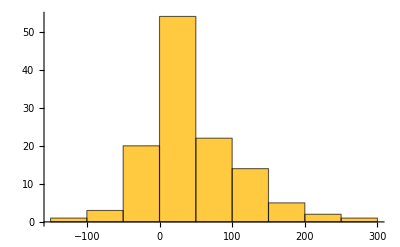

```mathematica
Histogram[#[[1]]-#[[2]]&/@(getpl/@#&/@srfblk)]
```

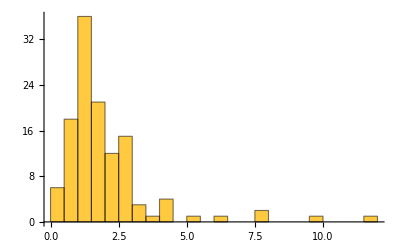

```mathematica
Histogram[#[[1]]/#[[2]]&/@(getpl/@#&/@srfblk),PlotRange->All]
```

#### Surface vs bulk second seg’s

```mathematica
data6=Cases[ends2,(v_/;MemberQ[VertexList[skeleton],v]):>getpl[v]];
data7=Cases[ends2,(v_/;Not@MemberQ[VertexList[skeleton],v]):>getpl[v]];
data8=Cases[ends2,(v_/;AnyTrue[VertexOutComponent[tg,v,{1}],MemberQ[blktips,#]&]&& 
AnyTrue[VertexOutComponent[tg,v,{1}],MemberQ[srftips,#]&]):>getpl[v]];
```

```mathematica
{Mean[#],StandardDeviation[#]}&/@{data6,data7}
```

```mathematica
Mean/@{data1,data6,data2,data7}
```

```mathematica
SmoothHistogram[{data1,data6}]
```

```mathematica
ArgMax[PDF[SmoothKernelDistribution[#],x],x]&/@{data1,data6,data2,data7}
```

```mathematica
SmoothHistogram[{data2,data7}]
```

```mathematica
SmoothHistogram[#/Mean[#]&/@{data1,data2,data6,data7},PlotLegends->{"Surface tips","Bulk tips","SS ducts","BB ducts","SB ducts"}]
```

```mathematica
Histogram[{data6,data7},Automatic,"PDF",PlotRange->Automatic,ChartLegends->Placed[{"surface branches","bulk branches"},{Left,Top}],
FrameLabel->{"Order 2 branch length (μm)","Probability distribution"},Frame->True,AspectRatio->1,GridLines->Automatic,LabelStyle->{Black,FontSize->20},FrameStyle->Black]
```

```mathematica
dist=EmpiricalDistribution[data6];
xmin=130;xmax=400;
data=Table[{x,SurvivalFunction[dist,x]},{x,xmin,xmax}];
fit=LinearModelFit[{data[[All,1]],Log[data[[All,2]]]}ᵀ,x,x];
Grid[{{
Show[ListPlot[data,ScalingFunctions->"Linear",Joined->True,Filling->Bottom],
Plot[Exp@fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed},PlotRange->All]],
Show[ListLogPlot[data,ScalingFunctions->"Linear",Joined->True,Filling->Bottom],
LogPlot[Exp@fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed}]]}}]
-1/fit'[0]
```

```mathematica
dist=EmpiricalDistribution[data7];
xmin=25;xmax=50;
data=Table[{x,CDF[dist,x]},{x,xmin,xmax}];
fit=LinearModelFit[{data[[All,1]],Log[data[[All,2]]]}ᵀ,x,x];
Show[ListPlot[data,ScalingFunctions->"Log",Joined->True,Filling->Bottom],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Dashed}]]
1/fit'[0]
```

```mathematica
wmin=3;
Graphics3D[{VertexList[skeleton,(v_/;branchorder[v]>=wmin&&getz[v]>0):>{Red,Thickness[0.004],Line[{xyz[[v]],xyz[[getp[v]]]}]}],
VertexList[skeleton,(v_/;branchorder[v]<wmin):>{Black,Thickness[0.004],Line[{xyz[[v]],xyz[[getp[v]]]}]}]
},SphericalRegion->True,Boxed->False]
```

#### Shell analysis

```mathematica
Module[{myhull1=Scale[ccvhl,0.9,x0],myhull2=Scale[ccvhl,0.95,x0]},
{Length[ends]-Count[ends,x_/;RegionMember[myhull1,xyz[[x]]]],Length[ends]-Count[ends,x_/;RegionMember[myhull2,xyz[[x]]]]}]
```

```mathematica
srftips=Module[{myhull=Scale[ccvhl,0.75,x0]},Cases[ends,x_/;Not[RegionMember[myhull,xyz[[x]]]]]];
srftips2=Module[{myhull=Scale[ccvhl,0.95,x0]},Cases[ends2,x_/;Not[RegionMember[myhull,xyz[[x]]]]]];
skeleton=Subgraph[gr,VertexInComponent[tg,srftips]];
```

```mathematica
Graphics3D[Table[Point[xyz[[i]]],{i,srftips}],Boxed->False,SphericalRegion->True,
ImageSize->BoundingRegion[xyz[[#]]&/@srftips,"MinBall"][[2]]]
```

```mathematica
Graphics3D[{Table[Point[xyz[[i]]],{i,ends}],{Opacity[0.2],Scale[ccvhl,0.3,x0]}},SphericalRegion->True,Boxed->False]
```

#### Balls

```mathematica
scaledballs[s_]:=Table[Ball[x0+s(x-x0),30s],{x,xyz}];
```

```mathematica
ds=0.1;
srange=Range[ds,1,ds];
Timing[data=Table[Module[{balls=scaledballs[s]},Count[xyz,x_/;AnyTrue[balls,RegionMember[#,x]&]]],{s,srange}];]
```

```mathematica
balls=scaledballs[1];
reggie=RegionUnion[balls];
boundball=BoundingRegion[reggie,"MinBall"];
Timing[NIntegrate[Boole[AnyTrue[balls,RegionMember[#,{x,y,z}]&]],{x,y,z}∈boundball,Method->"MonteCarlo"]]
```

```mathematica
Graphics3D[Table[Ball[x,30],{x,xyz}],Boxed->False,SphericalRegion->True]
```

```mathematica
ListPlot[{srange,1/Last[data](Around[#,Sqrt[#]]&/@(data-Join[{0},data[[;;-2]]]))/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,Frame->True,AspectRatio->1,PlotMarkers->{"■"},Joined->True,
GridLines->Automatic,FrameLabel->{"Scaled radial distance (a.u.)","Density (a.u.)"},LabelStyle->{Black,FontSize->20}]
```

#### Concave hull (no modifications)

```mathematica
ds=0.1;
srange=Range[ds,1.2,ds];
x0=RegionCentroid[ccvhl];
data=Table[Module[{scldhl=Scale[ccvhl,s,x0]},Count[ends,i_/;RegionMember[scldhl,xyz[[i]]]]],{s,srange}]
fit=LinearModelFit[data[[;;]],x,x];
```

{1,8,27,61,117,207,314,441,542,1019,1005,1010}

```mathematica
ListPlot[(data[[2;;,1]]data[[2;;,2]]-data[[;;-2,1]]data[[;;-2,2]])/(data[[2;;,1]]-data[[;;-2,1]])]
```

```mathematica
Show[ListPlot[{srange-ds/2,1/Length[ends](Around[#,Sqrt[#]]&/@(data-Join[{0},data[[;;-2]]]))/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,Joined->True,PlotRange->{{0,1},{0,Automatic}},PlotMarkers->{"■"},GridLines->Automatic,
AspectRatio->1,Filling->None,Frame->True,FrameLabel->{"Scaled radial distance","Tip density (normalized)"},LabelStyle->{Black,Large}],Plot[1,{x,0,1},PlotStyle->Dashed]]
```

#### Concave hull (adding random radial distance)

```mathematica
xm=RegionCentroid[ccvhl];
newpoints=(#+RandomVariate[NormalDistribution[30,10]](#-xm)/Norm[#-xm])&/@xyz;
newhl=ConcaveHullMesh[newpoints];
x0=RegionCentroid[newhl];
```

```mathematica
ds=0.1;
srange=Range[ds,1.2,ds];
data2=Table[Module[{scldhl=Scale[newhl,s,x0]},Count[ends,i_/;RegionMember[scldhl,xyz[[i]]]]],{s,srange}]
```

{2,11,43,104,188,327,467,651,937,1008,1012,1016}

```mathematica
data3549={0,6,22,47,92,138,204,294,430,463,462,464};
```

```mathematica
data3685={2,10,40,100,184,311,452,611,922,999,1003,1003};
```

```mathematica
data3138={3,28,81,184,343,563,892,1274,1801,1951,1952,1955};
```

```mathematica
data3822={9,75,246,590,1092,1869,2951,4297,5951,6727,6730,6728};
```

```mathematica
ListPlot[Table[{srange-ds/2,1/Last[x](Around[#,Sqrt[#]]&/@(x-Join[{0},x[[;;-2]]]))/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,{x,{data3549,data3685,data3138,data3822}}],graphsettings,PlotRange->{{0,1.2},{0,3.5}},PlotMarkers->{"■",6},Joined->True,PlotLegends->Placed[{"PCW8.3","PCW8.7","PCW9.7","PCW10.2"},Right],ImageSize->120,
FrameLabel->{"Scaled radial distance, s","Tip density, ρ"}]
```

-Graphics-

```mathematica
ListPlot[Table[{srange-ds/2,1/Last[x](Around[#,Sqrt[#]]&/@(x-Join[{0},x[[;;-2]]]))/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,{x,{data,data2}}],graphsettings,PlotRange->{{0,1.2},{0,3.5}},PlotMarkers->{"■",6},Joined->False,PlotLegends->Placed[{"No noise","Noise"},{Right,Top}],ImageSize->120,
FrameLabel->{"Scaled radial distance, s","Tip density, ρ"}]
```

-Graphics-

```mathematica
ListPlot[Table[{srange-ds/2,1/Last[x](x-Join[{0},x[[;;-2]]])/(srange^3-Join[{0},srange[[;;-2]]]^3)}ᵀ,{x,{data3549,data3685,data3138,data3822}}],graphsettings,PlotRange->{{0,1.2},{0,3.5}},PlotMarkers->{"■",6},Joined->True,PlotLegends->Placed[{"PCW8.3","PCW8.7","PCW9.7","PCW10.2"},Right],ImageSize->120,
FrameLabel->{"Scaled radial distance, s","Tip density, ρ"}]
```

-Graphics-

```mathematica
Show[Graphics3D[{{Opacity[0.2],Scale[newhl,0.4,x0]},Table[Point[xyz[[i]]],{i,ends}](*,Table[{Red,Point[x]},{x,newpoints}]*)},SphericalRegion->True,Boxed->False]]
```

```mathematica
ds=0.01;
srange=Range[ds,1,ds];
Timing[data=Table[Module[{scldhl=Scale[ccvhl,s,rx0]},Count[ends,i_/;RegionMember[scldhl,xyz[[i]]]]],{s,srange}];]
```

```mathematica
Show[ListPlot[{srange,data/Last[data]}ᵀ,Joined->True],Plot[x^3,{x,0,1},PlotStyle->{Red,Dashed}]]
```

```mathematica
data2=Table[Module[{myhull1=If[s==0,Null,Scale[ccvhl,s,x0]],myhull2=Scale[ccvhl,s+ds,x0]},{s+ds/2,Around[Mean[#],se[#]]&[getpl/@Cases[ends,x_/;RegionMember[myhull2,xyz[[x]]]&&Not[RegionMember[myhull1,xyz[[x]]]]]]}],{s,ds,1-ds,ds}];
```

```mathematica
data3=Table[Module[{myhull1=If[s==0,Null,Scale[ccvhl,s,x0]],myhull2=Scale[ccvhl,s+ds,x0]},{s+ds/2,Around[Mean[#],se[#]]&[getpl/@Cases[ends2,x_/;RegionMember[myhull2,xyz[[x]]]&&Not[RegionMember[myhull1,xyz[[x]]]]]]}],{s,ds,1-ds,ds}];
```

```mathematica
ListPlot[{(*Table[{d[[1]],0.5 d[[2]]^(-1/3)},{d,data}],*)data2,data3},Joined->True,PlotMarkers->{"■"},PlotLegends->{(*"Interparticle separation",*)"Tip lengths","Second segment lengths"}]
```

#### Inner vs outer

```mathematica
core=Scale[ccvhl,0.75,x0];
```

```mathematica
set=ends;fun=getpl;
inner=Cases[set,(v_/;RegionMember[core,xyz[[v]]]):>fun[v]];
outer=Cases[set,(v_/;Not@RegionMember[core,xyz[[v]]]):>fun[v]];
```

```mathematica
Length/@{inner,outer}
```

```mathematica
voxel(({ Volume[core]/Length[inner],(Volume[ccvhl]-Volume[core])/Length[outer]})^(1/3))
```

Balance branch rate + elongation rate heterogeneities

```mathematica
Histogram[{inner,outer},Automatic,"PDF"]
```

```mathematica
{Mean[inner],Mean[outer],Mean[outer]-Mean[inner],Mean[outer]/Mean[inner]}//N
```

```mathematica
dist=EstimatedDistribution[outer,GammaDistribution[3,b]];
```

```mathematica
Show[Histogram[outer,Automatic,"PDF",ScalingFunctions->"Log"],LogPlot[PDF[dist,x],{x,10,500}]]
```

```mathematica
dist
```

### Expansion

```mathematica
tdl={3.14 10^03, 6.33 10^03, 1.71 10^04, 6.75 10^03, 2.40 10^04 ,5.47 10^04 ,9.98 10^04 ,1.11 10^05, 1.36 10^05 ,2.77 10^05 ,2.45 10^05, 2.03 10^05 ,3.09 10^05 ,3.24 10^05 ,4.37 10^05, 1.16 10^06};
mz={3.36, 3.83, 5.87, 4.29, 6.2 ,7.54, 8.91, 9.03, 9.69, 10.4 ,10.05, 10.2, 12.23 ,11.08 ,12.25 ,12.94};
ltr={506,953,1217,830,1450,1880,1891,1928,2178,2336,2241,2250,2277,2430,2745,3409};
tlen={104.8 ,157.6 ,172.5, 159.4 ,228 ,174.6 ,129.9 ,143.8 ,113 ,110.9 ,110.9, 125.2, 90.7 ,100.7 ,92.1 ,62.6};
tlen2={130.7, 199 ,198.8, 163.1, 194.4, 173.3 ,126.5 ,151.4 ,132, 109.7 ,104.3, 116.5, 95.8 ,110.4, 101.1 ,78.3};
```

```mathematica
Manipulate[Show[ListPlot[{mz,ltr}//Transpose],Plot[{A ⅇ^(λ z)(1-x^z)/(1-x),fit[z]},{z,First[mz],Last[mz]},PlotStyle->Dashed]],{A,100,500},{x,0.7,0.9},{λ,0,0.2}]
```

```mathematica
fit=LinearModelFit[{mz,ltr}//Transpose,x,x]
```

L_0(N)=(235N-120)(1-x)/(1-x^N)
TDL=(235N-120)(1-x)/(1-x^N)((2x)^N-1)/(2x-1)

```mathematica
Manipulate[Show[ListLogPlot[{mz,tdl}//Transpose],LogPlot[(235z-120)((1-x)/(1-x^z))((2x)^z-1)/(2x-1),{z,First[mz],Last[mz]},PlotStyle->Dashed]],{x,0.7,0.9}]
```

```mathematica
Solve[{x/(x y-1)==1,}]
```

```mathematica
Manipulate[Show[ListPlot[{mz,tlen}//Transpose,PlotRange->{{0,15},{0,250}}],Plot[(A(z-3))((1-x)/(1-x^z))x^(z-1)/.{x->0.73},{z,1,15},PlotStyle->Dashed]],{A,200,2000}]
```

```mathematica
Plot[2(235z-120)((1-x)/(1-x^z))/.{x->0.794},{z,1,15}]
```

### All cumulants

```mathematica
Table[Cumulant[getpl/@ends,k]/Mean[getpl/@ends]^k,{k,4}]
```

```mathematica
#[getpl/@ends]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
#[getpl/@ends2]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
#[getpw/@ends]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
#[getpw/@ends2]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
N[#[getz/@ends]]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
N[#[ltoroot/@ends]]&/@{Mean,cov,Skewness,Kurtosis[#]-3&}
```

```mathematica
SmoothHistogram[Table[1.33^-n getpl/@VertexList[gr,v_/;branchorder[v]==n],{n,2,branchorder[1]-2}]]
```

```mathematica
LinearModelFit[Table[{n,Log@Mean[getpl/@VertexList[gr,v_/;branchorder[v]==n]]},{n,2,branchorder[1]-1}],n,n]
```

```mathematica
Histogram[getpl/@ends2]
```

```mathematica
SmoothHistogram[{VertexList[gr,(v_/;branchorder[v]==2):>getpl[v]],VertexList[gr,(v_/;branchorder[v]>=2):>1.33^(2-branchorder[v])getpl[v]]},ScalingFunctions->"Log"]
```

### LTR LN fit

```mathematica
mydata=ltoroot/@ends;
{mydist=EstimatedDistribution[mydata,LogNormalDistribution[a,b]],Skewness[mydata]//N}
Show[Histogram[mydata,Automatic,"PDF",PlotRange->All],Plot[PDF[mydist,x],{x,0.9Min[mydata],1.1Max[mydata]},PlotRange->All,PlotStyle->Dashed]]
```

```mathematica
skelgraphics[gr]
```

```mathematica
mydata=getpl/@ends;
{mydist=EstimatedDistribution[mydata,GammaDistribution[a,b]],Skewness[mydata]//N}
Show[Histogram[mydata,Automatic,"PDF",PlotRange->All],Plot[PDF[mydist,x],{x,0.9Min[mydata],1.1Max[mydata]},PlotRange->All,PlotStyle->Dashed]]
```

### Visual

```mathematica
Graph[gr,VertexCoordinates->VertexList[gr,v_:>xyz[[v]]],EdgeStyle->Flatten[VertexList[gr,(v_/;Not[v==1]):>{getp[v]<->v->Hue[branchorder[getp[v]]/branchorder[1]],v<->getp[v]->Hue[branchorder[getp[v]]/branchorder[1]]}]]]
```

```mathematica
Graph[gr,VertexCoordinates->VertexList[gr,v_:>xyz[[v]]],EdgeStyle->Flatten[VertexList[gr,(v_/;Not[v==1]):>{getp[v]<->v->Hue[lssage[getp[v]]/lssage[1]],v<->getp[v]->Hue[lssage[getp[v]]/lssage[1]]}]]]
```

```mathematica
nodes=VertexList[gr,v_/;branchorder[v]<branchorder[getp[v]]];
```

```mathematica
colordata=ColorData[{"CherryTones",{1,branchorder[1]}}];
Legended[Graphics3D[Table[{colordata[branchorder[v]],Line[{xyz[[v]],xyz[[getp[v]]]}]},{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Background->Black,Boxed->False],BarLegend[{colordata,colordata[[3]]},LegendLabel->"B.O."]]
```

```mathematica
colordata=ColorData[{"CherryTones",{90,0}}];
Legended[Graphics3D[Table[{colordata[If[getz[v]<=1,0,palignd[v]]],Line[{xyz[[v]],xyz[[getp[v]]]}]},{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Background->Black,Boxed->False],BarLegend[{colordata,Reverse@colordata[[3]]},LegendLabel->"Alignment (°)"]]
```

```mathematica
colordata=ColorData[{"CherryTones",{Quantile[w,0.05],Quantile[w,0.95]}}];
Legended[Graphics3D[Table[{colordata[If[getz[v]<1,0,getpw[v]]],Line[{xyz[[v]],xyz[[getp[v]]]}]},{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Background->Black,Boxed->False],BarLegend[{colordata,colordata[[3]]},LegendLabel->"z"]]
```

```mathematica
colordata=ColorData[{"CherryTones",{Quantile[l,0.05],Quantile[l,0.95]}}];
Legended[Graphics3D[Table[{colordata[If[getz[v]<1,0,getpl[v]]],Line[{xyz[[v]],xyz[[getp[v]]]}]},{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Background->Black,Boxed->False],BarLegend[{colordata,colordata[[3]]},LegendLabel->"z"]]
```

```mathematica
colorf=zintage;
colordata=ColorData[{"TemperatureMap",{Min[colorf/@VertexList[gr]],Max[colorf/@VertexList[gr]]}}];
max=Max[#/@VertexList[gr,v_/;getz[v]>1]]&/@{palignd,getpl,getpw};
Legended[Graphics3D[VertexList[gr,(v_/;getz[v]>1):>{colordata[colorf[v]],PointSize->Small,Point[{palignd[v]/max[[1]],getpl[v]/max[[2]],getpw[v]/max[[3]]}]}],PlotRange->All,SphericalRegion->True,Axes->True,AxesLabel->{"Alignment","Length","Width"},Background->Black,AspectRatio->1],BarLegend[{colordata,colordata[[3]]}]]
```

```mathematica
colordata=ColorData[{"TemperatureMap",{0,0.4}}];
max=Max[#/@VertexList[gr,v_/;getz[v]>1]]&/@{palignd,getpl,getpw};
Legended[Graphics3D[VertexList[gr,(v_/;getz[v]>1&&VertexDegree[gr,v]>1):>{If[MemberQ[VertexList[Highways],v],Red,Darker[LightBlue]],PointSize->Small,Point[{palignd[v]/max[[1]],getpl[v]/max[[2]],getpw[v]/max[[3]]}]}],PlotRange->All,SphericalRegion->True,Axes->True,AxesLabel->{"Alignment","Length","Width"},Background->Black,AspectRatio->1],BarLegend[{colordata,colordata[[3]]}]]
```

```mathematica
f=getz;
sample=ends;
colordata=ColorData[{"TemperatureMap",{Quantile[f/@sample,0.05],Quantile[f/@sample,0.95]}}];
Legended[Graphics3D[Table[{colordata[f[v]],PointSize->Medium,Point[xyz[[v]]]},{v,sample}],PlotRange->All,SphericalRegion->True,Boxed->False],BarLegend[{colordata,colordata[[3]]},LegendLabel->"Generation"]]
```

```mathematica
Legended[skelgraphics[skeleton],BarLegend[{colordata,colordata[[3]]}]]
```

### Basic analysis

```mathematica
{Mean[getpl/@ends],Mean[getpw/@ends],Mean[getpl/@ends2],Mean[getpw/@ends2]}
```

```mathematica
Grid[Map[Histogram,{getpl/@#&/@{ends,ends2},getpw/@#&/@{ends,ends2}},{2}]]
```

```mathematica
b12=Tally[getz/@ends];
```

```mathematica
b3=Tally[getz/@ends];
```

```mathematica
b4=Tally[getz/@ends];
```

```mathematica
b5=Tally[getz/@ends];
```

```mathematica
ListLogPlot[Table[VertexCount[gr,v_/;branchorder[v]==z],{z,branchorder[1]}],Filling->Bottom]
```

```mathematica
ListPlot[{Table[{z,Gini[Length[VertexOutComponent[tg,#]]&/@VertexOutComponent[tg,1,{z}]]},{z,VertexEccentricity[tg,1]}],
Table[Length[VertexOutComponent[tg,1,{z}]]/2^(z),{z,VertexEccentricity[tg,1]}]},Joined->True,PlotMarkers->Automatic]
```

```mathematica
Graph[#,VertexCoordinates->VertexList[#,v_:>xyz[[v]]]]&[HighlightGraph[gr,Subgraph[gr,
VertexList[gr,(v_/;0.667getpw[v]>getpl[v]&&VertexDegree[gr,v]>=3):>Join[AdjacencyList[gr,v],AdjacencyList[gr,getp[v]]]]
]]]
```

```mathematica
VertexList[gr,(v_/;VertexDegree[gr,v]>3):>Join[{v},AdjacencyList[gr,v]]]
```

```mathematica
VertexList[gr,(v_/;0.667getpw[v]>getpl[v]&&VertexDegree[gr,v]>=3):>Join[AdjacencyList[gr,v],AdjacencyList[gr,getp[v]]]]
```

```mathematica
Outer[DensityHistogram[VertexList[gr,(v_/;Not[v==1]):>{#1[v],#2[v]}]]&,{getz,lssage,ltoroot,getpl,getpw},{getz,lssage,ltoroot,getpl,getpw}]//MatrixForm
```

```mathematica
Outer[N[SpearmanRho@@Transpose[VertexList[gr,v_:>{#1[v],#2[v]}]]]&,{getz,lssage,ltoroot,getpl,getpw},{getz,lssage,ltoroot,getpl,getpw}]//MatrixForm
```

### Typical typs

```mathematica
μl=Mean[getpl/@ends];μw=Mean[getpw/@ends];
Cases[ends,(v_/;getpl[v]==Around[μl,2]&&getpw[v]==Around[μw,0.5]):>{v,getp[v]}]
```

### Random graph models

#### Regular unbalanced trees

Horsfield tree (constant delta)

```mathematica
ClearAll[htree];
htree[n_]:=htree[n]=Tree[{htree[n-1],htree[n-2]}];
htree[1]=Tree[{Null,Null}];
htree[0]=Null;
root={Null,{}};
```

```mathematica
mygraph=TreeGraph[htree[15]];
ListPlot[Tally@VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>GraphDistance[mygraph,root,v]],Joined->True,Filling->Bottom]
```

```mathematica
streestds=Table[Module[{g=TreeGraph[stree[n]],list},list=VertexList[g,(v_/;VertexDegree[g,v]==1):>GraphDistance[g,root,v]];{Mean[list],StandardDeviation[list]}],{n,8}];
htreestds=Table[Module[{g=TreeGraph[htree[n]],list},list=VertexList[g,(v_/;VertexDegree[g,v]==1):>GraphDistance[g,root,v]];{Mean[list],StandardDeviation[list]}],{n,20}];
```

```mathematica
squarey[list_]:=Transpose[{Transpose[list][[1]],Transpose[list][[2]]^2}];
```

```mathematica
LinearModelFit[{means,stds}ᵀ,x,x,IncludeConstantBasis->False]
```

```mathematica
Show[ListPlot[{{means,stds}ᵀ,streestds,htreestds,h2treestds},Joined->{False,True,True,True}],Plot[{0.1611x,0.35 √x},{x,0,20},PlotStyle->Dashed]]
```

Strahler tree (constant Strahler branching number)

```mathematica
ClearAll[stree];
stree[n_]:=stree[n]=Tree[{Tree[{stree[n-1],stree[n-1]}],stree[n-1]}];
stree[0]=Null;
root={Null,{}};
```

```mathematica
mygraph=TreeGraph[stree[7]];
ListPlot[Tally@VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>GraphDistance[mygraph,root,v]],Joined->True,Filling->Bottom]
```

Horsfield tree 2 (slow sister half as slow)

```mathematica
ClearAll[h2tree];
h2tree[n_]:=h2tree[n]=Tree[{h2tree[n-1],h2tree[Floor[7/8(n-1)]]}];
h2tree[1]=Tree[{Null,Null}];
h2tree[0]=Null; 
root={Null,{}};
```

```mathematica
mygraph=TreeGraph[h2tree[20]];
Show[ListPlot[{Sort@Tally@VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>GraphDistance[mygraph,root,v]],Sort@Tally@VertexList[gr,(v_/;VertexDegree[gr,v]==1):>getz[v]]},Joined->True,Filling->Bottom],
Plot[VertexCount[mygraph]/2PDF[dist,x],{x,0,20},PlotStyle->Dashed]]
```

```mathematica
dist=EstimatedDistribution[VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>GraphDistance[mygraph,root,v]],LogNormalDistribution[a,b]]
```

```mathematica
h2treestds=Table[Module[{g=TreeGraph[h2tree[n]],list},list=VertexList[g,(v_/;VertexDegree[g,v]==1):>GraphDistance[g,root,v]];{Mean[list],StandardDeviation[list]}],{n,25}];
```

#### Reproducing data

```mathematica
(*rgetz[v_]:=GraphDistance[g,root,v];*)
rgetz[v_]:=v[[1,4]];
rgetp[g_,v_]:=First[VertexInComponent[g,v,{1}]];
root={{0,0,0,0,0},{}};
```

mt = 1; st = 0.3;(*Mean & STD of (surface) branch time distribution*)
mtblk = 2.0; stblk = mtblk st;(*Scaling of bulk branch time distribution (both mean and STD)*)
md = 0.8; sd = 0.3;(*Mean & STD of delay time distribution*) 
mdblk = 0.4; sdblk = 0.2;

(*timedist=TruncatedDistribution[{0,∞},NormalDistribution[mt,st]];
dlydist=TruncatedDistribution[{0,∞},NormalDistribution[md,sd]];
timedistb=TruncatedDistribution[{0,∞},NormalDistribution[mtblk,stblk]];
dlydistb=TruncatedDistribution[{0,∞},NormalDistribution[mtblk,sdblk]];*)

(*timedist=EmpiricalDistribution[data6/Mean[data6]];
dlydist=EmpiricalDistribution[tipdiffs/Mean[data6]];
timedistb=EmpiricalDistribution[data7/(Mean[data7]/2)];
dlydistb=EmpiricalDistribution[tipdiffb/(Mean[data7]/2)];*)
σs=0.4;(*Surface time StD*)
σb=0.3;(*Bulk time StD*)
(*timedist=TruncatedDistribution[{0,∞},LaplaceDistribution[1,σs/√2]];*)
(*timedistb=TruncatedDistribution[{0,∞},LaplaceDistribution[τ,τ σb/√2]];*)

```mathematica
kp=KroneckerProduct;rv=RandomVariate;
rss=0.55;(*Probability of S->S+S branching event*)
zmin=5;(*Generation until which all tips are surface*)

τ=1.4;(*Bulk branch time*)
Δs=0.01;(*Surface delay*)
Δb=0.01;(*Bulk delay*)

γs=5.5;(*Shape parameter for surface branch time distribution*)
γb=5.5;(*Shape parameter for bulk branch time distribuion*)
timedist=LogLogisticDistribution[γs,Sinc[π/γs]];
dlydist=ExponentialDistribution[Δs^-1];
timedistb=LogLogisticDistribution[γb,τ Sinc[π/γb]];
dlydistb=ExponentialDistribution[(τ Δb)^-1];

line={1.0,1.0,1.0};
```

r, z_min, σ_s, σ_b, Δ_s, Δ_b, τ, l_0, v_b, λ_e

rtg := TreeGraph[NestTree[If[#[[1]] < t, rv[timedist, 2] + {{#[[1]], 0}, {#[[1]] + rv[dlydist], 0}}, None] &, {0, 0}, 25]];

Data in each node : { total time , length , surface/bulk (0/1) , generation , line, order (Strahler)}

```mathematica
rtg[t_]:=TreeGraph[
NestTree[
If[#[[4]]==0,
kp[line rv[timedist,3],{1,1,0,0,0}]+Array[{0,0,0,1,#}&,3],(*Starting with 3 branches*)
If[#[[1]]<t,
If[#[[3]]==0,
If[#[[4]]<zmin,(*Surface generation threshold*)
kp[line[[#[[5]]]]rv[timedist,2],{1,1,0,0,0}]+{{#[[1]],0,0,#[[4]]+1,#[[5]]},{#[[1]]+line[[#[[5]]]]rv[dlydist],0,0,#[[4]]+1,#[[5]]}},(*SS*)
If[RandomReal[]<rss,
kp[line[[#[[5]]]]rv[timedist,2],{1,1,0,0,0}]+{{#[[1]],0,0,#[[4]]+1,#[[5]]},{#[[1]]+line[[#[[5]]]]rv[dlydist],0,0,#[[4]]+1,#[[5]]}},(*SS*)
kp[{line[[#[[5]]]]rv[timedist],(*line[[#[[5]]]]*)rv[timedistb]},{1,1,0,0,0}]+{{#[[1]],0,0,#[[4]]+1,#[[5]]},{#[[1]]+line[[#[[5]]]]rv[dlydist],0,1,#[[4]]+1,#[[5]]}}](*SB*)
],
kp[(*line[[#[[5]]]]*)rv[timedistb,2],{1,1,0,0,0}]+{{#[[1]],0,1,#[[4]]+1,#[[5]]},{#[[1]]+(*line[[#[[5]]]]*)rv[dlydistb],0,1,#[[4]]+1,#[[5]]}}(*BB*)
]
,None]]&,
{0,0,0,0,0},30]
];
```

#### Collective statistics

```mathematica
ages={5.7,6.1,6.1,6.1,6.3,6.6,6.6,6.6,7,7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};means={1.67,3.36,5.44,2.86,3.33,3.85,4.82,3.83,4.29,5.87,6.2,7.54,9.03,8.91,8.55,8.89,9.69,9.81,10.2,10.05,10.4,12.23,10.82,11.08,10.7,13.34,12.25,13.73,13.41,14.43,14.81,16.18,17.37};
stds={0.577,0.63,1.685,0.38,0.707,0.69,1.1,0.86,0.85,0.96,1.1,1.11,1.43,1.59,1.55,1.354,1.57,1.62,1.47,1.48,1.72,2.14,1.76,1.49,1.45,2.31,1.81,2.77,1.67,2.3,2.28,2.67,2.51};
srffracs={1,0.857142857142857,0.777777777777778,1,1,0.857142857142857,1,0.96,1,1,0.945454545454545,0.744827586206897,0.598853868194842,0.636111111111111,0.65843621399177,0.631578947368421,0.554,0.544954128440367,0.45,0.456329735034347,0.452797202797203,0.403973509933775,0.40796812749004,0.382751247327156,0.427854454203262,0.398069963811821,0.371954251616111,0.325502542988617,0.25353982300885,0.205066483264558,0.191721132897603,0.1573215389737,0.151683202634201};
nbranches={4,12,16,25,33,25,42,42,39,90,108,288,691,716,481,716,991,1082,1513,2027,2273,3001,2493,2792,3171,3287,3992,8161,13434,17172,24477,41172,45218};
rbs={2.686,2.375,2.616,2.764,2.678,2.571,2.513,2.588,2.523,2.662,2.717,2.652,2.525,2.538,2.446,2.521,2.572,2.634,2.526,2.629,2.679,2.701,2.696};
```

```mathematica
Show[ListPlot[MapThread[,{ages[[11;;]],rbs,}],Frame->True,PlotMarkers->{"OpenMarkers",3},AspectRatio->1,GridLines->Automatic,PlotRange->{{6,14},{2.0,3.0}},ImageSize->120,FrameLabel->{"Age (PCW)","Branching ratio, R_b"}],Plot[2.59,{x,6,14},PlotStyle->Thickness[0.008]]]
```

```mathematica
Timing[test=Table[
Module[{gx=rtg[tmax],tipz,rbo},tipz=VertexList[gx,v_/;VertexDegree[gx,v]==1];
rbo[v_]:=rbo[v]=If[VertexDegree[gx,v]==1,1,Max[#]+If[SameQ@@#,1,0]&[rbo/@VertexOutComponent[gx,v,{1}]]];
{tmax,Mean[rgetz/@tipz],StandardDeviation[rgetz/@tipz],Count[tipz,v_/;v[[1,3]]==0]/Length[tipz],VertexCount[gx],
Exp[-LinearModelFit[Table[{z,Log@VertexCount[gx,v_/;rbo[v]==z&&rbo[First@VertexInComponent[gx,v,{1}]]>z]},{z,rbo[root]-1}],x,x]'[0]]}]
,{tmax,2,14,1},{n,30}];]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{751.047,Null}

```mathematica
Export["collective_sim_data.csv",test];
```

```mathematica
test=ToExpression@Import["collective_sim_data.csv"];
```

```mathematica
fit1=LinearModelFit[{ages,Log@nbranches}ᵀ,x,x];
fit2=LinearModelFit[{Flatten@test[[All,All,1]],Flatten@Log@test[[All,All,5]]}ᵀ,x,x];
simage[x_]:=First[a/.Solve[fit1[a]==fit2[x],a]];
data={    
{{ages,means}ᵀ,Table[{simage@i[[1,1]],Around[Mean[#],1.96StandardDeviation[#]]&[i[[All,2]]]},{i,test}]},
{{ages,stds}ᵀ,Table[{simage@i[[1,1]],Around[Mean[#],1.96StandardDeviation[#]]&[i[[All,3]]]},{i,test}]},
{{ages,srffracs}ᵀ,Table[{simage@i[[1,1]],Around[Mean[#],1.96StandardDeviation[#]+10^-9]&[i[[All,4]]]},{i,test}]},
{{ages,nbranches}ᵀ,Table[{simage@i[[1,1]],Exp@Around[Mean[#],1.96StandardDeviation[#]]&[Log@i[[All,5]]]},{i,test}]},
{{ages[[11;;]],rbs}ᵀ,Table[{simage@i[[1,1]],Around[Mean[#],1.96StandardDeviation[#]]&[i[[All,6]]]},{i,test}]}};
axes={{"Age (PCW)","Gen. mean"},{"Age (PCW)","Tip generation SD"},{"Age (PCW)","Surface tip fraction"},{"Age (PCW)","Branch count"},{"Age (PCW)","Branching ratio, R_b"}};
scale={"Linear","Linear","Linear","Log10","Linear"};
ranges={{{4,14},{0,20}},{{4,14},{0,3}},{{4,14},{0,1.2}},{{4,14},{1,10^5}},{{6,14},{2.0,3.0}}};
Grid[{Table[
Show[ListPlot[data[[i,1]],PlotMarkers->{"OpenMarkers",3},Frame->True,GridLines->Automatic,AspectRatio->1,LabelStyle->{Black,FontSize->6.4} ,FrameLabel->axes[[i]],ScalingFunctions->scale[[i]],PlotRange->ranges[[i]],ImageSize->120,FrameStyle->Black,PlotLegends->Placed[{"Experiment"},{Right,Bottom}]],
ListLinePlot[data[[i,2]],IntervalMarkers->"Bands",graphsettings,PlotLegends->Placed[{"Simulation"},{Right,Bottom}],PlotStyle->ColorData[97,2],ScalingFunctions->scale[[i]]]],
{i,5}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ages={7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
srfcovs={0.467005,0.454716,0.410392,0.41745,0.592688,0.547735,0.390164,0.380763,0.335415,0.402439,0.391389,0.388529,0.306865,0.394043,0.365209,0.400909,0.353914,0.314021,0.433518,0.355396,0.394698,0.431517};
blkcovs={0.328382,0.310315,0.21791,0.383993,0.26017,0.257711,0.263822,0.275449,0.21768,0.326087,0.256055,0.256216,0.267562,0.274448,0.236967,0.298035,0.257862,0.269177,0.306709,0.273717,0.312287,0.324503};
```

```mathematica
ages={7.3,6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
srftipscov={0.78,0.74,0.57,0.61,0.57,0.54,0.65,0.55,0.58,0.56,0.52,0.53,0.6,0.57,0.59,0.54,0.54,0.55,0.54,0.5,0.56,0.53,0.55,0.59};
blktipscov={0.83,0.37,0.46,0.45,0.52,0.46,0.61,0.47,0.46,0.47,0.45,0.47,0.48,0.51,0.52,0.48,0.49,0.5,0.49,0.49,0.47,0.47,0.48,0.45};
```

```mathematica
Show[ListPlot[{Transpose[{ages,srftipscov}][[3;;]],Transpose[{ages,blktipscov}][[3;;]]},graphsettings,PlotMarkers->{"OpenMarkers",3},ImageSize->120,PlotStyle->{Red,Blue},FrameLabel->{"Age (PCW)","Tip length CV"},PlotRange->{{6,14},{0,1.0}},PlotLegends->Placed[{"Surface","Bulk"},{Right,Top}]],Plot[Evaluate@{Around[Mean[#],1.96 se[#]]&[srftipscov[[3;;]]],Around[Mean[#],1.96 se[#]]&[blktipscov[[3;;]]]},{x,7.6,12},PlotStyle->{Red,Blue}]]
```

-Graphics-

```mathematica
Around[Mean[#],1.96 se[#]]&[srftipscov[[3;;]]]
```

0.5610.014

```mathematica
Around[Mean[#],1.96 se[#]]&[blktipscov[[3;;]]]
```

0.4840.015

```mathematica
{Mean[#],se[#]}&[blkcovs]
```

{0.280684,0.00844952}

#### Single sample sim

```mathematica
g=rtg[12.5];
```

```mathematica
UndirectedGraph[g,GraphLayout->{"RadialEmbedding","RootVertex"->root},VertexSize->0.001,EdgeStyle->ColorData[97,2]]
```

```mathematica
Graph[gr,GraphLayout->{"RadialEmbedding","RootVertex"->1},VertexSize->0.001]
```

```mathematica
VertexCount[gr]
```

2494

```mathematica
t=12.5;
test=Table[VertexCount[rtg[t]],{i,10}];
Exp@Mean[Log@test]//N
```

2550.07

```mathematica
Exp[Log[2494] 0.95]
```

1686.75

```mathematica
Exp[Log[2494] 1.05]
```

3687.58

```mathematica
t=9.5;
Clear[g];
g=Table[rtg[t],{i,100}];
Exp[Mean[Log[VertexCount/@g]]]//N
```

2644.56

```mathematica
ClearAll[rbo];
rbo[v_]:=rbo[v]=If[VertexDegree[g,v]==1,1,Max[#]+If[SameQ@@#,1,0]&[rbo/@VertexOutComponent[g,v,{1}]]];
rbo[root];
ClearAll[rboh];
rboh[v_]:=rboh[v]=If[VertexDegree[g,v]==1,1,Max[rboh/@VertexOutComponent[g,v,{1}]+1]];
rboh[root];
rends=VertexList[g,v_/;VertexDegree[g,v]==1];
endgens=VertexList[g,(v_/;VertexDegree[g,v]==1):>rgetz[v]];
Exp[-LinearModelFit[Table[{z,Log@VertexCount[g,v_/;rbo[v]==z&&rbo[rgetp[v]]>z]},{z,rbo[root]-1}],x,x]'[0]]
```

$Aborted

```mathematica
ClearAll[rbo];
rbo[i_,v_]:=rbo[i,v]=If[VertexDegree[g[[i]],v]==1,1,Max[#]+If[SameQ@@#,1,0]&[rbo[i,#]&/@VertexOutComponent[g[[i]],v,{1}]]];
Table[rbo[i,root],{i,100}];
ClearAll[rboh];
(*rboh[g_,v_]:=If[VertexDegree[g,v]==1,1,Max[rboh[g,#]&/@VertexOutComponent[g,v,{1}]+1]];*)
rboh[i_,v_]:=rboh[i,v]=VertexEccentricity[g[[i]],v]+1;
```

```mathematica
minz=Min[Table[Min[VertexList[g[[i]],(v_/;VertexDegree[g[[i]],v]==1):>rgetz[v]]],{i,100}]];
maxz=Max[Table[Max[VertexList[g[[i]],(v_/;VertexDegree[g[[i]],v]==1):>rgetz[v]]],{i,100}]];
ListPlot[{
Table[{z,VertexCount[gr,v_/;VertexDegree[gr,v]==1&&getz[v]==z]},{z,6,VertexEccentricity[tg,1]}],
Table[{z,Around[Mean[#],1.96 StandardDeviation[#]]&@Table[VertexCount[gi,v_/;VertexDegree[gi,v]==1&&rgetz[v]==z],{gi,g}]},{z,minz,maxz}]
},Joined->True,PlotMarkers->{"■",8},IntervalMarkers->"Bands",PlotRange->{{0,20},{0,800}},graphsettings,ImageSize->120,FrameLabel->{"Generation, z","Number of tips, mz"},PlotLegends->Placed[{"Experiment","Simulation"},{Right,Top}]]
```

-Graphics-

```mathematica
DumpSave["sim_graphs_1.mx",g];
```

```mathematica
Get["sim_graphs_1.mx"];
```

#### Single sample subtrees

```mathematica
Sort[Tally[Length/@ConnectedComponents[Subgraph[UndirectedGraph[g],VertexList[g,v_/;v[[1,3]]==1]]]]]
```

```mathematica
183/631//N
```

```mathematica
Tally[Cases[ConnectedComponents[Subgraph[UndirectedGraph[g],VertexList[g,v_/;v[[1,3]]==1]]],(x_/;Length[x]==7):>Max[rgetz/@x]-Min[rgetz/@x]]]
```

```mathematica
Sort[Tally[Length/@ConnectedComponents[skeletont]]]
```

```mathematica
153/549//N
```

```mathematica
Tally[Cases[ConnectedComponents[skeletont],(x_/;Length[x]==7):>Max[getz/@x]-Min[getz/@x]]]
```

#### Trimming

Trimming inhibited tips

```mathematica
g=VertexDelete[g,v_/;VertexDegree[g,v]==1&&v[[1,2]]-(v[[1,1]]-t)<0];
deg2vs=VertexList[g,v_/;VertexDegree[g,v]==2&&v=!=root];
Do[
vchild=First[VertexOutComponent[g,v,{1}]];
vpar=First[VertexInComponent[g,v,{1}]];
g=EdgeAdd[VertexDelete[g,{v,vchild}],vpar->{{vchild[[1,1]],vchild[[1,2]]+v[[1,2]],0,v[[1,4]],0},{0}}];
,{v,deg2vs}];
VertexCount[g]
```

#### Topological measures

```mathematica
zmax=VertexEccentricity[gr,1];
rzmax=Max[VertexEccentricity[#,root]&/@g];
```

```mathematica
nzcond[cond_]:=Table[VertexCount[gr,v_/;getz[v]==z&&cond[v]],{z,zmax}];
nzcondr[cond_]:=Table[Table[VertexCount[gi,v_/;rgetz[v]==z&&cond[v]],{gi,g}],{z,rzmax}];
mstd[list_]:=Around[Mean[#],1.96StandardDeviation[#]+10^-9]&/@list;
plotable[list_]:=DeleteCases[MapThread[If[First@#2==0,Null,{#1,#2}]&,{Range[rzmax],mstd[list]}],Null]
```

```mathematica
data={{nzcond[MemberQ[VertexList[skeleton],#]&],plotable@nzcondr[#[[1,3]]==0&]},
{nzcond[Not@MemberQ[VertexList[skeleton],#]&],plotable@nzcondr[#[[1,3]]==1&]},
{nzcond[MemberQ[VertexList[skeleton],#]&]/nzcond[True&],mstd@DeleteCases[MapThread[If[#1==0,0,#1/#2]&,{nzcondr[#[[1,3]]==0&],nzcondr[True&]},2],Null,2]},
{nzcond[MemberQ[VertexList[skeleton],#]&&VertexDegree[gr,#]==1&],plotable@nzcondr[#[[1,3]]==0&&VertexDegree[gi,#]==1&]},
{nzcond[Not@MemberQ[VertexList[skeleton],#]&&VertexDegree[gr,#]==1&],plotable@nzcondr[#[[1,3]]==1&&VertexDegree[gi,#]==1&]}};
axes={"surf. branches","bulk branches","Fraction of srurface branches","surf. tips","bulk tips"};
scale={"Log10","Log10","Linear","Log10","Log10"};
range={{1,10^3},{1,10^3},{0,1.2},{1,10^3},{1,10^3}};
Grid[{Table[ListPlot[data[[i]],ScalingFunctions->scale[[i]],IntervalMarkers->"Bands",Joined->True,PlotMarkers->"■",PlotLegends->Placed[{"Experiment","Simuation"},{Left,Bottom}],PlotRange->{{0,20},range[[i]]},AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"Generation, z",axes[[i]]},FrameStyle->Black,LabelStyle->{Black,FontSize->6.4},ImageSize->120],{i,5}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
{Mean[#],StandardDeviation[#],cov[#]}&/@{endgens,getz/@ends}//N//MatrixForm
```

```mathematica
rwmax=Max[Table[rbo[i,root],{i,100}]];
ListPlot[{
Table[{z,VertexCount[gr,v_/;branchorder[v]==z&&branchorder[getp[v]]>z]},{z,branchorder[1]}],
Table[Around[Mean[#],1.96StandardDeviation[#]]&@Table[VertexCount[g[[i]],v_/;rbo[i,v]==z&&rbo[i,rgetp[g[[i]],v]]>z],{i,100}],{z,rwmax}]
},ScalingFunctions->"Log10",FrameLabel->{"Branch order, w","Number of branches, n_w"},Joined->True,PlotMarkers->{"■"},
PlotLegends->Placed[{"sample","simulation"},{Right,Top}],PlotRange->{{0,10},{1,10^4}},Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->6.4},ImageSize->120,IntervalMarkers->"Bands",GridLines->Automatic,FrameStyle->Black]
```

-Graphics-

```mathematica
{Exp[-LinearModelFit[Table[{z,Log@VertexCount[gr,v_/;branchorder[v]==z&&branchorder[getp[v]]>z]},{z,branchorder[1]-1}],x,x]'[0]],
Exp[-LinearModelFit[Table[{z,Log@VertexCount[g,v_/;rbo[v]==z&&rbo[rgetp[v]]>z]},{z,rbo[root]-1}],x,x]'[0]]}
```

```mathematica
{{Length[endgens], 
VertexCount[g,v_/;AnyTrue[AdjacencyList[g,v],VertexDegree[g,#]==1&]],
1/Length[endgens] VertexCount[g,v_/;AnyTrue[AdjacencyList[g,v],VertexDegree[g,#]==1&]]//N},
{Length[ends],Length[ends2],Length[ends2]/Length[ends]//N}}//MatrixForm
```

(8840 | 5260 | 0.595023
8722 | 4781 | 0.548154)

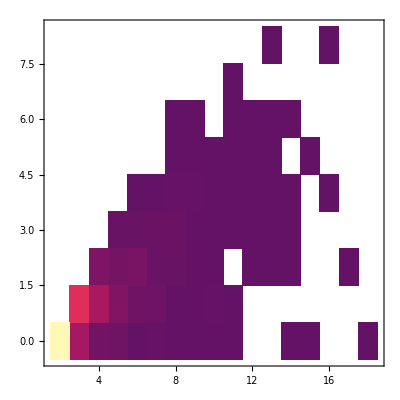
-Graphics- | -Graphics-

```mathematica
Grid[{{
DensityHistogram[VertexList[gr,(v_/;Length[VertexOutComponent[tg,v,{1}]]==2):>{boh[v],Abs[boh[#[[1]]]-boh[#[[2]]]&[VertexOutComponent[tg,v,{1}]]]}]],
DensityHistogram[VertexList[g[[1]],(v_/;Length[VertexOutComponent[g[[1]],v,{1}]]==2):>{rboh[v],Abs[rboh[#[[1]]]-rboh[#[[2]]]&[VertexOutComponent[g[[1]],v,{1}]]]}]]
}}]
```

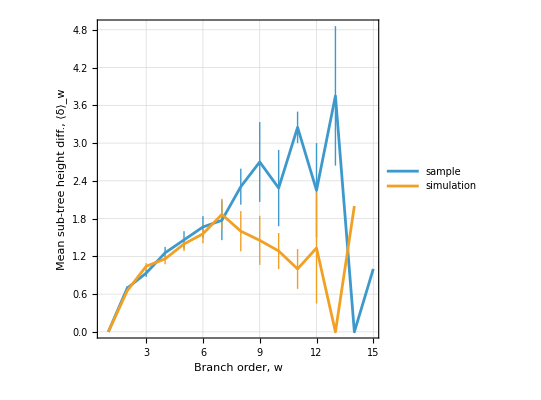

```mathematica
ListPlot[{
Table[{w-1,Around[Mean[#],se[#]]&@VertexList[gr,(v_/;boh[v]==w):>Abs[boh[#[[1]]]-boh[#[[2]]]&[VertexOutComponent[tg,v,{1}]]]]},{w,2,boh[1]}],Table[{w-1,Around[Mean[#],se[#]]&@VertexList[g,(v_/;rboh[v]==w):>Abs[rboh[#[[1]]]-rboh[#[[2]]]&[VertexOutComponent[g,v,{1}]]]]},{w,2,rboh[root]}]},
Joined->True,Frame->True,FrameLabel->{"Branch order, w","Mean sub-tree height diff., ⟨δ⟩_w"},LabelStyle->{Large,Black},AspectRatio->1,GridLines->Automatic,PlotRange->All,PlotLegends->Placed[{"sample","simulation"},{Left,Top}]]
```

```mathematica
ListPlot[{
Table[{w-1,Around[Mean[#],se[#]]&@VertexList[gr,(v_/;boh[v]==w):>Abs[boh[#[[1]]]-boh[#[[2]]]&[VertexOutComponent[tg,v,{1}]]]]},{w,2,boh[1]}],Table[{w-1,Around[Mean[#],1.96StandardDeviation[#]]&@(Mean/@Table[VertexList[g[[i]],(v_/;rboh[i,v]==w):>Abs[rboh[i,#[[1]]]-rboh[i,#[[2]]]&[VertexOutComponent[g[[i]],v,{1}]]]],{i,100}])},{w,2,boh[1]}]},
Joined->True,Frame->True,FrameLabel->{"Branch order (Horsfield), w","Mean sub-tree height diff., ⟨δ_w⟩"},LabelStyle->{FontSize->6.4,Black},PlotRange->{{0,20},{0,8}},ImageSize->115,AspectRatio->1,FrameStyle->Black,GridLines->Automatic,PlotRange->All,PlotLegends->Placed[{"sample","simulation"},{Left,Top}],PlotMarkers->{"■",8},PlotStyle->Thickness[0.01],IntervalMarkers->{"Fences","Bands"}]
```

-Graphics-

#### Single sample length stats

```mathematica
rexp=0.17;(*Expansion per average branch time*)
vblk=0.9/τ;(*Relative elongation rate of bulk branches*)
lscale=100;
v123={1.0,1.0,1.0};
(*rl[v_]:=1.5ml v[[1,2]](1+rexp)^(t-v[[1,1]])If[v[[1,3]]==1,vblk,1];*)(*Not truncating tips*)
ClearAll[rl,rltr];
(*rl[g_,v_]:=lscale v[[1,2]] If[v[[1,3]]==1,vblk,1]v123[[v[[1,5]]]] If[VertexDegree[g,v]==0,1,Exp@(rexp(t-v[[1,1]]))];*)
rl[v_]:=lscale v[[1,2]] If[v[[1,3]]==1,vblk,1]v123[[v[[1,5]]]] Exp[rexp HeavisideTheta[t-v[[1,1]]](t-v[[1,1]])];
rltr[i_,v_]:=Sum[rl[w],{w,VertexInComponent[g[[i]],v][[;;-2]]}];
```

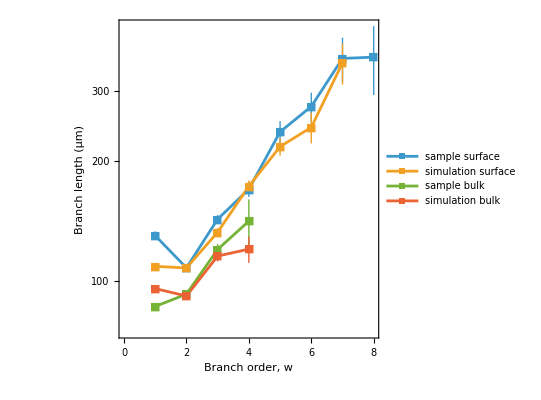

```mathematica
ListLogPlot[{
Table[{z,Around[Mean[#],se[#]]&@VertexList[skeleton,(v_/;branchorder[v]==z):>getpl[v]]},{z,branchorder[1]-1}],
Table[{z,Around[Mean[#],se[#]]&@VertexList[g[[2]],(v_/;rbo[2,v]==z&&v[[1,3]]==0):>rl[v]]},{z,rbo[2,root]-1}],
Table[{z,Around[Mean[#],se[#]]&@VertexList[skeletont,(v_/;branchorder[v]==z):>getpl[v]]},{z,branchorder[1]-1}],
Table[{z,Around[Mean[#],se[#]]&@VertexList[g[[2]],(v_/;rbo[2,v]==z&&v[[1,3]]==1):>rl[v]]},{z,rbo[2,root]-1}]
},ScalingFunctions->"Linear",FrameLabel->{"Branch order, w","Branch length (μm)"},Joined->True,PlotMarkers->{"■"},
PlotLegends->Placed[{"sample surface","simulation surface","sample bulk","simulation bulk"},{Left,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->20},GridLines->Automatic]
```

```mathematica
rwmax=Max[Table[rbo[i,root],{i,100}]];
ListPlot[{Table[Around[Mean[#],1.96se[#]]&@VertexList[skeleton,(v_/;branchorder[v]==z):>getpl[v]],{z,branchorder[1]-1}],
Table[Around[Mean[#],1.96StandardDeviation[#]]&[Cases[Table[VertexList[g[[i]],(v_/;rbo[i,v]==z&&v[[1,3]]==0):>rl[v]],{i,100}],(x_/;Length[x]>1):>Mean[x]]],{z,rwmax-1}],
Table[Around[Mean[#],1.96se[#]]&@VertexList[skeletont,(v_/;branchorder[v]==z):>getpl[v]],{z,branchorder[1]-1}],
Table[Around[Mean[#],1.96StandardDeviation[#]]&[Cases[Table[VertexList[g[[i]],(v_/;rbo[i,v]==z&&v[[1,3]]==1):>rl[v]],{i,100}],(x_/;Length[x]>1):>Mean[x]]],{z,rwmax-1}]
},
FrameLabel->{"Branch order, w","Branch length (μm)"},Joined->True,PlotMarkers->{"■",8},IntervalMarkers->{"Fences","Bands","Fences","Bands"},PlotRange->{{0,10},{0,500}},
PlotLegends->Placed[{"Surface (experiment)","Surface (simulation)","Bulk (experiment)","Bulk (simulation)"},Right],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->6.4},ImageSize->120,GridLines->Automatic,FrameStyle->Black]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

-Graphics-

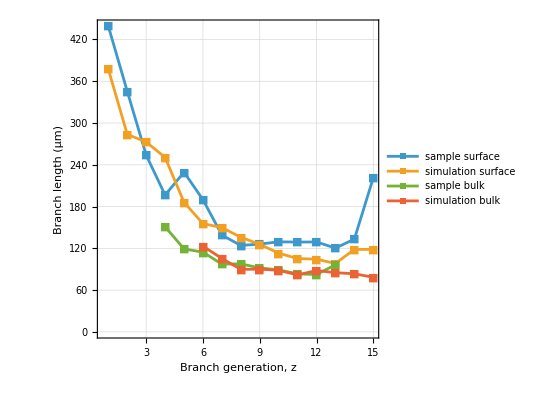

```mathematica
ListPlot[{Table[Mean@VertexList[skeleton,(v_/;getz[v]==z):>getpl[v]],{z,VertexEccentricity[gr,1]}],
Table[Mean@VertexList[g,(v_/;rgetz[v]==z&&v[[1,3]]==0):>rl[v]],{z,VertexEccentricity[g,root]}],
Table[Mean@VertexList[skeletont,(v_/;getz[v]==z):>getpl[v]],{z,VertexEccentricity[gr,1]}],
Table[Mean@VertexList[g,(v_/;rgetz[v]==z&&v[[1,3]]==1):>rl[v]],{z,VertexEccentricity[g,root]}]},
PlotRange->All,FrameLabel->{"Branch generation, z","Branch length (μm)"},Joined->True,PlotMarkers->{"■"},
PlotLegends->Placed[{"sample surface","simulation surface","sample bulk","simulation bulk"},{Right,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->20},GridLines->Automatic]
```

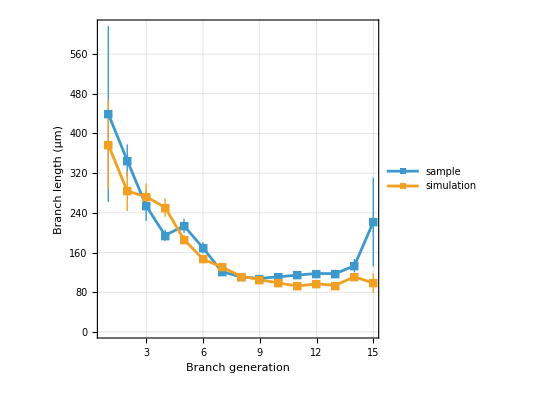

```mathematica
ListPlot[{Table[Around[Mean[#],se[#]]&@VertexList[gr,(v_/;getz[v]==z):>getpl[v]],{z,VertexEccentricity[gr,1]}],
Table[Around[Mean[#],se[#]]&@VertexList[g,(v_/;rgetz[v]==z):>rl[v]],{z,VertexEccentricity[g,root]}]},
PlotRange->All,FrameLabel->{"Branch generation","Branch length (μm)"},Joined->True,PlotMarkers->{"■"},
PlotLegends->Placed[{"sample","simulation"},{Right,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,Large},GridLines->Automatic]
```

```mathematica
ListPlot[{Table[Around[Mean[#],1.96se[#]]&@VertexList[gr,(v_/;getz[v]==z):>getpl[v]],{z,VertexEccentricity[gr,1]}],
Table[Around[Mean[#],1.96StandardDeviation[#]]&[Cases[Table[VertexList[gi,(v_/;rgetz[v]==z):>rl[v]],{gi,g}],(x_/;Length[x]>0):>Mean[x]]],{z,VertexEccentricity[gr,1]}]
},
FrameLabel->{"Branch generation, z","Branch length (μm)"},Joined->True,PlotMarkers->{"■",8},IntervalMarkers->{"Fences","Bands"},FrameStyle->Black,ImageSize->120,PlotRange->{{0,20},{0,600}},
PlotLegends->Placed[{"sample","simulation"},{Right,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->6.4},GridLines->Automatic]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

-Graphics-

ListPlot[{Table[Mean@VertexList[gr, (v_ /; getz[v] == z) :> getpl[v]], {z, VertexEccentricity[gr, 1]}],
  Table[Mean@VertexList[g, (v_ /; rgetz[v] == z) :>  v[[1, 2]] Length[VertexOutComponent[g, v]]^0.2], {z, VertexEccentricity[g, root, Method -> "UnitWeight"]}]}, PlotRange -> All, PlotLegends -> {"Data", "Simulation"}, AxesLabel -> {"Branch generation", "Branch length (μm)"}]

rltr[v_] := ml Sum[w[[1, 2]] Length[VertexOutComponent[g, w]]^0.25, {w, VertexInComponent[g, v][[;; -2]]}];

```mathematica
DensityHistogram[VertexList[gr,(v_/;VertexDegree[gr,v]==1&&getz[v]>2):>{getz[v],ltoroot[v]/1000}],{{1},{0.250}},"PDF",FrameLabel->{"Tip generation, z","Tip-to-root length, mm"},LabelStyle->{Black,FontSize->6.4},ImageSize->115,FrameStyle->Black,ColorFunction->ColorData[{"TemperatureMap",{0.5,-0.5}}],
PlotRange->{{0,20},{0,5},{0,0.5}},PlotRangePadding->None,FrameStyle->Black,GridLines->Automatic,
ChartLegends->Placed[BarLegend[{Automatic,{0,0.5}},LegendLabel->Placed["Probability",Right,Rotate[#,90°]&],LegendMarkerSize->50],{Left,Top}]]
{#,r2[#]}&@LinearModelFit[VertexList[gr,(v_/;VertexDegree[gr,v]==1&&getz[v]>2):>{getz[v],ltoroot[v]}],x,x]
```

-Graphics-

{FittedModel[…],0.646487}

```mathematica
DensityHistogram[VertexList[g,(v_/;VertexDegree[g,v]==1):>{rgetz[v],rltr[v]}],{{1},{250}},FrameLabel->{"Tip generation, z","Tip-to-root length (μm)"},LabelStyle->{Black,FontSize->20},(*PlotRange->{{6,17},{1000,4500}},*)GridLines->Automatic]
LinearModelFit[VertexList[g,(v_/;VertexDegree[g,v]==1):>{rgetz[v],rltr[v]}],x,x]
```

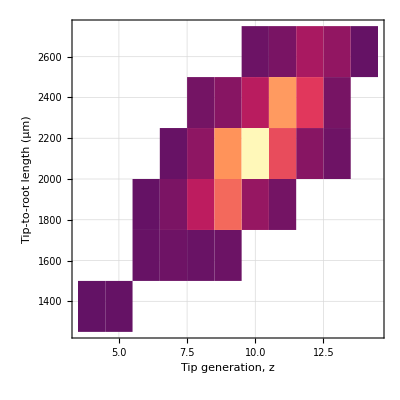
-Graphics-
{FittedModel[…],0.543668}

```mathematica
Module[{gi=g[[3]]},{DensityHistogram[VertexList[gi,(v_/;VertexDegree[gi,v]==1):>{rgetz[v],rltr[gi,v]}],{{1},{250}},FrameLabel->{"Tip generation, z","Tip-to-root length (μm)"},LabelStyle->{Black,FontSize->8},(*PlotRange->{{6,17},{1000,4500}},*)GridLines->Automatic],
{#,r2[#]}&@LinearModelFit[VertexList[gi,(v_/;VertexDegree[gi,v]==1):>{rgetz[v],rltr[gi,v]}],x,x]}//Column]
```

```mathematica
data=Flatten[Table[VertexList[g[[i]],(v_/;VertexDegree[g[[i]],v]==1):>{rgetz[v],rltr[i,v]/1000}],{i,100}],1];
DensityHistogram[data,{{1},{0.250}},"PDF",FrameLabel->{"Tip generation, z","Tip-to-root length (mm)"},LabelStyle->{Black,FontSize->6.4},ImageSize->115,FrameStyle->Black,
PlotRange->{{0,20},{0,5},{0,2.0}},PlotRangePadding->None,ColorFunction->ColorData[{"TemperatureMap",{1.0,-1.0}}],FrameStyle->Black,GridLines->Automatic,ChartLegends->Placed[BarLegend[{Automatic,{0,1.0}},LegendMarkerSize->50,LegendLabel->Placed["Probability",Right,Rotate[#,90°]&]],{Left,Top}]]
fit=LinearModelFit[data,x,x]
```

-Graphics-

FittedModel[<|Type -> Linear, Model -> <|FittedParameters -> {1.6029, 0.052117}, IndependentVariables -> {x}, BasisFunctions -> {1, x}, LinearOffset -> <|Function -> 0, Values -> 0|>|>, KeyNames -> Automatic, Weights -> <|ExampleWeights -> 1.|>, InputData -> {{«2»}, «134560»}, «2», Localizer -> Function[Null, FittedModels`LocalizedBlock[{x}, #1], {HoldAll}], Options -> {}|>]

```mathematica
Clear[data]
```

```mathematica
hists=Table[PDF[SmoothKernelDistribution[VertexList[g[[i]],(v_/;VertexDegree[g[[i]],v]==1):>rltr[i,v]]]],{i,100}];
datay=Table[{x,Around[Mean[#],1.96StandardDeviation[#]+10^-9]&[Table[h[x],{h,hists}]]},{x,0,4000,10}];
```

```mathematica
Show[SmoothHistogram[VertexList[gr,(v_/;VertexDegree[gr,v]==1):>ltoroot[v]/1000],graphsettings,FrameLabel->{"Tip-to-root length (mm)","Probability distribution"},ImageSize->110,PlotRange->{{0,4},{0,6}},PlotLegends->Placed[{"Experiment"},{Left,Top}]],ListLinePlot[Table[{x[[1]]/1000,x[[2]]1000},{x,datay}],IntervalMarkers->"Bands",PlotRange->{{0,4},{0,6}},PlotStyle->ColorData[97,2],graphsettings,PlotLegends->Placed[{"Simulation"},{Left,Top}]]]
```

-Graphics-

```mathematica
Histogram[{Flatten[Table[VertexList[g[[i]],(v_/;VertexDegree[g[[i]],v]==1):>rltr[i,v]],{i,100}]],
VertexList[gr,(v_/;VertexDegree[gr,v]==1):>ltoroot[v]]},Automatic,"PDF",
Frame->True,FrameLabel->{"Tip-to-root length (μm)","Frequency"},AspectRatio->1,GridLines->Automatic,FrameStyle->Black,LabelStyle->{Black,FontSize->6.4},ImageSize->120,PlotRange->{{1000,4000},{0,0.0016}}]
```

-Graphics-

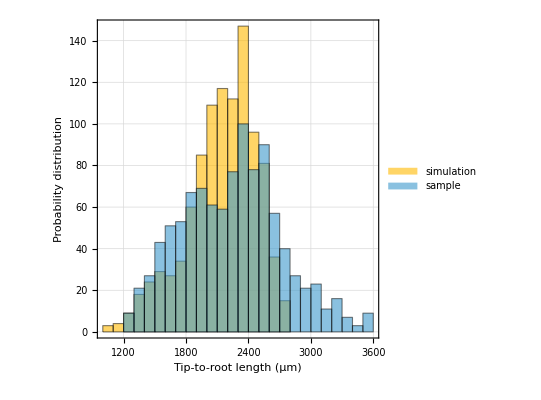

```mathematica
Histogram[{VertexList[g,(v_/;VertexDegree[g,v]==1):>rltr[v]],
VertexList[gr,(v_/;VertexDegree[gr,v]==1):>ltoroot[v]]},(*PlotRange->{10^-5,2 10^-3},ScalingFunctions->"Log10",*)FrameLabel->{"Tip-to-root length (μm)","Probability distribution"},
ChartLegends->Placed[{"simulation","sample"},{Right,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->18},GridLines->Automatic]
```

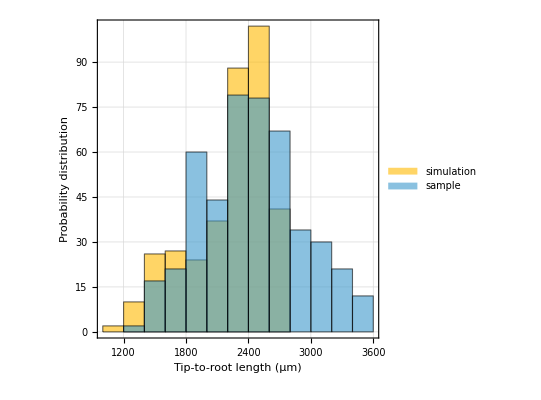

```mathematica
Histogram[{VertexList[g,(v_/;VertexDegree[g,v]==1&&v[[1,3]]==0):>rltr[v]],
VertexList[gr,(v_/;VertexDegree[gr,v]==1&&MemberQ[srftips,v]):>ltoroot[v]]},(*PlotRange->{10^-5,2 10^-3},ScalingFunctions->"Log10",*)FrameLabel->{"Tip-to-root length (μm)","Probability distribution"},
ChartLegends->Placed[{"simulation","sample"},{Right,Top}],Frame->True,AspectRatio->1,LabelStyle->{Black,FontSize->18},GridLines->Automatic]
```

```mathematica
{Mean[#],StandardDeviation[#],cov[#],Skewness[#]}&/@{rltr/@VertexList[g,v_/;VertexDegree[g,v]==1],ltoroot/@ends}//MatrixForm
```

```mathematica
Histogram[{VertexList[g,(v_/;VertexDegree[g,v]==1):>rltr[v]/rgetz[v]],VertexList[gr,(v_/;VertexDegree[gr,v]==1):>ltoroot[v]/getz[v]]},
30,"PDF",ChartLegends->Placed[{"Simulation","Data"},{Right,Top}],Frame->True,FrameLabel->{"(Tip-to-root length)/(Generation) (μm)","pdf"}]
```

```mathematica
{Mean[#],StandardDeviation[#],cov[#],Skewness[#]}&/@{rltr[#]/rgetz[#]&/@VertexList[g,v_/;VertexDegree[g,v]==1],ltoroot[#]/getz[#]&/@ends}//MatrixForm
```

```mathematica
DensityHistogram[Table[{getz[i],ltoroot[i]},{i,srftips}]]
```

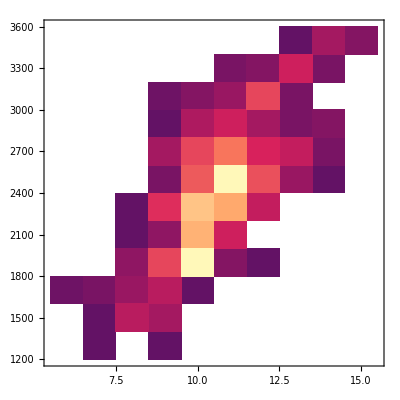

```mathematica
LinearModelFit[Table[{n,Log@Mean[VertexList[skeleton,(v_/;branchorder[v]==n):>getpl[v]]]},{n,2,branchorder[1]-1}],n,n]
```

FittedModel[…]

### Age based on averaged eccentricity

```mathematica
kidgens=Mean[Cases[ends,(i_/;MemberQ[VertexOutComponent[tg,#],i]):>GraphDistance[tg,#,i]]]&/@VertexList[tg];
getkg[i_]:=kidgens[[First@@Position[VertexList[tg],i]]];(*Get kid generation*)
gettw[i_]:=1/(1+getkg[i]);(*Time weight*)
```

```mathematica
ClearAll[agec];
agec[i_]:=agec[i]=Module[{i0=VertexInComponent[tg,i,{1}][[1]]},agec[i0](1-gettw[i0])];
agec[1]=∞;
Do[agec[i]=1,{i,VertexOutComponent[tg,1,{1}]}];
```

```mathematica
ListPlot[VertexList[gr,(v_/;VertexDegree[gr,v]>2&&getz[v]<7):>{getpw[v],agec[v]}],PlotRange->All]
```

```mathematica
agegr[a_]:=Subgraph[gr,VertexList[gr,v_/;agec[v]>1-a]];
```

### Age based on size of subtree

```mathematica
ClearAll[lssage];
lssage[v_]:=lssage[v]=Log2[Length[VertexOutComponent[tg,v]]+1];
```

```mathematica
lssage[v_]:=Module[{ss=Length[VertexOutComponent[tg,v]]},If[ss==1,0,Log2[ss-1]]];
dlssage[v_]:=lssage[getp[v]]-lssage[v];
dlssage[1]=0;
```

```mathematica
amin=3;amax=9.7;
scaledage[v_]:=amin+(amax-amin)(1-lssage[v]/lssage[1]);
```

```mathematica
{Length[#],Total[getpl/@#]}&[VertexList[gr,v_/;scaledage[v]<6]]
```

```mathematica
DiscretePlot[VertexCount[gr,v_/;scaledage[v]<t],{t,4.5,9.7,0.5},ScalingFunctions->"Log",GridLines->Automatic]
```

```mathematica
BoxWhiskerChart[Table[VertexList[gr,(v_/;scaledage[v]==Around[t,0.5]):>getpw[v]],{t,4.0,10.2,1.0}],ChartLabels->Range[4.0,10.2,1.0]]
```

```mathematica
LinearModelFit[Table[{t,Mean@VertexList[gr,(v_/;scaledage[v]==Around[t,0.25]):>getpw[v]]},{t,5.0,9.0,0.5}],x,x]
```

```mathematica
ListPlot[{lssage[#],getpl[#]}&/@VertexList[gr],PlotRange->All]
```

### Age based on vertex eccentricity

```mathematica
ClearAll[veagec];
ve[v_]:=VertexEccentricity[tg,v];
veagec[v_]:=veagec[v]=Module[{v0=getp[v]},veagec[v0](1-1/(ve[v]+1))];
veagec[1]=1;
```

### Lumen vs epithelium

```mathematica
epithelium=Table[getpw/@Sort[VertexList[gr,v_/;getz[v]==z],getpl[#1]>getpl[#2]&],{z,VertexEccentricity[tg,1]}];
```

```mathematica
lumen=Table[getpw/@Sort[VertexList[gr,v_/;getz[v]==z],getpl[#1]>getpl[#2]&],{z,VertexEccentricity[tg,1]}];
```

```mathematica
lw=Table[Mean[VertexList[gr,(v_/;getz[v]==z):>getpw[v]]],{z,VertexEccentricity[tg,1]}];
ll=Table[Mean[VertexList[gr,(v_/;getz[v]==z):>getpl[v]]],{z,VertexEccentricity[tg,1]}];
```

```mathematica
ew=Table[Mean[VertexList[gr,(v_/;getz[v]==z):>getpw[v]]],{z,VertexEccentricity[tg,1]}];
el=Table[Mean[VertexList[gr,(v_/;getz[v]==z):>getpl[v]]],{z,VertexEccentricity[tg,1]}];
```

```mathematica
ListPlot[ew[[;;Length[lw]]]-lw]
```

### Hooper

```mathematica
toposize[v_]:=Length[DeleteCases[VertexOutComponent[tg,v],v]];
totlen[v_]:=Total[getpl/@DeleteCases[VertexOutComponent[tg,v],v]];
totvol[v_]:=Total[π getpl[#]getpw[#]^2&/@DeleteCases[VertexOutComponent[tg,v],v]];
epid=0;
ClearAll[lumvol2];
lumvol2[v_]:=lumvol2[v]=Sum[lumvol2[w],{w,VertexOutComponent[tg,v,{1}]}]+π/4 getpl[v](getpw[v]-epid)^2;
lumvol2[1];
```

```mathematica
nmin=2;
fit=LinearModelFit[VertexList[gr,(v_/;branchorder[v]>=nmin&&getz[v]>1):>{Log[getpw[v]-epid],Log[lumvol2[v]]}],x,x];
#[fit]&/@{r2,pcit}
```

{0.778359, | Estimate | Standard Error | Confidence Interval
1 | 1.17718 | 0.146123 | {0.890602,1.46376}
x | 3.30786 | 0.0407318 | {3.22797,3.38774}}

```mathematica
pcit[fit]
```

| Estimate | Standard Error | Confidence Interval
1 | 1.17718 | 0.146123 | {0.890602,1.46376}
x | 3.30786 | 0.0407318 | {3.22797,3.38774}

```mathematica
r2[fit]
```

0.778359

```mathematica
Show[DensityHistogram[VertexList[gr,(v_/;branchorder[v]>=nmin):>{getpw[v]-epid,lumvol2[v]}],{"Log","Log"},ImageSize->122,
PlotRange->{{Log[5],Log[200]},{3Log[10],9Log[10]}},GridLines->Automatic,FrameStyle->Black,PlotRangePadding->None,ColorFunction->ColorData[{"TemperatureMap",{0.5,-0.5}}],ChartLegends->Placed[BarLegend[{Automatic,{0,0.5}},LegendLabel->Placed["Probability",Right,Rotate[#,90°]&],LabelStyle->{Black,FontSize->6.4},LegendMarkerSize->50],{Left,Top}]],
ListLinePlot[Table[{x,bfa[fit]},{x,Log[Min[getpw/@VertexList[gr,v_/;VertexDegree[gr,v]>1]]-epid],Log[Max[getpw/@VertexList[gr]]-epid],0.1}],IntervalMarkers->"Bands",PlotStyle->Black],LabelStyle->{FontSize->6.4,Black},FrameLabel->{"Branch lumen diameter (μm)","Subtree volume (μm^3)"}]
```

-Graphics-

```mathematica
ColorFunction->ColorData[{"TemperatureMap",{0.5,-0.5}}],
```

```mathematica
ChartLegends->Placed[BarLegend[{Automatic,{0,0.5}},LegendLabel->Placed["Probability",Right,Rotate[#,90°]&],LegendMarkerSize->50],{Left,Top}]
```

### Length difference multigen

```mathematica
DensityHistogram[Table[{getz[e],ltoroot[e]},{e,ends}]]
```

```mathematica
data=Table[Module[{v=RandomSample[ends,2]},{getz[v[[1]]]-getz[v[[2]]],ltoroot[v[[1]]]-ltoroot[v[[2]]]}],{i,10000}];
```

```mathematica
DistributionChart[Table[Cases[data,(x_/;x[[1]]==z):>x[[2]]],{z,-9,9}]]
```

```mathematica
SmoothHistogram[Table[Cases[data,(x_/;x[[1]]==z):>x[[2]]],{z,-9,9}][[7;;14]]]
```

```mathematica
{ListPlot[#],LinearModelFit[#,x,x]}&[Table[{z,Mean@Cases[data,(x_/;x[[1]]==z):>x[[2]]]},{z,0,9}]]
```

```mathematica
{ListPlot[#],LinearModelFit[#,x,x]}&[Table[{Mean[#],StandardDeviation[#]}&@Cases[data,(x_/;x[[1]]==z):>x[[2]]],{z,5}]]
```

### Expansion analysis

```mathematica
data=VertexList[gr,(v_/;getz[v]==3):>({Length[#],getpl[v],Total[getpl/@#],Mean[getz/@Cases[#,u_/;MemberQ[ends,u]]]-getz[v]//N,Mean[ltoroot/@Cases[#,u_/;MemberQ[ends,u]]]-ltoroot[v]}&[VertexOutComponent[tg,v]])]
```

```mathematica
LinearModelFit[Table[{x[[1]],x[[3]]},{x,data}],x,x]
```

Elongation of first branch

```mathematica
ListPlot[Table[{4+n/2,Evaluate[170n (1-x)/(1-x^n)/.{x->0.794}]},{n,6,16}],Joined->True]
```

Tip length

```mathematica
ListPlot[Table[{{4+n/2,Evaluate[430n ((1-x)x^(n-1))/(1-x^n)/.{x->0.794}]},{4+n/2,Evaluate[430 6 ((1-x)x^(n-1))/(1-x^n)/.{x->0.794}]},{4+n/2,600Exp[-0.162n]}},{n,6,13}]//Transpose,Joined->True,PlotRange->{Automatic,{0,Automatic}},PlotStyle->{Automatic,Automatic,Dashed},PlotLegends->{"Expansion","No expansion","Observed"}]
```

Total duct length

```mathematica
ListLogPlot[Table[{{4+n/2,Evaluate[700n (1-x)/(2x-1)((2x)^n-1)/(1-x^n)/.{x->0.794}]},{4+n/2,Evaluate[700 6 (1-x)/(2x-1)((2x)^n-1)/(1-x^n)/.{x->0.794}]},{4+n/2,13.05Exp[1.107(4+n/2)]}},{n,6,13}]//Transpose,Joined->True,PlotRange->{Automatic,{0,Automatic}},PlotStyle->{Automatic,Automatic,Dashed},PlotLegends->{"Expansion","No expansion","Observed"}]
```

### Aged graph analysis

```mathematica
agedgraph[a_]:=Subgraph[gr,VertexList[gr,v_/;zintage[v]<=a]];
```

LU full

```mathematica
3.678+0.7676Log[VertexCount[mygraph]]
```

```mathematica
3.51+0.7305Log[VertexCount[mygraph]]
```

```mathematica
ListPlot[Table[Module[{mygraph=agedgraph[a]},{a,Log[VertexCount[mygraph]/0.0209]/1.2679}]
,{a,0.0,1.03,0.03}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"scaled age","age (PCW)"}]
```

```mathematica
mygraph=agedgraph[0.5];
skelgraphics[mygraph]
```

```mathematica
skelgraphics[Subgraph[gr,VertexList[gr,v_/;getz[v]<=7]]]
```

```mathematica
mygraph=agedgraph[0.5];
ListLogPlot[Sort@Tally[VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>getz[v]]],AspectRatio->1,Joined->True,Filling->Bottom,PlotMarkers->{"■"}]
```

```mathematica
ListLogPlot[Table[
Module[{mygraph=agedgraph[a],tipz},
tipz=VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>getz[v]];
Sort@Tally@tipz]
,{a,0.3,1.2,0.2}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,Filling->Bottom,Frame->True]
```

```mathematica
ListPlot[Table[
Module[{mygraph=agedgraph[a],tipz},
tipz=VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>getz[v]];
{a,cov[#]}&[tipz]]
,{a,0.3,1,0.05}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,Filling->Bottom,Frame->True]
```

```mathematica
data=Table[
Module[{mygraph=agedgraph[a],tipz},
tipz=VertexList[mygraph,(v_/;VertexDegree[mygraph,v]==1):>getz[v]];
{Mean[tipz],StandardDeviation[tipz]}]
,{a,0.2,1,0.05}];
fit=LinearModelFit[data,x,x];
```

```mathematica
Show[ListPlot[data,Joined->True,PlotMarkers->{"■"},Filling->Bottom,AxesLabel->{"Mean z","STD z"}],Plot[{fit[x],0.2948+0.1246x},{x,0,20},PlotStyle->Dashed]]
```

```mathematica
Show[ListLogPlot[Table[
Module[{mygraph=agedgraph[a]},{3.51+0.7305Log[VertexCount[mygraph]],voxel^3 Volume[ConvexHullMesh[xyz[[#]]&/@VertexList[mygraph]]]}]
,{a,0.2,1,0.05}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,Filling->Bottom,GridLines->Automatic,AxesLabel->{"Age","CVX Hull vol"}],LogPlot[3 10^6 Exp[0.891x],{x,6.5,10.5},PlotStyle->Dashed]]
```

```mathematica
Show[ListPlot[Table[
Module[{mygraph=agedgraph[a],myends},myends=VertexList[mygraph,v_/;VertexDegree[mygraph,v]==1];{3.51+0.7305Log[VertexCount[mygraph]],Mean[ltoroot/@myends]}]
,{a,0.1,1,0.05}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,Filling->Bottom,GridLines->Automatic,AxesLabel->{"Age","Mean L-to-root"}],Plot[500(x-4),{x,5,10.5},PlotStyle->Dashed],PlotRange->All]
```

```mathematica
Show[ListLogPlot[Table[
Module[{mygraph=agedgraph[a],myends,t},myends=VertexList[mygraph,v_/;VertexDegree[mygraph,v]==1];
t=3.51+0.7305Log[VertexCount[mygraph]];{t,Mean[getpl/@myends]}]
,{a,0.1,1,0.05}],Joined->True,PlotMarkers->{"■"},AspectRatio->1,Filling->Bottom,GridLines->Automatic,AxesLabel->{"Age","Mean L-to-root"}],LogPlot[120 2(t-4)(3/4)^(2(t-4)-1),{t,4.5,10.5},PlotStyle->Dashed],PlotRange->All]
```

```mathematica
LinearModelFit[Table[Module[{mygraph=agedgraph[a],myends,t},myends=VertexList[mygraph,v_/;VertexDegree[mygraph,v]==1];t=3.51+0.7305Log[VertexCount[mygraph]];{t,Log@Mean[getpl/@myends]}],{a,0.1,1,0.05}],t,t]
```

Needs HW

```mathematica
Show[ListPlot[{
Table[Module[{mygraph=agedgraph[a]},{3.678+0.7676Log[VertexCount[mygraph]],VertexCount[mygraph,v_/;MemberQ[VertexList[skeleton],v]]/VertexCount[mygraph]}],{a,0.2,1,0.05}]
(*Table[Module[{mygraph=agedgraph[a]},{3.678+0.7676Log[VertexCount[mygraph]],VertexCount[mygraph,v_/;MemberQ[hwjuncs,v]]/VertexCount[mygraph,v_/;MemberQ[VertexList[Highways],v]]}],{a,0.2,1,0.05}]*)
},Joined->True,PlotMarkers->{"■"},AspectRatio->1,GridLines->Automatic,AxesLabel->{"Age","Fraction"},PlotLegends->{"HW branches / all branches","HW bif / HW branches"}],
Plot[{11.92Exp[-0.365x](*,0.4213-0.0245x*)},{x,6,12},PlotStyle->Dashed]]
```

```mathematica
Show[ListLogPlot[{
Table[Module[{mygraph=agedgraph[a]},{3.51+0.7305Log[VertexCount[mygraph]],VertexCount[mygraph,v_/;MemberQ[VertexList[Highways],v]]}],{a,0.2,1,0.05}],
Table[Module[{mygraph=agedgraph[a]},{3.51+0.7305Log[VertexCount[mygraph]],VertexCount[mygraph,v_/;MemberQ[hwjuncs,v]]}],{a,0.2,1,0.05}]
},Joined->True,PlotMarkers->{"■"},AspectRatio->1,GridLines->Automatic,Frame->True],
LogPlot[{0.053Exp[x],0.0281Exp[0.894x],0.0082Exp[1.396x]},{x,5,10.5},PlotStyle->Dashed],PlotRange->All]
```

```mathematica
Show[ListLogLogPlot[
Table[Module[{mygraph=agedgraph[a]},{voxel^3 Volume[ConvexHullMesh[xyz[[#]]&/@VertexList[mygraph]]],VertexCount[mygraph,v_/;MemberQ[hwjends,v]]}],{a,0.2,1,0.05}],
Joined->True,PlotMarkers->{"■"},AspectRatio->1,GridLines->Automatic,AxesLabel->{"Volume (μm^3)","Highway branches"}],LogLogPlot[2 10^-8 x,{x,10^8,10^12},PlotStyle->Dashed]]
```

```mathematica
(*mygraph=agedgraph[0.55];*)
mygraph=gr;
colorscheme=ColorData[{"SolarColors",{0,90}}];
mycolors=Table[Module[{e2=Last@SortBy[e,getz]},If[getz[e2]<=1,colorscheme[0],colorscheme[palignd[e2]]]],{e,EdgeList[mygraph]}];
```

```mathematica
Graphics3D[Transpose@{mycolors,Table[{Tube[{xyz[[e[[1]]]],xyz[[e[[2]]]]},5]},{e,EdgeList[mygraph]}]},SphericalRegion->True,Boxed->False,ImageSize->BoundingRegion[4xyz[[#]]&/@VertexList[mygraph],"MinBall"][[2]]/10]
```

## Tip length histograms, rescaled, combined

```mathematica
l4310s1=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips.csv"];
l4310s2=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips2.csv"];
l4310b1=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips.csv"];
l4310b2=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips2.csv"];
```

```mathematica
l4437s1=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips.csv"];
l4437s2=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips2.csv"];
l4437b1=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips.csv"];
l4437b2=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips2.csv"];
```

```mathematica
l3822s1=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips.csv"];
l3822s2=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips2.csv"];
l3822b1=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips.csv"];
l3822b2=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips2.csv"];
```

```mathematica
Grid@{{Mean[#],cov[#]}&[ToExpression/@Pick[#[[3,All]],#=="TRUE"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3570-P7.9\\tips.csv"]],{Mean[#],cov[#]}&[ToExpression/@Pick[#[[3,All]],#=="FALSE"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3570-P7.9\\tips.csv"]]}
```

```mathematica
samples={l4310s1,l4437s1,l3822s1,l4310b1,l4437b1,l3822b1};
samples2={l4310s2,l4437s2,l3822s2,l4310b2,l4437b2,l3822b2};
legends={"PCW8.3 (srf.)","PCW9.4 (srf.)","PCW10.2 (srf.)","PCW8.3 (bulk)","PCW9.4 (bulk)","PCW10.2 (bulk)"};
(*legends={"6.9","week 7.9","8.7","9.7","10.2","simulation"};*)
dists=Table[PDF[SmoothKernelDistribution[x/Mean[x]]],{x,samples}];
dists2=Table[PDF[SmoothKernelDistribution[x/Mean[x]]],{x,samples2}];
```

```mathematica
srfq="True";
eh36851=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\tips.csv"];
eh36852=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\tips2.csv"];
eh44521=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4452-P9.4\\tips.csv"];
eh44522=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4452-P9.4\\tips2.csv"];
eh38221=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips.csv"];
eh38222=ToExpression/@Pick[#[[3,All]],#==srfq&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips2.csv"];
```

```mathematica
eh387921=ToExpression/@Pick[#[[3,All]],#=="True"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\GW13-P12.0\\tips2.csv"];
eh387922=ToExpression/@Pick[#[[3,All]],#=="False"&/@#[[2,All]]]&@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\GW13-P12.0\\tips2.csv"];
```

```mathematica
data=eh387921;
co=30;
dist=EstimatedDistribution[DeleteCases[data,x_/;x<co],LogLogisticDistribution[a,b]]
Show[Histogram[DeleteCases[data,x_/;x<co],50,"PDF",graphsettings,ImageSize->120,PlotRange->{{0,200},{0,0.03}},PlotRangePadding->None,FrameLabel->{"Surface branch (w=2) length (μm)","Probability distribution"},ChartStyle->Lighter[Red]],
Plot[PDF[dist][x],{x,0,200},PlotStyle->{Thickness[0.01],Red}]]
```

LogLogisticDistribution[5.56611,66.9953]

-Graphics-

```mathematica
data=eh387922;
co=30;
dist=EstimatedDistribution[DeleteCases[data,x_/;x<co],LogLogisticDistribution[a,b]]
Show[Histogram[DeleteCases[data,x_/;x<co],50,"PDF",graphsettings,ImageSize->120,PlotRange->{{0,140},{0,0.035}},PlotRangePadding->None,FrameLabel->{"Bulk branch (w=2) length (μm)","Probability distribution"},ChartStyle->Darker[LightBlue]],
Plot[PDF[dist][x],{x,0,200},PlotStyle->{Thickness[0.01],Blue}]]
```

LogLogisticDistribution[6.46607,61.093]

-Graphics-

```mathematica
Show[SmoothHistogram[#/Mean[#]&/@{eh38221,eh44521,eh36851,eh38222,eh44522,eh36852},graphsettings,ScalingFunctions->"Log10",PlotRange->{{0,4},{10^-3,10}},
FrameLabel->{"(Branch length)/(Mean branch length)","Probability distribution"},PlotLegends->{"PCW10.2","PCW9.4","PCW8.7"},ImageSize->125,PlotStyle->(Directive[#,Thickness[0.01]]&/@{Automatic,Automatic,Automatic,{Dashed,ColorData[97,1]},{Dashed,ColorData[97,2]},{Dashed,ColorData[97,3]}})],Plot[{PDF[GammaDistribution[a,1/a]/.{a->3.28},x],PDF[LogLogisticDistribution[a,Sinc[π/a]]/.{a->5.00},x]},{x,0,4},PlotStyle->(Directive[#,Black,Thickness[0.015]]&/@{Automatic,Dashed}),PlotLegends->{"Universal"},LabelStyle->{Black,FontSize->6.4},ScalingFunctions->"Log10"]]
```

-Graphics-

```mathematica
Sinc[π/6.61]
```

0.962775

```mathematica
Show[SmoothHistogram[#/Mean[#]&/@{eh38222,eh44522,eh36852},graphsettings,ScalingFunctions->"Log10",PlotRange->{{0,4},{10^-3,10}},FrameLabel->{"(Branch len.)/(Mean branch len.)","Frequency"},PlotLegends->{"PCW10.2","PCW9.4","PCW8.7"},ImageSize->125,PlotStyle->Thickness[0.01]],Plot[PDF[LogLogisticDistribution[a,Sinc[π/a]]/.{a->5.6},x],{x,0,4},PlotStyle->Directive[Black,Dashed,Thickness[0.015]],ScalingFunctions->"Log10"]]
```

-Graphics-

```mathematica
EstimatedDistribution[#,LogLogisticDistribution[a,b]]&/@{eh36852,eh44522,eh38222}
```

{LogLogisticDistribution[5.64669,100.215],LogLogisticDistribution[5.31413,96.6534],LogLogisticDistribution[5.78769,73.6944]}

```mathematica
Mean[{5.65,5.314,5.788}]
```

5.584

```mathematica
EstimatedDistribution[#,GammaDistribution[a,b]]&/@{eh36851,eh44521,eh38221}
```

{GammaDistribution[3.34207,33.1694],GammaDistribution[2.95639,35.1121],GammaDistribution[3.94234,17.4967]}

```mathematica
Mean[{3.34,2.96,3.94}]
```

3.41333

```mathematica
tipdata=getpl/@ends(*+RandomReal[65,Length[ends]]*);
tip2data=getpl/@ends2;
```

```mathematica
dx=2;
rng=Range[10,500,dx];
tipboot=RandomChoice[tipdata,{400,Length[eh44521]}];
fits=SmoothKernelDistribution/@tipboot;
pdftabl=Table[PDF[f,rng],{f,fits}];
pdflist=Around[Mean[#]+10^-9,{Mean[#]-Quantile[#,0.025]+10^-10,Quantile[#,0.975]-Mean[#]+10^-10}]&/@Transpose[pdftabl];

tip2boot=RandomChoice[tip2data,{400,Length[eh44522]}];
fits2=SmoothKernelDistribution/@tip2boot;
pdf2tabl=Table[PDF[f,rng],{f,fits2}];
pdf2list=Around[Mean[#]+10^-9,{Mean[#]-Quantile[#,0.025]+10^-10,Quantile[#,0.975]-Mean[#]+10^-10}]&/@Transpose[pdf2tabl];
```

dx=10;
rng=Range[10,400,dx];
pdflist=1/(dx Length[eh36851])Table[Around[Mean[#],{Quantile[#,0.025],Quantile[#,0.975]}]&@Map[Count[#,i_/;x<=i<x+dx]&,tipboot],{x,rng}];
pdf2list=1/(dx Length[eh36852])Table[Around[Mean[#],{Quantile[#,0.025],Quantile[#,0.975]}]&@Map[Count[#,i_/;x<=i<x+dx]&,tip2boot],{x,rng}];

```mathematica
pdf1=Table[PDF[SmoothKernelDistribution[eh44521]][x],{x,rng}];
pdf2=Table[PDF[SmoothKernelDistribution[eh44522]][x],{x,rng}];
ListPlot[Transpose[{rng,#}]&/@{pdf1,pdflist,pdf2,pdf2list},Joined->True,graphsettings,ImageSize->125,FrameLabel->{"Surface branch length (μm)","Probability distribution"},
IntervalMarkers->"Bands",ScalingFunctions->"Log10",PlotStyle->Thickness[0.01],PlotRange->{{0,500},{10^-5,10^-1}},PlotLegends->Placed[{"Tips exp.","Tips sim.","Order 2 exp.","Order 2 sim."},Right]]
```

-Graphics-

```mathematica
Export["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung project writing\\figures\\figure_6\\tip_tip2_len_vs_sim.pdf",
ListLinePlot[Transpose[{rng,#}]&/@{eh36pdf1,pdflist,eh36pdf2,pdf2list},graphsettings,ImageSize->120,FrameLabel->{"Branch length (μm)","Frequency"},
IntervalMarkers->"Bands",IntervalMarkersStyle->Opacity[0.2],ScalingFunctions->"Log10",PlotRange->{{10,400},{10^-5,10^-1}},PlotLegends->Placed[{"Tips exp.","Tips sim.","Order 2 exp.","Order 2 sim."},Right]],
"PDF","UseFrontEnd"->True]
```

C:\Users\ivanl\OneDrive - University of Cambridge\lung project writing\figures\figure_6\tip_tip2_len_vs_sim.pdf

#### Plotting

```mathematica
dx=2;
rng=Range[0,250,dx];
```

```mathematica
exppairs=VertexList[skeleton,(v_/;boh[v]==2&&VertexDegree[skeleton,v]==3):>getpl/@VertexOutComponent[tg,v,{1}]];
```

```mathematica
expdiffs=Abs[#[[1]]-#[[2]]]&/@exppairs;
exppdf=PDF[SmoothKernelDistribution[expdiffs]];
exppdflist=Table[exppdf[x],{x,rng}];
```

```mathematica
simpairs=VertexList[gr,(v_/;boh[v]==2):>getpl/@VertexOutComponent[tg,v,{1}]];
```

```mathematica
simpairsadd=simpairs+RandomReal[110,Dimensions[simpairs]];
```

```mathematica
diffdata=Abs[#[[1]]-#[[2]]]&/@simpairsadd;
tipboot=RandomChoice[diffdata,{1000,Length[exppairs]}];
fits=SmoothKernelDistribution/@tipboot;
pdftabl=Table[PDF[f,rng],{f,fits}];
pdflist=Around[Mean[#]+10^-9,{Mean[#]-Quantile[#,0.025]+10^-10,Quantile[#,0.975]-Mean[#]+10^-10}]&/@Transpose[pdftabl];
```

```mathematica
ListLinePlot[Transpose[{rng,#}]&/@{exppdflist,pdflist},ImageSize->125,IntervalMarkers->"Bands",PlotStyle->Thickness[0.01],graphsettings,ScalingFunctions->"Log10",PlotRange->{{0,250},{10^-5,10^-1}},FrameLabel->{"Surface tip length difference (μm)","Probability distribution"},PlotLegends->Placed[{"Experiment","Simulation"},Right]]
```

-Graphics-

```mathematica
include={True,True,True,True,True,True};
```

```mathematica
(*λ=Mean[l3685]/Mean[sim];aexp=Count[l3685,x_/;x>70]/Length[l3685];asim=Count[sim,x_/;x>70]/Length[sim];*)
Plot[Evaluate[Flatten[{Table[f[x],{f,Pick[dists,include]}](*,aexp/asim λ dists[[6]][λ x]*)}]],{x,0,400},PlotRange->{{0,4},{0.0,Automatic}},ScalingFunctions->"Linear",AspectRatio->1,Frame->True,GridLines->Automatic,LabelStyle->{Black,FontSize->20},FrameStyle->Black,GridLinesStyle->Dashed,FrameLabel->{"Rescaled tip length (a.u.)","Probability distribution"},PlotLegends->Pick[legends,include]]
```

```mathematica
Plot[Evaluate[Table[f[x],{f,Pick[dists2,include]}]],{x,0,4},PlotRange->{{0,4},Automatic},ScalingFunctions->"Linear",
AspectRatio->1,Frame->True,GridLines->Automatic,LabelStyle->{Black,FontSize->20},FrameStyle->Black,GridLinesStyle->Dashed,
FrameLabel->{"Rescaled order 2 branch length (a.u.)","Probability distribution"},ImageSize->Medium,PlotLegends->Placed[Pick[legends,include],Right]]
```

```mathematica
Show[Plot[dists[[3]][x],{x,0,500},
Frame->True,LabelStyle->{Large,Black},GridLines->Automatic,AspectRatio->1,
PlotRange->{{0,500},{0,0.01}},PlotLegends->Placed[{"Tip"},{Right,Top}],FrameLabel->{"Length (μm)","Probability"}],Plot[dists2[[3]][x],{x,0,500},PlotStyle->Dashed,PlotLegends->Placed[{"Ord. 2"},{Right,Top}],LabelStyle->{Large,Black}]
]
```

```mathematica
eh2987=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH2987-P4.7\\tips.csv"][[5,All]];
eh4309=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4309-P6.3\\tips.csv"][[5,All]];
eh4310=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4310-P8.3\\tips.csv"][[5,All]];
eh4437=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips.csv"][[5,All]];
eh3822=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips.csv"][[5,All]];
```

```mathematica
fit1=EstimatedDistribution[eh2987,LogNormalDistribution[a,b]];
fit2=EstimatedDistribution[eh4309,LogNormalDistribution[a,b]];
fit3=EstimatedDistribution[eh4310,LogNormalDistribution[a,b]];
fit4=EstimatedDistribution[eh4437,LogNormalDistribution[a,b]];
fit5=EstimatedDistribution[eh3822,LogNormalDistribution[a,b]];
```

```mathematica
fit1=SmoothKernelDistribution[eh2987];
fit2=SmoothKernelDistribution[eh4309];
fit3=SmoothKernelDistribution[eh4310];
fit4=SmoothKernelDistribution[eh4437];
fit5=SmoothKernelDistribution[eh3822];
```

```mathematica
Show[SmoothHistogram[{eh2987,eh4309,eh4310,eh4437,eh3822},ScalingFunctions->"Log",Frame->True,FrameStyle->Black,LabelStyle->{FontSize->6.4,Black},AspectRatio->1,PlotRange->{{0,6000},{10^-5, 10^-2}},FrameLabel->{"Tip-to-root length (μm)","Probability distribution"},PlotLegends->{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},GridLines->Automatic,ImageSize->125,ImagePadding->{{30,5},{30,5}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,-2}],None},{Table[i,{i,0,8000,2000}],None}}]
(*,Plot[Evaluate[PDF[#,x]&/@{fit1,fit2,fit3,fit4,fit5}],{x,10,8 10^3},PlotStyle->Dashed,ScalingFunctions->"Log",PlotRange->{10^-5,0.1}]*)]
```

```mathematica
Show[ListLinePlot[Table[{x,PDF[#,x]},{x,0,6000,30}]&/@{fit1,fit2,fit3,fit4,fit5},ScalingFunctions->"Log10",Frame->True,FrameStyle->Black,LabelStyle->{FontSize->6.4,Black},AspectRatio->1,PlotRange->{{0,6000},{10^-5, 10^-2}},FrameLabel->{"Tip-to-root length (μm)","Probability distribution"},PlotLegends->Placed[{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},Right],GridLines->Automatic,ImageSize->125,ImagePadding->{{30,5},{30,5}}(*,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,-2}],None},{Table[i,{i,0,8000,2000}],None}}*)]
(*,Plot[Evaluate[PDF[#,x]&/@{fit1,fit2,fit3,fit4,fit5}],{x,10,8 10^3},PlotStyle->Dashed,ScalingFunctions->"Log",PlotRange->{10^-5,0.1}]*)]
```

```mathematica
Show[SmoothHistogram[#/Mean[#]&/@{eh2987,eh4309,eh4310,eh4437,eh3822},ScalingFunctions->"Log10",Frame->True,FrameStyle->Black,LabelStyle->{FontSize->6.4,Black},AspectRatio->1,PlotRange->{{0,2},{10^-2,10^1}},FrameLabel->{"(TtRL)/(mean TtRL)","Probability distribution"},PlotLegends->{"PC6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},GridLines->Automatic,ImageSize->125],Plot[PDF[LogNormalDistribution[-0.018,0.19],x],{x,0,2},ScalingFunctions->"Log10",PlotStyle->{Black,Dashed}]]
```

```mathematica
eh2987=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH2987-P4.7\\tips.csv"][[1,All]];
eh4309=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4309-P6.3\\tips.csv"][[1,All]];
eh3570=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3570-P7.9\\tips.csv"][[1,All]];
eh4627=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4627-P8.0\\tips.csv"][[1,All]];
eh4310=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4310-P8.3\\tips.csv"][[1,All]];
eh3547=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3547-P8.7\\tips.csv"][[1,All]];
eh4326=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4326-P9.7\\tips.csv"][[1,All]];
eh4437=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4437-P9.4\\tips.csv"][[1,All]];
eh3822=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips.csv"][[1,All]];
```

```mathematica
{eh2987,eh4309,eh4310,eh4437,eh3822}
```

```mathematica
ListPlot[Sort@Tally@#&/@{eh2987,eh4309,eh4310,eh4437,eh3822},Joined->True,PlotMarkers->{"■",8},ScalingFunctions->"Log10",Frame->True,LabelStyle->{FontSize->6.4,Black},PlotRange->{{0,25},{10^0,10^4}},FrameStyle->Black,AspectRatio->1,FrameLabel->{"Tip generation, z","Number of tips, m_z"},ImageSize->120,PlotLegends->Placed[{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},Right],GridLines->Automatic]
```

```mathematica
normalization[x_]:=Module[{xst=Sort@Tally@x,tot,m},
tot=Total[xst[[All,2]]];
m=Total[xst[[All,1]]xst[[All,2]]]/tot;
Transpose@{xst[[All,1]]/m,m xst[[All,2]]/tot}];
```

```mathematica
eh4309=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4309-P6.3\\tips.csv"][[1,All]];
eh4627=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4627-P8.0\\tips.csv"][[1,All]];
eh3549=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips.csv"][[1,All]];
eh3547=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3547-P8.7\\tips.csv"][[1,All]];
eh4452=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4452-P9.4\\tips.csv"][[1,All]];
eh38791=ToExpression/@Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH38791-P11.1\\tips.csv"][[1,All]];
```

```mathematica
Show[ListPlot[normalization/@{eh2987,eh4309,eh4310,eh4437,eh3822},FrameStyle->Black,Joined->False,PlotMarkers->{"■",8},
PlotLegends->Placed[{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},Right],AspectRatio->1,Frame->True,GridLines->Automatic,LabelStyle->{Black,FontSize->6.4},PlotRange->{{0,2.0},{10^-3,10^1}},ImageSize->125,
FrameLabel->{"(Tip generation)/(mean generation)","Probability distribution"},ScalingFunctions->"Log10"],
Plot[PDF[LogNormalDistribution[-0.0128,0.16],x],{x,0,3},PlotStyle->{Black,Dashed},ScalingFunctions->"Log10"]]
```

```mathematica
SmoothHistogram[#/Mean[#]&/@{gw10,eh3549,eh3685,eh4437,eh3138,eh3822},(*ScalingFunctions->"Log10",*)Frame->True,GridLines->Automatic,LabelStyle->{FontSize->20,Black},AspectRatio->1,(*PlotRange->{0.005,5},*)FrameLabel->{"Tip-to-root length (rescaled)","Probability"},PlotLegends->Placed[{"PCW8.0","PCW8.3","PCW8.7","PCW9.4","PCW9.7","PCW10.2"},{Right,Top}]]
```

```mathematica
eh4441=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3570-P7.9\\tips2.csv"][[3]];
eh4437=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3685-P8.7\\tips2.csv"][[3]];
eh3822=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3822-P10.2\\tips2.csv"][[3]];
```

```mathematica
SmoothHistogram[#/Mean[#]&/@{eh4441,eh4437,eh3822(*,getpl/@ends2*)},Automatic,"PDF",ScalingFunctions->"Log10",PlotRange->{{0,3},{10^-3,10}}(*{{0,400},{10^-5,10^-1}}*),AspectRatio->1,Frame->True,GridLines->Automatic,LabelStyle->{Black,FontSize->20},FrameLabel->{"Order 2 branch length (rescaled)","Probability"},PlotLegends->{"PCW 7.9","PCW 8.7","PCW 10.2","simulation"},PlotStyle->{Automatic,Automatic,Automatic,{Thickness[0.02],Dashed}}]
```

```mathematica
ages={8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
srfshp={2.7,3.15,3.04,2.29,3.67,2.74,3.2,3.43,3.37,2.68,3.04,2.85,3.68,3.59,3.49,3.37,4.03,3.42,3.88,3.72,3.536};
srfscl={62.7,48.9,56.9,59.4,38.1,50.7,48.8,38.9,40,40.9,42.6,45.8,30.9,29.4,31.4,28.5,20.7,21.2,17.2,18.4,18.72};
blkshp={4.28,3.71,3.91,3.28,4.69,4.27,4.48,4.06,4.21,3.92,3.56,3.63,4.07,4.05,3.87,4.03,4.18,4.63,4.75,4.58,5.08};
blkscl={24.8,23.8,25.7,32.8,21.4,21.7,22.3,22.6,21.8,19.8,24,22.6,20.3,17.8,21.1,17,15.3,12.4,11.8,12.2,11.2};
```

```mathematica
Show[
ListPlot[{ages,#}ᵀ&/@{srfshp,blkshp},Frame->True,AspectRatio->1,FrameLabel->{"Age (PCW)","Tip length shape parameter, α"},PlotLegends->Placed[{"Surface","Bulk"},{Right,Top}],PlotMarkers->{"OpenMarkers",3},LabelStyle->{Black,FontSize->6.4},GridLines->Automatic,PlotRange->{{6,14},{0,8}},ImageSize->120,PlotStyle->{Red,Blue}],
ListPlot[{Table[{i,Around[Mean[srfshp],1.96se[srfshp]]},{i,8,12}],Table[{i,Around[Mean[blkshp],se[blkshp]]},{i,8,12}]},PlotStyle->{Directive[Red,Thickness[0.01]],Directive[Blue,Thickness[0.01]]},Joined->True,IntervalMarkers->"Bands"]
]
```

-Graphics-

```mathematica
Around[Mean[tip2blkshp],se[tip2blkshp]]
```

6.610.18

```mathematica
cov[GammaDistribution[α,β]]
```

1/(√α)

```mathematica
fit1=LinearModelFit[{ages,Log[srfscl]}ᵀ,x,x];
fit2=LinearModelFit[{ages,Log[blkscl]}ᵀ,x,x];
Show[
ListPlot[{ages,#}ᵀ&/@{srfscl,blkscl},Frame->True,AspectRatio->1,FrameLabel->{"Age (PCW)","Tip length dist. scale parameter, λ (μm)"},PlotLegends->Placed[{"surface tips","bulk tips"},{Right,Top}],PlotMarkers->"OpenMarkers",LabelStyle->{Black,FontSize->20},GridLines->Automatic],
Plot[{Exp@fit1[x],Exp@fit2[x]},{x,7,12},PlotStyle->Dashed]
]
```

```mathematica
tip2srfshp={4.201,5.142,4.585,3.47,4.046,5.385,4.794,5.259,4.569,4.743,4.767,5.593,4.629,5.104,4.39,5.519,5.906,5.304,6.291,5.702,5.566};
tip2blkshp={5.546,7.983,4.049,6.707,6.516,6.801,6.056,7.958,5.978,6.651,6.776,6.662,6.378,7.386,5.996,7.147,7.079,6.759,7.264,6.752,6.466};
```

```mathematica
Show[
ListPlot[{ages,#}ᵀ&/@{tip2srfshp,tip2blkshp},Frame->True,AspectRatio->1,FrameLabel->{"Age (PCW)","Branch w=2 len. shape param., γ"},PlotLegends->Placed[{"Surface","Bulk"},{Right,Bottom}],PlotMarkers->{"OpenMarkers",3},LabelStyle->{Black,FontSize->6.4},GridLines->Automatic,PlotRange->{{6,14},{0,10}},ImageSize->120,PlotStyle->{Red,Blue}],
ListPlot[{Table[{i,Around[Mean[tip2srfshp],1.96se[tip2srfshp]]},{i,8,12}],Table[{i,Around[Mean[tip2blkshp],se[tip2blkshp]]},{i,8,12}]},PlotStyle->{Directive[Red,Thickness[0.01]],Directive[Blue,Thickness[0.01]]},Joined->True,IntervalMarkers->"Bands"]
]
```

-Graphics-

```mathematica
Assuming[{γ>2},Simplify[cov[LogLogisticDistribution[γ,σ]]]]
```

√(-1+(γ Tan[π/γ])/π)

```mathematica
PDF[GammaDistribution[α,β]]
```

Function[x,Piecewise[{{(x^(-1+α) ⅇ^(-x/β) β^-α)/Gamma[α], x>0}, {0, True}}],Listable]

```mathematica
PDF[LogLogisticDistribution[γ,σ]]
```

Function[x,Piecewise[{{(x^(-1+γ) γ σ^-γ)/((1+(x/σ)^γ)^2), x>0}, {0, True}}],Listable]

```mathematica
√(#/π Tan[π/#]-1)&[6.61]
```

0.287724

### Number of branches vs z

```mathematica
eh2987={{0,1},{1,3},{2,6},{3,10},{4,6}};
eh4309={{0,1},{1,2},{2,4},{3,8},{4,14},{5,24},{6,26},{7,16},{8,2}};
eh4310={{0,1},{1,2},{2,4},{3,8},{4,17},{5,35},{6,60},{7,93},{8,108},{9,74},{10,50},{11,18},{12,12}};
eh4437={{0,1},{1,2},{2,4},{3,8},{4,16},{5,32},{6,64},{7,129},{8,254},{9,462},{10,649},{11,551},{12,344},{13,167},{14,68},{15,34},{16,8}};
eh3822={{0,1},{1,2},{2,4},{3,8},{4,16},{5,32},{6,65},{7,130},{8,264},{9,533},{10,1067},{11,1942},{12,2746},{13,2666},{14,1978},{15,1083},{16,516},{17,221},{18,103},{19,38},{20,16},{21,4}};
```

```mathematica
Show[ListPlot[{eh2987,eh4309,eh4310,eh4437,eh3822},ScalingFunctions->"Log10",Joined->True,Frame->True,FrameStyle->Black,AspectRatio->1,GridLines->Automatic,PlotMarkers->{"■",6},PlotStyle->Thickness[0.015],PlotLegends->Placed[{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},{Right,Top}],LabelStyle->{Black,FontSize->6.4},FrameLabel->{"Branch generation, z","Number of branches, n_z"},PlotRange->{{0,30},{10^0,10^4}},ImageSize->120],
ListPlot[Table[{z,2^z},{z,0,20}],Joined->True,PlotStyle->{Black,Dashed},ScalingFunctions->"Log10"]]
```

### Number of branches vs w

```mathematica
eh2987={{1,14},{2,6},{3,1}};
eh4309={{1,49},{2,19},{3,7},{4,3},{5,1}};
eh4310={{1,243},{2,93},{3,34},{4,12},{5,4},{6,2},{7,1}};
eh4437={{1,1403},{2,575},{3,225},{4,84},{5,31},{6,13},{7,6},{8,2},{9,1}};
eh3822={{1,6780},{2,2903},{3,1213},{4,480},{5,185},{6,67},{7,27},{8,10},{9,4},{10,2},{11,1}};
```

```mathematica
Show[ListPlot[{eh2987,eh4309,eh4310,eh4437,eh3822},ScalingFunctions->"Log10",Joined->True,Frame->True,FrameStyle->Black,AspectRatio->1,GridLines->Automatic,PlotMarkers->{"■",8},PlotLegends->Placed[{"PCW6.6","PCW7.3","PCW8.3","PCW9.4","PCW10.2"},Right],LabelStyle->{Black,FontSize->6.4},FrameLabel->{"Branch order, w","Number of branches, n_w"},PlotRange->{{0,12},{10^-1,10^5}},ImageSize->125,ImagePadding->{{30,5},{30,5}}],
Plot[10^5 2.6^-w,{w,1,12},PlotStyle->{Black,Dashed},ScalingFunctions->"Log10" ]]
```

## Width along trajectory

```mathematica
Show[ListPlot[l01[getpw/@Reverse[VertexInComponent[tg,#][[;;-2]]]]&/@ends2[[2;;;;10]],Joined->True],Plot[145(1-x)+80x,{x,0,1},PlotStyle->{Red,Dashed}]]
```

```mathematica
ListPlot[Table[Reverse/@l01[Join[{0},((ltoroot/@Reverse[VertexInComponent[tg,e][[;;-2]]])/ltoroot[e])]],{e,ends2[[2;;;;5]]}],Joined->True]
```

```mathematica
ListPlot[{getz[#],getpw[#]}&/@VertexInComponent[tg,#]&/@Cases[ends2,e_/;getz[e]-getaltgen[e]==4],Joined->True]
```

```mathematica
Histogram[VertexList[#,(v_/;VertexDegree[gr,v]>1):>getpw[v]/getpw[getp[v]]]&/@{highwaysnt,Highways}]
```

```mathematica
Mean[VertexList[#,(v_/;getz[v]>2&&VertexDegree[gr,v]>1):>getpw[v]/getpw[getp[v]]]]&/@{highwaysnt,Highways,gr}
```

```mathematica
ListPlot[{getpw/@Reverse[VertexInComponent[tg,First[SortBy[ends,ltoroot]]]],getpw/@Reverse[VertexInComponent[tg,Last[SortBy[ends,ltoroot]]]]},Joined->True]
```

```mathematica
{Mean[#],StandardDeviation[#],StandardDeviation[#]/Mean[#]}&[ltoroot/@ends]
```

```mathematica
{Mean[#],StandardDeviation[#]/Mean[#]}&[getz/@ends]//N
```

## Interpolated age analysis

```mathematica
Manipulate[Graph[#,VertexCoordinates->(xyz[[#]]&/@VertexList[#])]&[Subgraph[gr,VertexList[gr,v_/;1-agec[v]<t]]],{t,0.1,1}]
```

```mathematica
DiscretePlot[VertexCount[gr,v_/;1-agec[v]<t],{t,0,1,0.01},ScalingFunctions->"Log"]
```

```mathematica
Graph[#,VertexCoordinates->(xyz[[#]]&/@VertexList[#]),EdgeStyle->Flatten[{#->Hue[2gettw[Last[#]]agec[Last[#]]]}&/@EdgeList[#]]]&[tg]
```

```mathematica
Module[{two=VertexCount[tg,v_/;MemberQ[SpecialNodes,v]&&AllTrue[VertexOutComponent[tg,v,{1}],MemberQ[SpecialNodes,#]&]],
one=VertexCount[tg,v_/;MemberQ[SpecialNodes,v]&&AnyTrue[VertexOutComponent[tg,v,{1}],MemberQ[SpecialNodes,#]&]],
all=Length[SpecialNodes]},
N[{two/(one+two),one/(one+two),Length[SpecialNodes]/VertexCount[tg]}]]
```

```mathematica
DiscretePlot[Mean[WeightedData@@Transpose[VertexList[gr,(v_/;Not[v==1]):>{getpl[v]/(gettw[v]agec[v]),Exp[(-(1-agec[v]-t)^2)/(2 0.05^2)]}]]],{t,0,0.8,0.01}]
```

```mathematica
DiscretePlot[Mean[WeightedData@@Transpose[VertexList[gr,(v_/;Not[v==1]):>{getpw[v],Exp[(-(1-agec[v]-t)^2)/(2 0.05^2)]}]]],{t,0,1,0.01}]
```

```mathematica
DiscretePlot[Max[VertexList[gr,(v_/;1-agec[v]<t):>Norm[xyz[[1]]-xyz[[v]]]]],{t,0,1,0.01}]
```

```mathematica
Manipulate[
Module[{gx=Subgraph[gr,VertexList[gr,v_/;1-agec[v]<t]]},
ListPlot[Tally[GraphDistance[tg,1,#]&/@VertexList[gx,v_/;1-agec[v]<t&&VertexDegree[gx,v]==1]],Filling->Bottom,PlotRange->{{0,VertexEccentricity[gr,1]+1},Automatic}]],{t,0,1}]
```

## Geometry

## Distributions

### Basic analysis

```mathematica
dist1=EstimatedDistribution[getpl/@ends,GammaDistribution[a,b]];
dist2=EstimatedDistribution[getpl/@ends2,LogLogisticDistribution[a,b]];
Show[Histogram[{getpl/@ends,getpl/@ends2},15,"PDF",graphsettings,ImageSize->120,FrameLabel->{"Branch length (μm)","Frequency"}],Plot[{PDF[dist2,x],PDF[dist1,x]},{x,0,500}]]
```

-Graphics-

```mathematica
tipdata=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4452-P9.4\\tips.csv"];
tip2data=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH4452-P9.4\\tips2.csv"];
```

```mathematica
Histogram[{Cases[tipdataᵀ,(i_/;i[[2]]=="True"):>i[[3]] ],getpl/@ends+70RandomReal[1,Length[ends]]},50,"PDF",Frame->True,PlotRange->Full,FrameLabel->{"Srf. tip length (μm)","Probability Distribution"},FrameStyle->Black,AspectRatio->1,LabelStyle->{FontSize->20,Black},GridLines->Automatic,ChartLegends->Placed[{"sample","simulation"},{Right,Top}]]
```

```mathematica
rv:=RandomVariate[TruncatedDistribution[{0,∞},NormalDistribution[40,20]]];
```

```mathematica
Histogram[{tipdiffs,Cases[ends2,(i_/;AllTrue[VertexOutComponent[tg,i,{1}],MemberQ[ends,#]&]):>
Abs[getpl@VertexOutComponent[tg,i,{1}][[1]]-getpl@VertexOutComponent[tg,i,{1}][[2]]+RandomReal[50]-RandomReal[50]]]},Automatic,"PDF",ScalingFunctions->"Linear",PlotRange->All,Frame->True,FrameLabel->{"Sister tip length diff. (μm)","Probability"},AspectRatio->1,LabelStyle->{Large,Black},GridLines->Automatic,ChartLegends->Placed[{"sample","simulation"},{Right,Top}]]
```

```mathematica
DensityHistogram[Cases[ends2,(i_/;AllTrue[VertexOutComponent[tg,i,{1}],MemberQ[ends,#]&]):>{getpl@VertexOutComponent[tg,i,{1}][[1]],getpl@VertexOutComponent[tg,i,{1}][[2]]}+RandomVariate[TruncatedDistribution[{0,∞},NormalDistribution[40,20]]],2],Automatic,"PDF"]
```

```mathematica
gmax=VertexEccentricity[gr,1];
lensord=Table[VertexList[gr,(v_/;getz[v]==z):>getpl[v]],{z,gmax}];
widsord=Table[VertexList[gr,(v_/;getz[v]==z):>getpw[v]],{z,gmax}];
```

```mathematica
tiplensord=Table[VertexList[gr,(v_/;getz[v]==z&&VertexDegree[gr,v]==1):>getpl[v]],{z,gmax}];
tipwidsord=Table[VertexList[gr,(v_/;getz[v]==z&&VertexDegree[gr,v]==1):>getpw[v]],{z,gmax}];
```

```mathematica
fit1=LinearModelFit[{Range[1,11],Log[Mean[#]]&/@lensord[[1;;11]]}ᵀ,z,z];
fit2=LinearModelFit[{Range[3,11],Log[Mean[#]]&/@widsord[[3;;11]]}ᵀ,z,z];
```

```mathematica
Show[ListPlot[{Around[Mean[#],se[#]]&/@lensord,Around[Mean[#],se[#]]&/@widsord},PlotMarkers->{"OpenMarkers",3},FrameLabel->{"Branch generation, z","Mean branch length, diameter (μm)"},graphsettings,PlotRange->{{0,25},{0,800}},ImageSize->120,PlotLegends->Placed[{"Length","Diameter"},{Right,Top}],ScalingFunctions->"Linear"],
ListLinePlot[{Table[{z,Exp@bfa[fit1]},{z,1,11,0.1}],Table[{z,Exp@bfa[fit2]},{z,2,11,0.1}]},PlotStyle->Thickness[0.007],IntervalMarkers->"Bands",ScalingFunctions->"Linear"]]
```

-Graphics-

```mathematica
Outer[#1[#2]&,{r2,pcit},{fit1,fit2}]
```

{{0.965007,0.995447},{ | Estimate | Standard Error | Confidence Interval
1 | 6.43537 | 0.0698845 | {6.27728,6.59346}
z | -0.16233 | 0.0103039 | {-0.185639,-0.139021}, | Estimate | Standard Error | Confidence Interval
1 | 5.10179 | 0.0322488 | {5.02554,5.17805}
z | -0.169088 | 0.00432231 | {-0.179309,-0.158868}}}

```mathematica
1/Around[0.151,0.009]
```

6.60.4

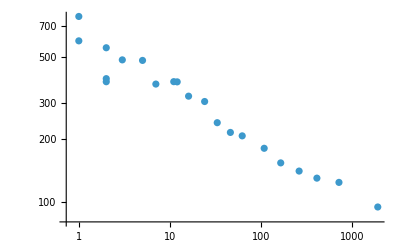

```mathematica
ListPlot[Table[{Length[#],Mean[#]}&@VertexList[gr,(v_/;boh[v]==w):>getpl[v]],{w,boh[1]}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
myfit=LinearModelFit[Table[{Log@Length[#],Log@Mean[#]}&@VertexList[gr,(v_/;boh[v]==w):>getpl[v]],{w,boh[1]-1}],x,x]
```

FittedModel[…]

```mathematica
r2[fit1]
```

0.964769

```mathematica
pcit[fit1]
```

| Estimate | Standard Error | Confidence Interval
1 | 6.51071 | 0.124514 | {6.22904,6.79238}
z | -0.192444 | 0.0122584 | {-0.220174,-0.164713}

```mathematica
{Exp[-0.22],Exp[-0.192],Exp[-0.165]}
```

{0.802519,0.825307,0.847894}

```mathematica
r2[fit2]
```

0.994909

```mathematica
pcit[fit2]
```

| Estimate | Standard Error | Confidence Interval
1 | 5.14742 | 0.0377835 | {5.06029,5.23454}
z | -0.174487 | 0.00441294 | {-0.184663,-0.164311}

```mathematica
{Exp[-0.1643],Exp[-0.1745],Exp[-0.1847]}
```

{0.848487,0.839877,0.831354}

```mathematica
(1 2 (20 10^-3))/(2 10^-5)
```

2000

```mathematica
(1000 (100 10^-6)(200 10^-6))/(1 10^-3)
```

1/50

```mathematica
{Exp[-0.1292],Exp[-0.1204],Exp[-0.1116]}
```

{0.878798,0.886566,0.894402}

```mathematica
fit1=LinearModelFit[{Range[2,branchorder[1]-1],Log[Mean/@lensord[[2;;]]]}ᵀ,n,n];
fit2=LinearModelFit[{Range[2,branchorder[1]-1],Log[Mean/@widsord[[2;;]]]}ᵀ,n,n]
```

```mathematica
Show[ListLogPlot[{Around[Mean[#],se[#]]&/@tiplensord,Around[Mean[#],se[#]]&/@tipwidsord},FrameLabel->{"Tip generation","μm"},PlotLegends->Placed[{"Tip length","Tip width"},{Right,Bottom}],PlotMarkers->"OpenMarkers",ImageSize->Medium,PlotRange->All,graphsettings](*,Plot[{fit1[n],fit2[n]},{n,2,branchorder[1]-1},PlotStyle->Dashed]*)]
```

```mathematica
lensord=Table[VertexList[gr,(v_/;branchorder[v]==z&&branchorder[v]<branchorder[getp[v]]):>getpl[v]],{z,branchorder[1]-1}];
widsord=Table[VertexList[gr,(v_/;branchorder[v]==z&&branchorder[v]<branchorder[getp[v]]):>getpw[v]],{z,branchorder[1]-1}];
```

```mathematica
Grid[{{
Show[ListPlot[Around[Mean[#],StandardDeviation[#]]&/@lensord,Frame->True,FrameLabel->{"Branch order","Length (μm)"},PlotMarkers->"■",PlotStyle->Black,LabelStyle->{Medium,Black},ImageSize->Medium,PlotRange->All,GridLines->Automatic]],Show[ListPlot[Around[Mean[#],StandardDeviation[#]]&/@widsord,Frame->True,PlotStyle->Black,FrameLabel->{"Branch order","Width (μm)"},PlotMarkers->"■",LabelStyle->{Medium,Black},ImageSize->Medium,PlotRange->All,GridLines->Automatic],Plot[Exp@fit[x-1],{x,2,9},PlotStyle->Dashed]]}}]
```

### Structure of tip morphologies

```mathematica
Module[
{sample=ends,nparts=3,quantiles,f=getpw},quantiles=Quantile[f/@sample,Subdivide[nparts]];
Grid[{Table[Histogram[Cases[{f[#],getpl[#]}&/@sample,(x_/;quantiles[[i]]<=x[[1]]<quantiles[[i+1]]):>x[[2]]],{Range[0,200,10]},Frame->True,FrameLabel->{"Length (μm)","Count"}],{i,nparts}]}]]
```

```mathematica
Module[
{sample=ends,nparts=3,quantiles,f=getpw},quantiles=Quantile[f/@sample,Subdivide[nparts]];
Histogram[Table[Cases[{f[#],getpl[#]}&/@sample,(x_/;quantiles[[i]]<=x[[1]]<quantiles[[i+1]]):>x[[2]]],{i,nparts}],{Range[0,200,10]}]]
```

```mathematica
Module[
{sample=ends2,nparts=3,quantiles,f=getpw},quantiles=Quantile[getpw/@sample,Subdivide[nparts]];
ListPlot[Table[{i,Around[Mean[#],StandardDeviation[#]]}&[Cases[{getpw[#],getpl[#]}&/@sample,(x_/;quantiles[[i]]<=x[[1]]<quantiles[[i+1]]):>x[[2]]]],{i,nparts}],PlotRange->All]]
```

```mathematica
Correlation[getpw/@ends2,getpl/@ends2]
```

```mathematica
Outer[Correlation[#1/@ends,#2/@ends]&,{getz,getpw,getpl},{getz,getpw,getpl}]//MatrixForm
```

```mathematica
Outer[Correlation[#1/@ends2,#2/@ends2]&,{getz,getpw,getpl},{getz,getpw,getpl}]//MatrixForm
```

```mathematica
Grid[{BoxWhiskerChart[Table[Cases[ends,(v_/;getz[v]==z):>#[v]],{z,Min[getz/@ends],Max[getz/@ends]}]]&/@{ltoroot,ltoroot[#]/getz[#]&}}]
```

```mathematica
(Correlation@@(Table[{getz[v],#[v]},{v,ends}]//Transpose))&/@{ltoroot,ltoroot[#]/getz[#]&}
```

```mathematica
LinearModelFit[Table[{getz[v],#[v]},{v,ends}],x,x]&/@{ltoroot,ltoroot[#]/getz[#]&}
```

### Fitting Hill function

```mathematica
tipdata=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips.csv"];
tipsrfdata=Cases[Transpose[tipdata],(i_/;ToExpression[i[[2]]]):>ToExpression[i[[3]]]];
tipblkdata=Cases[Transpose[tipdata],(i_/;Not@ToExpression[i[[2]]]):>ToExpression[i[[3]]]];
tip2data=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\full_lobes\\left_upper\\EH3549-P8.3\\tips2.csv"];
tip2srfdata=Cases[Transpose[tip2data],(i_/;ToExpression[i[[2]]]):>ToExpression[i[[3]]]];
tip2blkdata=Cases[Transpose[tip2data],(i_/;Not@ToExpression[i[[2]]]):>ToExpression[i[[3]]]];
```

```mathematica
Assuming[{xmax>0,xmed>0,xgr>0,y>0},Exp[-Integrate[μ[xmax,xmed,xgr,x],{x,0,y}]]]
```

e^(-y/xmax)((1+ⅇ^(xmed/xgr))/(1+ⅇ^(-(y-xmed)/xgr)))^(xgr/xmax)

```mathematica
dist=EmpiricalDistribution[tip2srfdata];
```

```mathematica
μ[xmax_,xmed_,xgr_,x_]:=1/xmax 1/(1+Exp[-(x-xmed)/xgr]);
(*mycdf[xmax_,xmed_,xgr_,x_]:=1-Exp[-Sum[μ[xmax,xmed,xgr,y],{y,x}]];*)
mycdf[xmax_,xmed_,xgr_,x_]:=1-Exp[-x/xmax]((1+Exp[xmed/xgr])/(1+Exp[-(x-xmed)/xgr]))^(xgr/xmax);
mypdf[xmax_,xmed_,xgr_,x_]:=mycdf[xmax,xmed,xgr,x+1/2]-mycdf[xmax,xmed,xgr,x-1/2];
mydata=Table[CDF[dist,x],{x,400}];
```

```mathematica
FindFit[mydata,mycdf[xmax,xmed,xgr,x],{{xmax,35},{xmed,85},{xgr,13}},x]
```

```mathematica
ListLinePlot[{mydata,Table[mycdf[45,95,15,x],{x,400}]},PlotStyle->{Automatic,Dashed}]
```

```mathematica
Show[Histogram[tip2srfdata,Automatic,"PDF"],ListLinePlot[Table[mypdf[33.3,82.3,13.8,x],{x,300}]]]
```

```mathematica
Histogram[tipsrfdata,Automatic,"PDF"]
```

```mathematica
Plot[Piecewise[{{0,x<0},{1/(2 2)(2-Exp[-x/1]),0<x<2},{1/(2 2)Exp[-x/1](Exp[2/1]-1),x>2}}],{x,0,5}]
```

```mathematica
s[xmax_,xmed_,xgr_,x_]:=Exp[-Sum[μ[xmax,xmed,xgr,y],{y,x}]];
mypdf2[xmax_,xmed_,xgr_,xdel_,xadd_,x_]:=If[x<xadd,
Sum[1/(2xadd)(2-Exp[-y/xdel])s[xmax,xmed,xgr,x-y],{y,x}],
Sum[1/(2xadd)(2-Exp[-y/xdel])s[xmax,xmed,xgr,x-y],{y,Floor[xadd]}]+Sum[1/(2xadd)Exp[-y/xdel](Exp[xadd/xdel]-1)s[xmax,xmed,xgr,x-y],{y,Ceiling[xadd],x}]];
```

```mathematica
norm=Sum[s[33.3,82.3,13.8,x],{x,400}];
Show[Histogram[tipsrfdata,Automatic,"PDF"],DiscretePlot[mypdf2[33.3,82.3,13.8,52.5,25.9,x]/norm,{x,400}]]
```

```mathematica
data=RandomChoice[tipsrfdata,10000]-RandomReal[1,10000]RandomChoice[tip2srfdata,10000];
Histogram[data]
```

```mathematica
Manipulate[Show[ListLinePlot[Table[PDF[dist,x]/(1-CDF[dist,x]),{x,0,200}]],Plot[1/L x^γ/(σ^γ+x^γ),{x,0,300},PlotStyle->Dashed]],{σ,50,150},{γ,2,15},{L,5,50}]
```

```mathematica
Manipulate[Show[ListLinePlot[Table[PDF[dist,x]/(1-CDF[dist,x]),{x,0,200}]],Plot[1/L 1/(1+Exp[-(x-x0)/xgr]),{x,0,300},PlotStyle->Dashed]],{x0,50,100},{xgr,5,20},{L,5,50}]
```

```mathematica
data=Cases[tip2srfdata,x_/;x>0];
dist=EstimatedDistribution[data,LogLogisticDistribution[γ,σ]]
Show[Histogram[data,Automatic,"PDF"],Plot[PDF[dist,x],{x,10,500},PlotRange->All]]
```

```mathematica
data=Cases[tip2blkdata,x_/;x>30];dist=EstimatedDistribution[data,LogLogisticDistribution[γ,σ]]
Show[Histogram[data,Automatic,"PDF"],Plot[PDF[dist,x],{x,0,300},PlotRange->All]]
```

```mathematica
Histogram[VertexList[gr,(v_/;boh[v]==2&&AllTrue[VertexOutComponent[tg,v,{1}],MemberQ[srftips,#]&]):>(Abs[getpl@First@#-getpl@Last@#]&@VertexOutComponent[tg,v,{1}])],Automatic,"PDF"]
```

```mathematica
FullSimplify[Assuming[{x1>0,x2>0},Convolve[Convolve[PDF[UniformDistribution[{0,x1}],x],PDF[UniformDistribution[{-x1,0}],x],x,y],PDF[ExponentialDistribution[1/x2],y],y,z]]]
```

```mathematica
myfun[xdel_,xadd_,x_]:=Piecewise[{{0,x<0},{xadd^(-2)(2 (xadd-x)+Exp[-(xadd+x)/xdel] (1-2 Exp[xadd/xdel]+Exp[(2x)/xdel]) xdel),x<=xadd},{xadd^(-2)Exp[-(xadd+x)/xdel] (-1+Exp[xadd/xdel])^2 xdel,x>xadd}}];
```

```mathematica
mydata=VertexList[gr,(v_/;boh[v]==2&&AllTrue[VertexOutComponent[tg,v,{1}],MemberQ[srftips,#]&]):>(Abs[getpl@First@#-getpl@Last@#]&@VertexOutComponent[tg,v,{1}])];
mycdf2=Table[CDF[EmpiricalDistribution[mydata],x],{x,300}];
FindFit[mycdf2,Sum[myfun[xdel,xadd,y],{y,x}],{{xdel,50},{xadd,1}},x]
```

```mathematica
ListPlot[{mycdf2,Table[Sum[myfun[52.5,25.9,y],{y,z}],{z,300}]}]
```

## Width ratios

Murray’s law
Suppose we have a mother branch with radius r_1 and two daughter branches with radii r_(2,3):
r_1-[r_2
r_3
Murray’s law states that a network that minimizes flow resistance for purely laminar flows satisfies:
r_1^3=r_2^3+r_3^3 
More generally, one has
r_1^α=r_2^α+r_3^α 
with an exponent 2<α<3. In purely diffusive transport, α=2 and in convective transport in a turbulent flow, α=7/3.

In lung airways, what is usually done is one assumes r_2=r_3, from which one obtains the relation between diameters in subsequent generations,
r_2/r_1=r_3/r_1=2^(-1/α)
where canonical measurements report α=3 in adult humans.

```mathematica
firsttwogens=Flatten[{1,AdjacencyList[gr,1]}];
widthtriples=VertexList[gr,(v_/;getz[v]>2&&VertexDegree[gr,v]==3&&branchorder[v]>2):>(getpw[#]&/@VertexOutComponent[tg,v,1])];
```

```mathematica
voltriples=VertexList[gr,(v_/;Not[MemberQ[firsttwogens,v]]&&Not[MemberQ[ends2,v]]&&VertexDegree[gr,v]==3&&getz[v]<=100):>(getpw[#]^2getpl[#]&/@VertexOutComponent[tg,v,1])];
```

Random tree Murray’s law model

```mathematica
mydist=UniformDistribution[{0.75,0.85}];
split[x_]:=Module[{r=RandomVariate[mydist]},x{r,(1-r^3)^(1/3)}];
```

```mathematica
tree=Graph[NestTree[split,1,8]];
```

```mathematica
ListPlot[Table[Mean[VertexList[tree,(v_/;GraphDistance[tree,{1,{}},v,Method->"UnitWeight"]==z):>First[v]]],{z,8}]]
```

```mathematica
Exp[LinearModelFit[Table[{z,Log@Mean[VertexList[tree,(v_/;GraphDistance[tree,{1,{}},v,Method->"UnitWeight"]==z):>First[v]]]},{z,8}],x,x]'[0]]
```

```mathematica
Histogram[Flatten[Array[split[1]&,900]]]
```

```mathematica
Mean[Flatten[Array[split[1]&,900]]]
```

### Plotting d_par^3 vs ∑d_i^3

```mathematica
Show[ListPlot[VertexList[gr,(v_/;getz[v]>1&&VertexDegree[gr,v]>1):>{getpw[v]^3,Total[getpw[#]^3&/@VertexOutComponent[tg,v,{1}]]}],ScalingFunctions->{"Log","Log"},PlotRange->All,AspectRatio->1],Plot[x,{x,0,1000000},PlotStyle->Dashed]]
```

### d_1/d_par vs d_2/d_par

```mathematica
Show[DensityHistogram[{(#[[2]])/(#[[1]]),(#[[3]])/(#[[1]])}&/@widthtriples,PlotRange->{{0,2.0},{0,2.0}},AspectRatio->1,ImageSize->122,FrameStyle->Black,PlotRangePadding->None,ColorFunction->ColorData[{"TemperatureMap",{0.5,-0.5}}],ChartLegends->Placed[BarLegend[{Automatic,{0,0.5}},LegendLabel->Placed["Probability",Left,Rotate[#,90°]&],LabelStyle->{Black,FontSize->6.4},LegendMarkerSize->50],{Right,Top}]],
Plot[(1-x^3)^(1/3),{x,0,1},PlotLegends->Placed[{"(d_1/d_0)^3+(d_2/d_0)^3=1"},{Left,Bottom}],PlotRange->{{0,1.5},{0,1.5}},PlotStyle->Black,LabelStyle->{Black,FontSize->4.8}],
LabelStyle->{FontSize->6.4,Black},FrameLabel->{"(Daughter 1)/parent diameter, d_1/d_0","(Daughter 2)/parent diameter, d_2/d_0"},Frame->True,GridLines->Automatic]
```

-Graphics-

### Numerically solving (d_1/d_par)^n+(d_2/d_par)^n=1

```mathematica
N[Count[widthtriples,(x_/;x[[2]]>x[[1]]||x[[3]]>x[[1]])]/Length[widthtriples]]
```

```mathematica
data=n/.Cases[widthtriples,(x_/;x[[2]]<x[[1]]&&x[[3]]<x[[1]]):>FindRoot[(x[[2]]/x[[1]])^n+(x[[3]]/x[[1]])^n-1,{n,3}]];
```

```mathematica
#[data]&/@{Median,GeometricMean,Mean}
```

```mathematica
Histogram[data]
```

### Fitting with (positive) generation

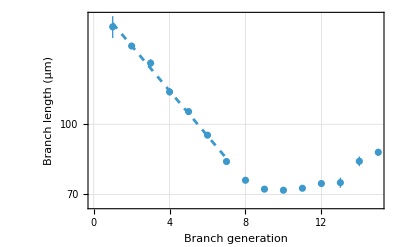

```mathematica
f=getpw;zmin=1;zmax=7;
fit=LinearModelFit[Table[{z,Log[Mean[VertexList[gr,(v_/;getz[v]==z&&NumberQ[f[v]]):>f[v]]]]},{z,zmin,zmax}],x,x];
Show[ListLogPlot[Table[Around[Mean[#],se[#]]&@VertexList[gr,(v_/;getz[v]==z&&NumberQ[f[v]]):>f[v]],{z,VertexEccentricity[tg,1]}]],
Plot[fit[x],{x,zmin,zmax},PlotStyle->Dashed(*,PlotLegends->Placed[{StringJoin["d∼x^z, x=",ToString[DecimalForm[Exp[fit'[0]],4] ]]},{Right,Top}]*)],
Frame->True,FrameLabel->{"Branch generation","Branch length (μm)"},GridLines->Automatic,LabelStyle->Medium]
```

```mathematica
fit["RSquared"]
```

```mathematica
fit["ParameterConfidenceIntervalTable"]
```

### Strahler order method

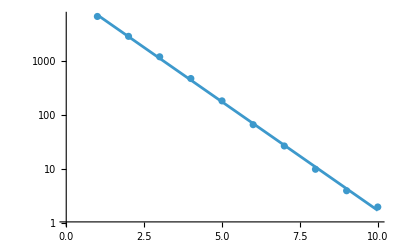

| Estimate | Standard Error | Confidence Interval
1 | 9.81423 | 0.0576251 | {9.68135,9.94711}
n | -0.926718 | 0.00928713 | {-0.948135,-0.905302}

```mathematica
nodes=VertexList[gr,v_/;branchorder[v]<branchorder[getp[v]]];
nmin=1;nmax=branchorder[1]-1;
data=Table[{n,Count[nodes,v_/;branchorder[v]==n]},{n,nmin,nmax}];
fit=LinearModelFit[Table[{i[[1]],Log@i[[2]]},{i,data}],n,n];
Show[ListLogPlot[data],Plot[fit[n],{n,nmin,nmax}]]
pcit[fit]
```

```mathematica
Exp@({-0.948,-0.927,-0.905}/3)
```

{0.729059,0.734181,0.739585}

```mathematica
Exp[0.9267]
```

2.52616

```mathematica
wdata=Table[Around[Mean[#],se[#]]&@Cases[nodes,(v_/;branchorder[v]==n):>getpw[v]],{n,nmin,nmax}];
fitw=LinearModelFit[Table[{n,Log@wdata[[n]]},{n,2,10}],n,n];
pcit[fitw]
```

| Estimate | Standard Error | Confidence Interval
1 | 3.72495 | 0.017785 | {3.6829,3.76701}
n | 0.175596 | 0.00626667 | {0.160778,0.190414}

```mathematica
r2[fitw]
```

0.991163

```mathematica
Exp@{-0.151,-0.168,-0.185}
```

{0.859848,0.845354,0.831104}

```mathematica
ldata=Table[Around[Mean[#],se[#]]&@VertexList[gr,(v_/;branchorder[v]==n):>getpl[v]],{n,nmin,nmax}];
fitl=LinearModelFit[Table[{n,Log@ldata[[n]]},{n,2,10}],n,n];
pcit[fitl]
```

| Estimate | Standard Error | Confidence Interval
1 | 3.79305 | 0.0285831 | {3.72547,3.86064}
n | 0.261301 | 0.010353 | {0.23682,0.285782}

```mathematica
r2[fitl]
```

0.989131

```mathematica
Exp@{-0.243,-0.282,-0.322}
```

{0.784272,0.754274,0.724698}

```mathematica
Show[ListPlot[{ldata,wdata},Frame->True,FrameStyle->Black,AspectRatio->1,GridLines->Automatic,LabelStyle->{Black,FontSize->6.4},PlotMarkers->{"OpenMarkers",3},PlotLegends->Placed[{"Branch length","Branch diameter"},{Left,Top}],ImageSize->125,PlotRange->{{0,12},{0,1000}},FrameLabel->{"Branch order, w","Branch length, diameter (μm)"}],ListLinePlot[{Table[{n,Exp@fitl["BestFitAround"]},{n,2,10,0.1}],Table[{n,Exp@fitw["BestFitAround"]},{n,2,10,0.1}]},IntervalMarkers->"Bands"]]
```

-Graphics-

```mathematica
{r2[fitl],r2[fitw]}
```

{0.989868,0.994999}

```mathematica
nodes=VertexList[gr,v_/;branchorder[v]<branchorder[getp[v]]];
nmin=1;nmax=branchorder[1]-1;
data=Table[{Log@Length[#],Log@Mean[getpw/@#]}&@Cases[nodes,v_/;branchorder[v]==n],{n,nmin,nmax}];
fitnw=LinearModelFit[data[[2;;-2]],n,n];
#[fitnw]&/@{r2,pcit}
```

{0.979302, | Estimate | Standard Error | Confidence Interval
1 | 5.34769 | 0.0464938 | {5.23392,5.46145}
n | -0.151061 | 0.00896577 | {-0.173,-0.129123}}

```mathematica
Show[ListPlot[Table[{Length[#],Around[Mean[getpw/@#],StandardDeviation[getpw/@#]]}&@Cases[nodes,v_/;branchorder[v]==n],{n,nmin,nmax}],ScalingFunctions->{"Log10","Log10"},FrameLabel->{"Number of branches, n_w","Mean external diameter (μm)"},ImageSize->122,PlotMarkers->{"OpenMarkers",3},
graphsettings,PlotRange->{{1,10^4},{20,500}}],ListLinePlot[Table[{m,Exp@(bfa[fitnw]/.{n->Log[m]})},{m,Exp@data[[-2,1]],Exp@data[[2,1]],10}],IntervalMarkers->"Bands",ScalingFunctions->{"Log10","Log10"},PlotRange->All]]
fitnw["ParameterConfidenceIntervalTable"]
-1/fitnw'[0]
```

-Graphics-

| Estimate | Standard Error | Confidence Interval
1 | 5.34769 | 0.0464938 | {5.23392,5.46145}
n | -0.151061 | 0.00896577 | {-0.173,-0.129123}

6.61983

```mathematica
r2[fitnw]
```

0.979302

{3.57143,5.02513}

```mathematica
data=Table[{Log@Length@Cases[nodes,v_/;branchorder[v]==n],Log@Mean[getpl/@VertexList[gr,v_/;branchorder[v]==n]]},{n,branchorder[1]-1}];
fitnl=LinearModelFit[data[[1;;-1]],n,n];
#[fitnl]&/@{r2,pcit}
```

{0.989373, | Estimate | Standard Error | Confidence Interval
1 | 6.60547 | 0.0628882 | {6.44381,6.76713}
n | -0.274892 | 0.0127411 | {-0.307643,-0.24214}}

```mathematica
Show[ListPlot[Table[{Length@Cases[nodes,v_/;branchorder[v]==n],Around[Mean[getpl/@VertexList[gr,v_/;branchorder[v]==n]],StandardDeviation[getpl/@VertexList[gr,v_/;branchorder[v]==n]]]},{n,branchorder[1]-1}],ScalingFunctions->{"Log10","Log10"},FrameLabel->{"Number of branches, n_w","Mean branch length (μm)"},ImageSize->122,PlotMarkers->{"OpenMarkers",3},
graphsettings,PlotRange->{{1,10^4},{10,1000}}],ListLinePlot[Table[{m,Exp@(bfa[fitnl]/.{n->Log[m]})},{m,Exp@data[[-1,1]],Exp@data[[1,1]],10}],IntervalMarkers->"Bands",ScalingFunctions->{"Log10","Log10"},PlotRange->All]]
pcit@fitnl
-1/fitnl'[0]
```

-Graphics-

| Estimate | Standard Error | Confidence Interval
1 | 6.59213 | 0.0585909 | {6.45702,6.72725}
n | -0.277814 | 0.0108162 | {-0.302756,-0.252872}

3.59953

```mathematica
{1/0.3028,1/0.2529}
```

{3.30251,3.95413}

```mathematica
r2[fitnl]
```

0.988019

```mathematica
Histogram[VertexList[gr,(v_/;getz[v]>1&&branchorder[v]>2):>getpl[v]/getpw[v]],Automatic,"PDF",Frame->True,AspectRatio->1,FrameLabel->{"(Branch length)/(lumen diameter)","Probability distribution"},GridLines->Automatic,PlotRange->{{0,8},{0,0.5}},LabelStyle->{Black,FontSize->6.4},ImageSize->117,FrameStyle->Black,PlotRangePadding->None]
```

-Graphics-

```mathematica
Median[VertexList[gr,(v_/;getz[v]>1&&branchorder[v]>2):>getpl[v]/getpw[v]]]
```

3.44645

```mathematica
{Mean[#],StandardDeviation[#]}&[VertexList[gr,(v_/;getz[v]>1&&branchorder[v]>2):>getpl[v]/getpw[v]]]
```

### Horsfield order method

```mathematica
fitn=LinearModelFit[Table[{z,Log@VertexCount[gr,v_/;boh[v]==z]},{z,boh[1]-3}],x,x]
```

```mathematica
Exp[-fitn'[0]]
```

```mathematica
Show[ListPlot[Table[{z,VertexCount[gr,v_/;boh[v]==z]},{z,boh[1]}],ScalingFunctions->"Log",Frame->True,FrameLabel->{"Branch order","Branch count"},
LabelStyle->Medium,GridLines->Automatic],Plot[fitn[n],{n,1,boh[1]-3},PlotStyle->Dashed]]
```

```mathematica
f=getpl;
```

```mathematica
fitw=LinearModelFit[Table[{z,Log@Mean[VertexList[gr,(v_/;boh[v]==z):>f[v]]]},{z,2,boh[1]-1}],x,x]
```

```mathematica
Show[ListPlot[Table[{z,Around[Mean[#],se[#]]}&[VertexList[gr,(v_/;boh[v]==z):>f[v]]],{z,boh[1]}],
ScalingFunctions->"Log",Frame->True,FrameLabel->{"Branch order","Branch diameter (μm)"},
LabelStyle->Medium,GridLines->Automatic],Plot[fitw[n],{n,2,boh[1]-1},PlotStyle->Dashed]]
```

```mathematica
fitw["ParameterConfidenceIntervalTable"]
```

```mathematica
fitn["ParameterConfidenceIntervalTable"]
```

```mathematica
fitnw=LinearModelFit[Table[{Log@Length[#],Log@Mean[f/@#]}&@VertexList[gr,v_/;boh[v]==n],{n,2,boh[1]-3}],n,n]
```

```mathematica
Show[ListPlot[Table[{Length[#],Mean[f/@#]}&@VertexList[gr,v_/;boh[v]==n],{n,1,boh[1]-1}],
ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"Branch count","Branch diameter (μm)"},
LabelStyle->Medium,GridLines->Automatic,AspectRatio->1],Plot[fitnw[n],{n,Log[2],fitn[2]},PlotStyle->Dashed]]
```

```mathematica
fitnw["ParameterConfidenceIntervalTable"]
```

```mathematica
-1/fitnw'[0]
```

### Other approach

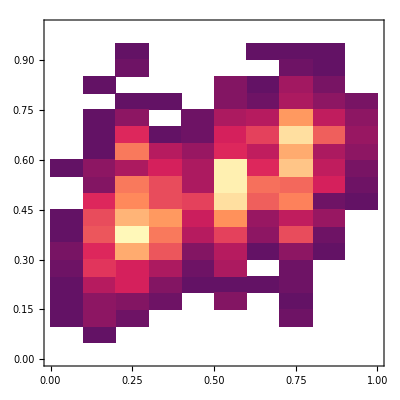

```mathematica
DensityHistogram[Table[Module[{vs=VertexOutComponent[tg,v,{1}]},
If[Length[vs]==2,
{Length[VertexOutComponent[tg,vs[[2]]]]/(Length[VertexOutComponent[tg,vs[[1]]]]+Length[VertexOutComponent[tg,vs[[2]]]]),getpw[vs[[2]]]^3/(getpw[vs[[1]]]^3+getpw[vs[[2]]]^3)}]],{v,VertexList[gr,v_/;boh[v]>2]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

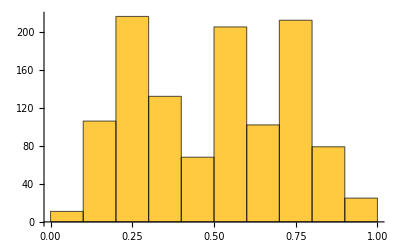

```mathematica
Histogram[DeleteCases[Table[Module[{vs=VertexOutComponent[tg,v,{1}]},
If[Length[vs]==2,Length[VertexOutComponent[tg,vs[[2]]]]/(Length[VertexOutComponent[tg,vs[[1]]]]+Length[VertexOutComponent[tg,vs[[2]]]])]],{v,VertexList[gr,v_/;boh[v]>2]}],Null]]
```

## Summary stats (one sample)

```mathematica
tiplens2=Flatten[Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\archive\\left_upper_lobes\\EH3685-LU-P8.9(P8.7)\\prune_10um\\tiplens2.csv"]];
```

```mathematica
path="C:\\Users\\ivanl\\OneDrive - University of Cambridge\\lung_exp_data\\archive\\left_upper_lobes\\EH3685-LU-P8.9(P8.7)\\prune_10um\\";
tiplens=Flatten[Import[StringJoin[path,"tiplens.csv"]]];
tipwids=Flatten[Import[StringJoin[path,"tipwids.csv"]]];
tiplens2=Flatten[Import[StringJoin[path,"tiplens2.csv"]]];
tipwids2=Flatten[Import[StringJoin[path,"tipwids2.csv"]]];
```

```mathematica
tiplens=getpl/@ends;
tipwids=getpw/@ends;
tiplens2=getpl/@ends2;
tipwids2=getpw/@ends2;
```

```mathematica
{{Length[tiplens],Mean[tiplens],StandardDeviation[tiplens],se[tiplens],Median[tiplens],ArgMax[PDF[SmoothKernelDistribution[tiplens],x],x]},{Mean[tipwids],StandardDeviation[tipwids],se[tipwids],Mean[tiplens2],StandardDeviation[tiplens2],se[tiplens2],ArgMax[PDF[SmoothKernelDistribution[tiplens2],x],x]},{Mean[Cases[tipwids2,_?NumberQ]],StandardDeviation[Cases[tipwids2,_?NumberQ]],se[Cases[tipwids2,_?NumberQ]]}}
```

### Combining samples

```mathematica
Histogram[{tip3547,tip3822,tip4413},Automatic,"PDF",PlotRange->All,
ChartLegends->Placed[{"EH3547 (PCW 8.7)","EH3822 (PCW 10.2)","EH4413 (PCW 11.6)"},{Right,Top}],
Frame->True,FrameLabel->{"Length (μm)","Probability"}]
```

```mathematica
Histogram[#/Mean[#]&/@{tip3547,tip3822,tip4413},Automatic,"PDF",PlotRange->All,
ChartLegends->Placed[{"EH3547 (PCW 8.7)","EH3822 (PCW 10.2)","EH4413 (PCW 11.6)"},{Right,Top}],
Frame->True,FrameLabel->{"Rescaled length (dimensionless)","Probability"}]
```

### Individual sample

```mathematica
data=Table[{i,CDF[EmpiricalDistribution[tiplens2],i]},{i,10,300}];
NonlinearModelFit[data,1-((1+Exp[-m/k])/(1+Exp[(x-m)/k]))^(k/L),{{L,30},{k,10},{m,100}},x]["ParameterTable"]
```

```mathematica
Module[{L=54.4,k=8.4,m=77.8},
Show[Histogram[tiplens2,25,"PDF"],DiscretePlot[1/(L(1+Exp[-(x-m)/k]))((1+Exp[-m/k])/(1+Exp[(x-m)/k]))^(k/L),{x,300}]]]
```

```mathematica
data=Table[{i,CDF[EmpiricalDistribution[tiplens],i]},{i,10,300}];
NonlinearModelFit[data,If[x<m,1/m(x-L+L Exp[-x/L]),-L/m(1-Exp[-m/L])Exp[-(x-m)/L]+1],{{m,90},{L,40}},x]["ParameterTable"]
```

```mathematica
Module[{L=58.4,m=22.8},
Show[Histogram[tiplens,Automatic,"PDF"],DiscretePlot[1/m(1-Exp[-m/L])Exp[-(x-m)/L],{x,m,350}],DiscretePlot[1/m(1-Exp[-x/L]),{x,0,m}]]]
```

```mathematica
x1=100;x2=380;
lens=tiplens;wids=tipwids2;
(*data=Cases[Range[Length[lens]],(i_/;lens[[i]]>wids[[i]]):>lens[[i]]];*)
data=lens;
emp1[x_]:=1-CDF[EmpiricalDistribution[data],x];
fit1=LinearModelFit[Table[{i,Log[emp1[i]]},{i,x1,x2,2}],x,x];
Show[
DiscretePlot[emp1[x],{x,0,500,1},ScalingFunctions->"Log",PlotRange->Full],
Plot[fit1[x],{x,x1,x2},PlotRange->All,PlotStyle->Orange]]
1/(fit1[0]-fit1[1])
```

```mathematica
x1=60;x2=100;
emp1[x_]:=CDF[EmpiricalDistribution[tiplens2],x];
fit1=LinearModelFit[Table[{i,Log[emp1[i]]},{i,x1,x2,2}],x,x];
Show[
DiscretePlot[emp1[x],{x,10,150},ScalingFunctions->"Log"],
Plot[fit1[x],{x,x1,x2},PlotRange->All,PlotStyle->Orange]]
1/(fit1[1]-fit1[0])
```

```mathematica
Histogram[{tiplens2,tiplens},Automatic,"PDF",Frame->True,FrameLabel->{"Length (μm)","Probability"},ChartLegends->Placed[{"Second Segments","Tips"},{Right,Top}],ScalingFunctions->"Linear"]
```

```mathematica
SmoothHistogram[{Cases[Transpose[{tiplens,tipwids}],(t_/;t[[1]]>t[[2]]):>t[[1]]],Cases[Transpose[{tiplens2,tipwids2}],(t_/;t[[1]]>t[[2]]):>t[[1]]],tipwids,tipwids2},
ScalingFunctions->"Linear",PlotRange->{{0,400},Automatic},PlotLegends->{"Lengths 1","Lengths 2","Widths 1","Widths 2"}]
```

```mathematica
ListPlot[{Transpose[{tiplens,tipwids}],Transpose[{tiplens2,tipwids2}]}]
```

```mathematica
DiscretePlot[1-CDF[EmpiricalDistribution[tiplens],x],{x,0,200},ScalingFunctions->"Log"]
```

```mathematica
Histogram[{Cases[Transpose[{tiplens,tipwids}],(t_/;t[[1]]>t[[2]]):>t[[1]]],Cases[Transpose[{tiplens2,tipwids2}],(t_/;t[[1]]>t[[2]]):>t[[1]]]},Automatic,"PDF"]
```

```mathematica
Graph[#,VertexCoordinates->(xyz[[#]]&/@VertexList[#])]&[HighlightGraph[gr,NeighborhoodGraph[gr,#]&/@Cases[ends2,v_/;getpl[v]>120]]]
```

## Summary stats (all samples)

```mathematica
sheet=Import["C:\\Users\\ivanl\\OneDrive - University of Cambridge\\Spreadsheets\\tip_stats.xlsx"][[3]];
imax=21;
ages=sheet[[4]][[2;;imax]];
ntips=sheet[[5]][[2;;imax]];
tip1m=sheet[[6]][[2;;imax]];
tip1std=sheet[[7]][[2;;imax]];
tip1se=sheet[[8]][[2;;imax]];
tip1med=sheet[[9]][[2;;imax]];
tip1mod=sheet[[10]][[2;;imax]];
tip1rt=sheet[[11]][[2;;imax]];
tip1w=sheet[[12]][[2;;imax]];
tip1wstd=sheet[[13]][[2;;imax]];
tip1wse=sheet[[14]][[2;;imax]];
tip2m=sheet[[15]][[2;;imax]];
tip2std=sheet[[16]][[2;;imax]];
tip2se=sheet[[17]][[2;;imax]];
tip2mod=sheet[[18]][[2;;imax]];
tip2rt=sheet[[19]][[2;;imax]];
tip2lt=sheet[[20]][[2;;imax]];
tip2w=sheet[[21]][[2;;imax]];
tip2wstd=sheet[[22]][[2;;imax]];
tip2wse=sheet[[23]][[2;;imax]];
```

```mathematica
ListPlot[Transpose[{ages,Exp[-tip1w/tip1rt]}]]
```

```mathematica
Show[ListLogPlot[{ages,ntips}ᵀ,PlotMarkers->"OpenMarkers",AxesLabel->{"Age (PCW)","No. of tips (log scale)"},LabelStyle->Medium],
Plot[fit[x],{x,0,20},PlotStyle->Dashed,PlotLegends->Placed[{"Doubling period ∼0.56 weeks."},{Left,Top}]]]
```

```mathematica
Show[ListPlot[{Table[{ages[[i]],tip1m[[i]]}ᵀ,{i,3,19}],Table[{ages[[i]],tip1w[[i]]}ᵀ,{i,3,19}]},PlotLegends->Placed[{"Length","Width"},{Right,Top}],PlotMarkers->"OpenMarkers",LabelStyle->{Large,Black}],
Plot[Evaluate[Exp/@{fit[x],fit2[x]}],{x,6.7,12},PlotStyle->Dashed],FrameLabel->{"Age (PCW)","μm"},Frame->True,GridLines->Automatic,AspectRatio->1]
```

```mathematica
Show[ListPlot[Table[{ages[[i]]-0.54,tip2m[[i]]/0.54}ᵀ,{i,1,19}],PlotMarkers->"OpenMarkers",FrameLabel->{"Age (PCW)","Elongation rate (μm/week)"},LabelStyle->Medium,Frame->True,GridLines->Automatic],Plot[fit2'[0]/Log[2] Exp[fit2[x]-fit[x]],{x,5,12},PlotStyle->Dashed]]
```

```mathematica
fit=LinearModelFit[{ages[[6;;19]],Log[tip1m[[6;;19]]]}ᵀ,x,x];
fit2=LinearModelFit[{ages[[6;;19]],Log[tip1w[[6;;19]]]}ᵀ,x,x];
```

```mathematica
fit2["RSquared"]
```

```mathematica
Show[ListLogPlot[Transpose[{Around[ages,0.167],ntips}]],LogPlot[Exp[fit[x]],{x,6,12},PlotStyle->Dashed]]
```

```mathematica
nmin=3;nmax=20;
fit=LinearModelFit[Table[{ages[[i]],tip1w[[i]]},{i,nmin,nmax}],x,x];Show[ListPlot[{ages[[nmin;;nmax]],tip1w[[nmin;;nmax]]}ᵀ,PlotMarkers->"OpenMarkers"],Plot[fit[x],{x,ages[[nmin]],ages[[nmax]]},PlotStyle->Dashed,PlotLegends->Placed[{StringJoin[ToString[fit[x]]," , R^2=",ToString@NumberForm[fit["RSquared"],3]]},{Right,Top}]],
Frame->True,FrameLabel->{"Age (PCW)","Mean tip diameter (μm)"},LabelStyle->Medium,GridLines->Automatic]
```

```mathematica
nmin=3;nmax=20;
fit=LinearModelFit[Table[{ages[[i]],tip2w[[i]]},{i,nmin,nmax}],x,x];Show[ListPlot[{ages[[nmin;;nmax]],tip2w[[nmin;;nmax]]}ᵀ,PlotMarkers->"OpenMarkers"],Plot[fit[x],{x,ages[[nmin]],ages[[nmax]]},PlotStyle->Dashed,PlotLegends->Placed[{StringJoin[ToString[fit[x]]," , R^2=",ToString@NumberForm[fit["RSquared"],3]]},{Right,Top}]],
Frame->True,FrameLabel->{"Age (PCW)","Mean branch diameter (μm)"},LabelStyle->Medium,GridLines->Automatic]
```

```mathematica
fit["ParameterConfidenceIntervalTable"]
```

```mathematica
NumberForm[fit["RSquared"],3]
```

## Angles

## Unified

```mathematica
nodes=VertexList[gr,v_/;(VertexDegree[gr,v]==3&&getz[v]>1)];
daughters=VertexOutComponent[tg,#,{1}]&/@nodes;
parents=getp/@nodes;
v1v2=Table[Normalize[xyz[[#]]-xyz[[nodes[[i]]]]]&/@daughters[[i]],{i,Length[nodes]}];
normals=Normalize/@(Cross@@@v1v2);
pointers=Normalize/@(Plus@@@v1v2);
parpointers=Normalize/@Table[xyz[[nodes[[i]]]]-xyz[[parents[[i]]]],{i,Length[nodes]}];
nodes2=Cases[nodes,v_/;MemberQ[nodes,parents[[First@@Position[nodes,v]]]]];
```

```mathematica
ancalign[v_]:=ArcCos[Normalize[xyz[[v]]-xyz[[getp[v]]]].Normalize[xyz[[getp[v]]]-xyz[[getp[getp[v]]]]]];
```

```mathematica
Histogram[°^-1 ArcCos[Dot@@@v1v2],Automatic(*,Ticks->{{0,π/6,π/4,π/3,π/2,2π/3,π},Automatic}*)
(*,PlotLabel->{#[Re@ArcCos[Dot@@@DeleteCases[v1v2,{}]]]&/@{Mean,StandardDeviation,Skewness}}*)
,(*PlotLabel->"EH3822 (P10.2) B 1 & 2",*)AxesLabel->{"Bifurcation angle (°)","Frequency"}]
```

Horsfield/Murray angle law

```mathematica
Show[DensityHistogram[VertexList[gr,(v_/;VertexDegree[gr,v]==3&&Not[v==1]&&getz[v]<100):>({Sin[ancalign[#[[2]]]]/Sin[ancalign[#[[1]]]],(getpw[#[[1]]]/getpw[#[[2]]])^2}&[VertexOutComponent[tg,v,{1}]])],PlotRange->{{0,5},{0,5}}],Plot[x,{x,0,5}]]
```

```mathematica
ListPlot[Table[180/π ArcCos[parpointers[[i]].#]&/@v1v2[[i]],{i,Length[nodes]}],PlotRange->All,GridLines->Automatic]
```

```mathematica
stubbies=Cases[Range[Length[nodes]],i_/;AnyTrue[180/π ArcCos[parpointers[[i]].#]&/@v1v2[[i]],#<30&]&&AnyTrue[180/π ArcCos[parpointers[[i]].#]&/@v1v2[[i]],#>60&]:>nodes[[i]]];
```

```mathematica
Histogram[{getz/@stubbies,getz/@nodes},Automatic,"PDF"]
```

```mathematica
ListPlot[Table[{getz[nodes[[i]]],(parpointers[[i]].(v1v2[[i]][[1]]-v1v2[[i]][[2]]))^2},{i,Length[nodes]}]]
```

## Alignment with radius vector

```mathematica
BoxWhiskerChart[Table[Cases[srftips,(v_/;getz[v]==z):>°^-1 ArcCos[align[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-x0]]],{z,2,VertexEccentricity[gr,1]}],PlotRange->All]
```

```mathematica
BoxWhiskerChart[Table[Cases[blktips,(v_/;getz[v]==z):>°^-1 ArcCos[align[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-x0]]],{z,2,VertexEccentricity[gr,1]}],PlotRange->All]
```

```mathematica
Show[Histogram[°^-1 ArcCos[align[xyz[[#]]-xyz[[getp[#]]],xyz[[getp[#]]]-x0]]&/@#&/@{srftips,blktips},Automatic,"PDF",ChartStyle->{Red,Blue},GridLines->{Range[0,180,30],Automatic},graphsettings,ImageSize->125,PlotRange->{{0,180},{0,0.02}},PlotRangePadding->None,FrameTicks->{{Automatic,None}, {Range[0,180,30],None}},FrameLabel->{"Alignment with radial direction (°)","Probability distribution"},ChartLegends->Placed[{"Surface tips","Bulk tips"},{Right,Top}]],Plot[°/2 Sin[x °],{x,0,180},PlotStyle->Black,LabelStyle->{Black,FontSize->6.4},PlotLegends->Placed[{"Unbiased"},{Right,Top}]]]
```

-Graphics-

## Bifurcation in surface vs bulk

```mathematica
angle[u_,v_]:=ArcCos[(u.v)/(Norm[u]Norm[v])];
```

```mathematica
skelalign=VertexList[skeleton,(v_/;getz[v]>2&&boh[v]>1):>angle[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp[getp[v]]]]]];
skelntalign=VertexList[skeletont,(v_/;getz[v]>2&&boh[v]>1):>angle[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp[getp[v]]]]]];
```

```mathematica
Histogram[{skelalign,skelntalign}/Degree,Automatic,"PDF",ChartStyle->{Red,Blue},GridLines->{Range[0,180,30],Automatic},graphsettings,ImageSize->125,PlotRange->{{0,180},{0,0.03}},PlotRangePadding->None,FrameTicks->{{Automatic,None}, {Range[0,180,30],None}},FrameLabel->{"Alignment with parent (°)","Probability distribution"},ChartLegends->Placed[{"CN","AS"},{Right,Top}]]
```

-Graphics-

```mathematica
Around[Mean[#],se[#]]&[skelalign]/Degree
```

46.50.8

```mathematica
Around[Mean[#],se[#]]&[skelntalign]/Degree
```

71.21.0

```mathematica
Around[Mean[#],se[#]]&[Cos[skelalign]]
```

0.6420.010

```mathematica
Around[Mean[#],se[#]]&[Cos[skelntalign]]
```

0.3100.016

```mathematica
skeletonQ=MemberQ[VertexList[skeleton],#]&;
```

```mathematica
skelangles=DeleteCases[Table[Module[{u=VertexOutComponent[tg,v,{1}]},
If[Length[u]==2,
If[AllTrue[u,skeletonQ],
angle[xyz[[u[[1]]]]-xyz[[v]],xyz[[u[[2]]]]-xyz[[v]]]]]],
{v,VertexList[skeleton,u_/;boh[u]>2]}],Null];
```

```mathematica
skelntangles=DeleteCases[Table[Module[{u=VertexOutComponent[tg,v,{1}]},
If[Length[u]==2,
If[AllTrue[u,Not[skeletonQ[#]]&],
angle[xyz[[u[[1]]]]-xyz[[v]],xyz[[u[[2]]]]-xyz[[v]]]]]],
{v,VertexList[skeletont,u_/;boh[u]>2]}],Null];
```

```mathematica
Histogram[{skelangles,skelntangles}/Degree,Automatic,"PDF",ChartStyle->{Red,Blue},GridLines->{Range[0,180,30],Automatic},graphsettings,ImageSize->125,PlotRange->{{0,180},{0,0.03}},PlotRangePadding->None,FrameTicks->{{Automatic,None}, {Range[0,180,30],None}},FrameLabel->{"Bifurcation angle (°)","Probability distribution"},ChartLegends->Placed[{"CN","AS"},{Left,Top}]]
```

-Graphics-

```mathematica
FindRoot[√(Tan[π/γ]/(π/γ)-1)-0.372,{γ,5.5}]
```

{γ→5.26575}

```mathematica
√(Tan[π/γ]/(π/γ)-1)/.{γ->5.27}
```

0.37165

```mathematica
Around[Mean[#],se[#]]&[skelangles]/Degree
```

99.31.5

```mathematica
Around[Mean[#],se[#]]&[skelntangles]/Degree
```

128.61.3

```mathematica
Histogram[
{VertexList[skeleton,(v_/;getz[v]>2&&boh[v]>1):>angle[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp[getp[v]]]]]/Degree],
VertexList[skeletont,(v_/;getz[v]>2&&boh[v]>1):>angle[xyz[[v]]-xyz[[getp[v]]],xyz[[getp[v]]]-xyz[[getp[getp[v]]]]]/Degree]},Automatic,"PDF",ChartStyle->{Red,Blue},GridLines->{Range[0,180,30],Automatic},graphsettings,ImageSize->125,PlotRange->{{0,180},{0,0.03}},PlotRangePadding->None,FrameTicks->{{Automatic,None}, {Range[0,180,30],None}},FrameLabel->{"Alignment with parent (°)","Probability distribution"},ChartLegends->Placed[{"CN","AS"},{Right,Top}]]
```

## Alignment of first few gen’s vs age

```mathematica
ages={6.9,7.6,8,8,8.3,8.3,8.3,8.3,8.7,8.7,8.7,9,9.4,9.4,9.7,9.7,9.7,9.9,10.2,11.1,11.1,11.6,12};
z2={45.3,40.1,60.2,35.5,33.7,61.2,30.1,58.5,37.2,34.5,45.9,48.1,37.1,40.2,36.6,31.6,41.9,51.5,43.5,31.7,57.4,66.7,34};
z3={38.2,35,26.6,34.3,35.6,29.5,23.6,34.1,36.5,30.7,28.6,33.3,27,32.8,29.8,31.7,28.3,30.1,32,32.1,32,28.3,27.9};
z4={42.4,39.1,32,42.7,40.4,28.5,32.9,38.6,31,34.3,34.5,31.2,29.6,29.7,33.8,33.6,29,36.8,34.6,31.7,29,33.3,28.4};
z5={51.7,50.4,42,45,51.7,39.7,41.3,45.8,38.1,44.3,42.6,42.2,37.5,33.6,41.9,41.2,37.7,38.4,36.7,34.2,32.8,36.4,35.5};
z6={52.7,55.5,51.8,56.3,54.8,51.8,53.1,50.8,46.1,52.6,49.5,46.4,49.3,39.9,47.1,43.8,43,43.6,41.7,42.6,37.7,43.8,43.1};
```

```mathematica
data={ages,z6}ᵀ;
fit=LinearModelFit[data,x,x];
Show[ListPlot[data,Frame->True,PlotMarkers->{"OpenMarkers"},GridLines->Automatic,AspectRatio->1,LabelStyle->{Black,FontSize->20},FrameLabel->{"Age (PCW)","Mean alignment at z = 6 (°)"}],Plot[fit[x],{x,Min[ages],Max[ages]},PlotStyle->Dashed]]
{fit["RSquared"],fit'[0]}
```

## Method 3 (simple angles)

```mathematica
n0n1={};n0a={};pn1={};pa={};bn1={};ba={};
Do[
If[MemberQ[nodes,parents[[i]]],
Module[
{n0=Flatten@normals[[Flatten@Position[nodes,parents[[i]]]]],n1=normals[[i]],
a=pointers[[i]],p=parpointers[[i]],b},
b=Cross[n0,p];
{#1[n0n1,#2[n0.n1]],#1[n0a,#2[n0.a]],#1[pn1,#2[p.n1]],
#1[pa,#2[p.a]],#1[bn1,#2[b.n1]],#1[ba,#2[b.a]]}&[AppendTo,#&];
]]
,{i,Length[nodes]}];
```

```mathematica
Show[Histogram[ArcCos[pa]/Degree,{Range[0,180,5]},"PDF",Frame->True,FrameLabel->{"Angle between p and a (°)","Frequency"},LabelStyle->Medium],Plot[°/2 Sin[x °],{x,0,180},PlotStyle->Dashed]]
```

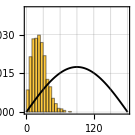

```mathematica
Show[Histogram[ArcCos[pa]/Degree,{Range[0,180,5]},"PDF",PlotRange->{{0,180},{0,0.04}},PlotRangePadding->None,ImageSize->135,FrameTicks->{{Automatic,None}, {Range[0,180,30],None}},GridLines->{Range[0,180,30],Automatic},FrameLabel->{"Alignment of branching direction, θ(p,a) (°)","Frequency"},graphsettings],Plot[° Sin[x °],{x,0,180},PlotLegends->Placed[{"Unbiased"},{Right,Top}],LabelStyle->{Black,FontSize->6.4},PlotStyle->Directive[Black,Thickness[0.01]]]]
```

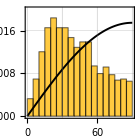

```mathematica
Show[Histogram[90-Abs[ArcCos[bn1]/Degree-90],{Range[0,90,5]},"PDF",PlotRange->{{0,90},{0,0.02}},PlotRangePadding->None,ImageSize->140,FrameLabel->{"Alignment with orthogonal mode, θ(b,n_2) (°)","Probability distribution"},FrameTicks->{{Automatic,None}, {Range[0,90,30],None}},GridLines->{Range[0,90,30],Automatic},graphsettings],Plot[° Sin[x °],{x,0,90},PlotLegends->Placed[{"Unbiased"},{Right,Bottom}],LabelStyle->{Black,FontSize->6.4},PlotStyle->Directive[Black,Thickness[0.01]]]]
```

```mathematica
Show[Histogram[90-Abs[90-ArcCos[n0n1]/Degree],{Range[0,90,5]},"PDF",Frame->True,FrameLabel->{"Angle between n_1 and n_2 (°)","Frequency"},LabelStyle->Medium],Plot[° Sin[x °],{x,0,90},PlotStyle->Dashed]]
```

```mathematica
DensityHistogram[Transpose[{90-Abs[90-ArcCos[n0n1]/Degree],ArcCos[pa]/Degree}],PlotRange->{{0,90},{0,180}},FrameLabel->{"Alignment of planes of branching, n_1·n_2 (°)","Alignment of branching direction, p·a (°)"},LabelStyle->{FontSize->18,Black},AspectRatio->1,GridLines->Automatic]
```

```mathematica
myhist=Histogram[#,{0,π,π/10},"PDF"]&;
```

```mathematica
Show[SmoothHistogram[(π/2-Abs[ArcCos[n0n1]-π/2])/Degree,PlotRange->{{0,90},Automatic}],Plot[Sin[x °]Degree,{x,0,90},PlotStyle->Dashed]]
```

```mathematica
dist[x_]:=PDF[SmoothKernelDistribution[ArcCos[bn1]],x];
```

```mathematica
Plot[dist[90-Abs[90-x °]]/Sin[x °],{x,1,89},PlotRange->{{0,90},{0,3}}]
```

```mathematica
Graph[#,VertexCoordinates->(xyz[[#]]&/@VertexList[#])]&[HighlightGraph[gr,NeighborhoodGraph[gr,#]&/@Cases[Range[Length[bn1]],(i_/;π/2-Abs[n0n1[[i]]-π/2]<π/6):>nodes[[i]]]]]
```

```mathematica
GraphicsGrid[
Map[Show[SmoothHistogram[#,PlotRange->{{0,π},{0,2}}],Plot[Sin[x]/2,{x,0,π},PlotStyle->Dashed]]&,{{n0n1,pn1,bn1},{n0a,pa,ba}},{2}]
]
```

```mathematica
SmoothDensityHistogram[Transpose[{90-Abs[90-n0n1/Degree],90-Abs[90-bn1/Degree]}],PlotPoints->50]
```

```mathematica
SmoothDensityHistogram[Transpose[{90-Abs[90-pa/Degree],90-Abs[90-bn1/Degree]}],PlotPoints->50]
```

```mathematica
Count[Range[Length[n0n1]],i_/;π/2-Abs[π/2-n0n1[[i]]]<45°&&π/2-Abs[π/2-bn1[[i]]]>45°]
```

```mathematica
Count[Range[Length[n0n1]],i_/;π/2-Abs[π/2-n0n1][[i]]>45°&&π/2-Abs[π/2-bn1[[i]]]<45°]
```

```mathematica
Cases[Range[Length[n0n1]],i_/;π/2-Abs[π/2-n0n1][[i]]>45°&&π/2-Abs[π/2-bn1[[i]]]>45°]
```

```mathematica
Show[Histogram[90-Abs[bn1/Degree-90],{0,90,5},"PDF"],Plot[Sin[x °]°,{x,0,90},PlotStyle->Dashed,PlotLegends->Placed[{"Random orientation (Null model)"},{Left,Top}]],
Frame->True,FrameLabel->{"Alignment with ideal 90° rotation (°)","Probability"},LabelStyle->Medium]
```

```mathematica
Plot[PDF[SmoothKernelDistribution[90-Abs[bn1/Degree-90]],x]/Sin[x °],{x,0,90}]
```

```mathematica
DiscretePlot[PDF[SmoothKernelDistribution[π/2-Abs[π/2-bn1]],x]/Sin[x],{x,π/50,24π/50,π/50}]
```

```mathematica
Graph[#,VertexCoordinates->(xyz[[#]]&/@VertexList[#]),VertexSize->2]&[HighlightGraph[g,Cases[nodes2,x_/;Abs[bn1[[First@@Position[nodes2,x]]]-π/2]<π/8]]]
```

## Method 4 (plot of n1 on sphere)

```mathematica
nodes[[10]]
```

```mathematica
parents[[10]]
```

```mathematica
θs={};ϕs={};
Do[
If[MemberQ[nodes,parents[[i]]],
Module[
{n0=Flatten@normals[[Flatten@Position[nodes,parents[[i]]]]],n1=normals[[i]],
,p=parpointers[[i]],θ,n2,ϕ,sgn},
θ=ArcCos[n0.n1];
n2=RotationMatrix[π/2-θ,Cross[n0,n1]].n1;
sgn=Sign[Cross[p,n2].n0];
ϕ=ArcCos[n2.p];
AppendTo[θs,θ];AppendTo[ϕs,sgn ϕ];
]]
,{i,Length[nodes]}];
```

```mathematica
θs={};ϕs={};
Do[
Module[
{n0=Flatten@normals[[Flatten@Position[nodes,parents[[i]]]]],n1=normals[[i]],
,p=parpointers[[i]],θ,n2,ϕ,sgn},
θ=ArcCos[n0.n1];
n2=RotationMatrix[π/2-θ,Cross[n0,n1]].n1;
sgn=Sign[Cross[p,n2].n0];
ϕ=ArcCos[n2.p];
AppendTo[θs,θ];AppendTo[ϕs,sgn ϕ];
]
,{i,Cases[Range[Length[nodes]],j_/;MemberQ[nodes,getp[nodes[[j]]]]]}];
```

```mathematica
dist=SmoothKernelDistribution[Cases[{θs,ϕs}ᵀ,x_/;NumberQ[x[[1]]]&&NumberQ[x[[2]]]]];
SphericalPlot3D[1,{θ,0,π},{ϕ,-π,π},
ColorFunction->Function[{x,y,z,θ,ϕ,r},Hue[PDF[dist,{θ,ϕ}]]],
ColorFunctionScaling->False,
AxesLabel->{"x","y","z"}]
```

## Method 5 (plot of a on sphere)

```mathematica
θs={};ϕs={};
Do[
If[MemberQ[nodes,parents[[i]]],
Module[
{n0=Flatten@normals[[Flatten@Position[nodes,parents[[i]]]]],a=pointers[[i]],
,p=parpointers[[i]],θ,n2,ϕ,sgn},
θ=ArcCos[n0.a];
n2=RotationMatrix[π/2-θ,Cross[n0,a]].a;
sgn=Sign[Cross[p,n2].n0];
ϕ=ArcCos[n2.p];
AppendTo[θs,θ];AppendTo[ϕs,sgn ϕ];
]]
,{i,Length[nodes]}];
```

```mathematica
dist=SmoothKernelDistribution[{θs,ϕs}ᵀ];
SphericalPlot3D[1,{θ,0,π},{ϕ,-π,π},
ColorFunction->Function[{x,y,z,θ,ϕ,r},Hue[PDF[dist,{θ,ϕ}]]],
ColorFunctionScaling->False,
AxesLabel->{"x","y","z"},PlotPoints->50]
```

## Alignment with parents

```mathematica
θ1={};θ2={};θ1θ2={};
Do[
If[MemberQ[nodes,parents[[i]]],
Module[
{v1=v1v2[[i,1]],v2=v1v2[[i,2]],a=pointers[[i]],p=parpointers[[i]],θa,θb},
θa=v1.p;θb=v2.p;
AppendTo[θ1,ArcCos/@{Min[θa,θb],a.p}];
AppendTo[θ2,ArcCos/@{Max[θa,θb],a.p}];
AppendTo[θ1θ2,ArcCos[{θa,θb}]]
]]
,{i,Length[nodes]}];
```

```mathematica
ticks={{π/8,π/6,π/4,π/3,π/2},{π/8,π/6,π/4,π/3,π/2}};
Show[ListPlot[{θ2,θ1},Ticks->ticks,GridLines->ticks,AspectRatio->{1,1}],Plot[x,{x,0,π/2}]]
```

```mathematica
Histogram[Join[θ1[[;;,1]],θ2[[;;,1]]],Ticks->ticks]
```

## Random angles

```mathematica
Histogram[Table[ArcCos[pointers[[i]].parpointers[[i]]],{i,Length[nodes]}]]
```

```mathematica
mydist=SmoothKernelDistribution[Table[ArcCos[pointers[[i]].parpointers[[i]]],{i,Length[nodes]}]];
```

```mathematica
randomrotationvector:=Module[{θ=RandomVariate[mydist],ϕ=RandomReal[{0,2π}],ψ=RandomReal[{0,2π}],n1,n2,n3},
n1={Cos[θ],Sin[θ]Sin[ϕ],Sin[θ]Cos[ϕ]};
n2=(1+(1/(Tan[θ]Sin[ϕ]))^2)^(-1/2){1,-1/(Tan[θ]Sin[ϕ]),0};
n3=RotationMatrix[ψ,n1].n2;
n3]
```

```mathematica
Histogram[Table[ArcCos[randomrotationvector.{0,1,0}],{i,1000}],{0,π,π/10},"PDF"]
```

```mathematica
dist1=SmoothKernelDistribution[bn1];
dist2=SmoothKernelDistribution[Table[ArcCos[randomrotationvector.{0,1,0}],{i,1000}]];
```

```mathematica
Plot[PDF[dist1,x]-PDF[dist2,x],{x,0,π}]
```

## Angles along trajectories

Alignment with parent along branches

```mathematica
branchangles=Module[{orderedpoints,branchvectors,output={}},
orderedpoints=Sort[{#[[1]],#[[2]]},getz[#1]<getz[#2]&]&/@#&/@fullbranches;
branchvectors=xyz[[#[[1]]]]-xyz[[#[[2]]]]&/@#&/@orderedpoints;
Do[AppendTo[output,Table[ArcCos[(i[[j+1]].i[[j]])/(Norm[i[[j+1]]]Norm[i[[j]]])],{j,Length[i]-1}]],{i,branchvectors}];
output
];
```

```mathematica
ListPlot[Table[branchangles[[i]],{i,1,10}],Joined->True,Ticks->{Automatic,{π/6,π/4,π/3,π/2}},GridLines->{Automatic,{π/6,π/4,π/3,π/2}}]
```

```mathematica
anglesord=Table[DeleteDuplicates[#[[i]]&/@Cases[branchangles,b_/;Length[b]>=i]],{i,Max[Length/@branchangles]}];
```

```mathematica
DistributionChart[anglesord,AxesLabel->{"generation","angle"}]
```

## Theory

## Spring minimization

```mathematica
xyz2=xyz;
dt=0.1;
tsteps=100;
steinernodes=VertexList[gr,v_/;VertexDegree[gr,v]>1&&Not[v==1]];
toterr=Table[0,{i,tsteps}];
noise=0;
(*k[v_,w_]:=Module[{u=SortBy[{v,w},getz]//First},Log2@Length@VertexOutComponent[tg,u]];*)
k[v_,w_]:=1;
Do[
toterr[[i]]=Sum[Norm[xyz2[[e[[1]]]]-xyz2[[e[[2]]]]],{e,EdgeList[gr]}];
Do[
xyz2[[v]]=xyz2[[v]]+dt Sum[k[v,w](xyz2[[w]]-xyz2[[v]]),{w,AdjacencyList[gr,v]}]+√dt noise RandomVariate[NormalDistribution[0,1],3]
,{v,steinernodes}]
,{i,tsteps}];
```

```mathematica
palignd2[v_]:=Degree^(-1)ArcCos[align[xyz2[[v]]-xyz2[[getp[v]]],xyz2[[getp[v]]]-xyz2[[getp[getp[v]]]]]];
```

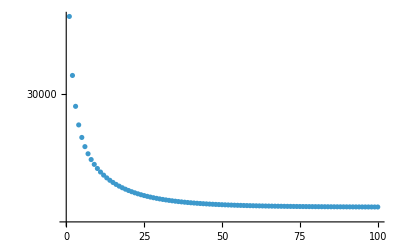

{1.04945}

```mathematica
ListLogPlot[toterr]
{First[toterr]/Last[toterr]}
```

```mathematica
Graphics3D[{Table[{Green,Line[{xyz[[#[[1]]]],xyz[[#[[2]]]]}]&[e]},{e,EdgeList[gr]}],
Table[{Red,Line[{xyz2[[#[[1]]]],xyz2[[#[[2]]]]}]&[e]},{e,EdgeList[gr]}]},SphericalRegion->True,Boxed->False,Background->Black]
```

-Graphics3D-

```mathematica
data=VertexList[gr,(v_/;VertexDegree[gr,v]==3):>(Degree^(-1)ArcCos[align[xyz[[v]]-xyz[[#[[1]]]],xyz[[v]]-xyz[[#[[2]]]]]]&[VertexOutComponent[tg,v,{1}]])];
data2=VertexList[gr,(v_/;VertexDegree[gr,v]==3):>(Degree^(-1)ArcCos[align[xyz2[[v]]-xyz2[[#[[1]]]],xyz2[[v]]-xyz2[[#[[2]]]]]]&[VertexOutComponent[tg,v,{1}]])];
Histogram[{data2,data},ChartLegends->{"min length"+Mean[data2],"original"+Mean[data]}]
```

```mathematica
ListPlot[{Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;getz[v]==z):>palignd[v]],{z,2,VertexEccentricity[tg,1]}],Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;getz[v]==z):>palignd2[v]],{z,2,VertexEccentricity[tg,1]}]},PlotLegends->{"original","min length"}]
```

```mathematica
ListPlot[{Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;branchorder[v]==z):>palignd[v]],{z,1,branchorder[1]-2}],Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;branchorder[v]==z):>palignd2[v]],{z,1,branchorder[1]-2}]},PlotLegends->{"original","min length"}]
```

```mathematica
ListPlot[{Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;getz[v]==z):>Norm[xyz[[v]]-xyz[[getp[v]]]]],{z,2,15}],Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;getz[v]==z):>Norm[xyz2[[v]]-xyz2[[getp[v]]]]],{z,2,15}]
},PlotRange->All,PlotLegends->{"original","min length"}]
```

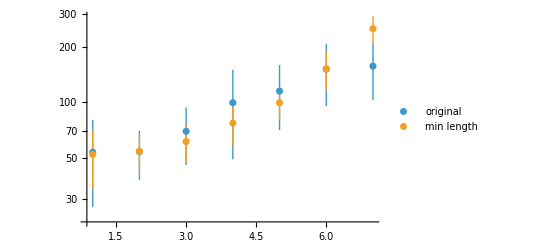

```mathematica
ListLogPlot[{Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;branchorder[v]==z):>4Norm[xyz[[v]]-xyz[[getp[v]]]]],{z,branchorder[1]-1}],Table[{z,Around[Mean[#],StandardDeviation[#]]}&@VertexList[gr,(v_/;branchorder[v]==z):>4Norm[xyz2[[v]]-xyz2[[getp[v]]]]],{z,branchorder[1]-1}]
},PlotRange->All,PlotLegends->{"original","min length"}]
```

```mathematica
xyz2=xyz;
dt=0.2;
tsteps=100;
steinernodes=VertexList[gr,v_/;VertexDegree[gr,v]>1&&Not[v==1]];
toterr=Table[0,{i,tsteps}];
noise=0;
(*k[v_,w_]:=Module[{u=SortBy[{v,w},getz]//First},Log2@Length@VertexOutComponent[tg,u]];*)
k=1;
G=0.1;
Do[
toterr[[i]]=Sum[Norm[xyz2[[e[[1]]]]-xyz2[[e[[2]]]]],{e,EdgeList[gr]}];
Do[
If[VertexDegree[gr,v]==1,
xyz2[[v]]=xyz2[[v]]+dt k(xyz2[[getp[v]]]-xyz2[[v]])+dt G Sum[(xyz2[[w]]-xyz2[[v]])/Norm[xyz2[[w]]-xyz2[[v]]]^3,{w,DeleteCases[ends,v]}],xyz2[[v]]=xyz2[[v]]+dt Sum[k(xyz2[[w]]-xyz2[[v]]),{w,AdjacencyList[gr,v]}]]
,{v,VertexList[gr,Except[1]]}]
,{i,tsteps}];
```

```mathematica
ListPlot[toterr,PlotRange->All]
```

```mathematica
Graphics3D[Table[Line[{xyz2[[v]],xyz2[[getp[v]]]}],{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Boxed->False]
```

```mathematica
Graphics3D[Table[Line[{xyz[[v]],xyz[[getp[v]]]}],{v,VertexList[gr,Except[1]]}],SphericalRegion->True,Boxed->False]
```

## Expansion theory

WolframAlphaQueryResults